# Computational Companion to “Generalized Quasi-Symmetric Nets: A Constructive Approach to the Equimodular Elliptic Type and to Flexible m × n Nets” — Examples Helper

## Tested on: Mathematica 14.0 Written with the assistance of the Claude models Opus 5.5, Fable 5, and Fable 5.1 (Anthropic) All computations were checked by the authors

## Section 1

## Results of Section 1 are used in Examples section

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[sA,sB,sC,sD,bA,bB,bC,bD,α,β,γ,δ,σ,rowS,gL,gLinv,chkR,statusChip,smallChip,colEight,colFour,colTest,eightRef,fourRef,eqName,resultsAll,pairs,kinds,prodId,quotId,prodIdInv,quotIdInv,convProd,convQuot,convQuotInv,posChk,sym,eqRatio1,eqRatio2,sqEq1,sqEq2,eqRow,eqRowS,eqFour,systemLines,bullet,idProd,idQuot,idProdInv,idQuotInv,idConvProd,idConvQuot,idConvQuotInv,posLine,tagOf,braceGrp,condBlock,ratioExpr,pairLbl];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colEight=RGBColor[0.90,0.55,0.05];
colFour=RGBColor[0.80,0.25,0.05];
colTest=RGBColor[0.10,0.35,0.75];
eightRef=Style["the eight equations",Bold,colEight];
fourRef=Style["the four equations",Bold,colFour];
eqName[s_String]:=Style[s,Bold,colFour];
bullet=Style["◼  ",12,colTest];
tagOf[glyph_,col_]:=Style[glyph,14,col];
pairLbl[l_,m_]:=Style[Row[{"pair (",l,", ",m,") :  "}],12,colEight];
braceGrp[items_List,sz_:13,col_:GrayLevel[0]]:=DisplayForm[RowBox[{GridBox[({ToBoxes[Style[#,sz,col]]}&/@items),GridBoxAlignment->{"Columns"->{{Left}}},GridBoxSpacings->{"Rows"->{{1.8}}}],StyleBox["}",FontColor->GrayLevel[0.55],SpanMaxSize->Infinity]}]];
(*The sines of the four numbers at the vertex i are the independent positive symbols sA[i],sB[i],sC[i],sD[i],those of the four barred numbers are bA[i],bB[i],bC[i],bD[i].Every identity below is a rational identity in these symbols,decided by Together;each passage from an equation between squares to the equation between the quantities is decided by Reduce over the positive reals.*)
chkR[a_,b_]:=Module[{d=Together[a-b]},d===0||Simplify[d]===0];
rowS[X_,i_]:=X[[3]][i] X[[4]][i]/(X[[1]][i] X[[2]][i]);
gL[X_,i_]:=X[[1]][i] X[[3]][i]/(X[[2]][i] X[[4]][i]);
gLinv[X_,i_]:=X[[2]][i] X[[4]][i]/(X[[1]][i] X[[3]][i]);
pairs={{2,3},{1,4}};
kinds={{sA,sB,sC,sD},{bA,bB,bC,bD}};
prodId[X_,i_]:=chkR[rowS[X,i] gL[X,i],(X[[3]][i]/X[[2]][i])^2];
quotId[X_,i_]:=chkR[rowS[X,i]/gL[X,i],(X[[4]][i]/X[[1]][i])^2];
prodIdInv[X_,i_]:=chkR[rowS[X,i] gLinv[X,i],(X[[4]][i]/X[[1]][i])^2];
quotIdInv[X_,i_]:=chkR[rowS[X,i]/gLinv[X,i],(X[[3]][i]/X[[2]][i])^2];
convProd[X_,i_]:=chkR[(X[[3]][i]/X[[2]][i]) (X[[4]][i]/X[[1]][i]),rowS[X,i]];
convQuot[X_,i_]:=chkR[(X[[3]][i]/X[[2]][i])/(X[[4]][i]/X[[1]][i]),gL[X,i]];
convQuotInv[X_,i_]:=chkR[(X[[4]][i]/X[[1]][i])/(X[[3]][i]/X[[2]][i]),gLinv[X,i]];
ratioExpr[X_,1,i_]:=X[[3]][i]/X[[2]][i];
ratioExpr[X_,2,i_]:=X[[4]][i]/X[[1]][i];
posChk[lhs_,rhs_]:=Module[{atoms,loc,rules,L,Rr},atoms=Union[Cases[{lhs,rhs},(sA|sB|sC|sD|bA|bB|bC|bD)[_],Infinity]];
loc=Table[Unique["w"],{Length[atoms]}];
rules=Thread[atoms->loc];
L=lhs/. rules;Rr=rhs/. rules;
Reduce[ForAll[Evaluate[loc],Evaluate[And@@(#>0&/@loc)],Evaluate[(L^2==Rr^2)⧦(L==Rr)]]]===True];
(*Display helpers.k=0:the numbers;k=1:the barred numbers.sw=True means the right-hand side has alpha<->beta,gamma<->delta interchanged.*)
sym[0,x_,j_]:=Subscript[x,j];
sym[1,x_,j_]:=OverBar[Subscript[x,j]];
eqRatio1[k_,l_,m_,sw_]:=With[{gl=sym[k,γ,l],bl=sym[k,β,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[Sin[gl]/Sin[bl]==Sin[dm]/Sin[am]],HoldForm[Sin[gl]/Sin[bl]==Sin[gm]/Sin[bm]]]];
eqRatio2[k_,l_,m_,sw_]:=With[{dl=sym[k,δ,l],al=sym[k,α,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[Sin[dl]/Sin[al]==Sin[gm]/Sin[bm]],HoldForm[Sin[dl]/Sin[al]==Sin[dm]/Sin[am]]]];
sqEq1[k_,l_,m_,sw_]:=With[{gl=sym[k,γ,l],bl=sym[k,β,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[(Sin[gl]/Sin[bl])^2==(Sin[dm]/Sin[am])^2],HoldForm[(Sin[gl]/Sin[bl])^2==(Sin[gm]/Sin[bm])^2]]];
sqEq2[k_,l_,m_,sw_]:=With[{dl=sym[k,δ,l],al=sym[k,α,l],gm=sym[k,γ,m],bm=sym[k,β,m],dm=sym[k,δ,m],am=sym[k,α,m]},If[sw,HoldForm[(Sin[dl]/Sin[al])^2==(Sin[gm]/Sin[bm])^2],HoldForm[(Sin[dl]/Sin[al])^2==(Sin[dm]/Sin[am])^2]]];
(*eqRow:the equations of the pairs (1,2),(3,4);eqRowS:those of the pairs (2,3),(4,1);eqFour:equations (a)-(d) with generic indices l,m.*)
eqRow[k_,l_,m_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},HoldForm[Sin[al] Sin[dl]/(Sin[bl] Sin[gl])==Sin[am] Sin[dm]/(Sin[bm] Sin[gm])]];
eqRowS[k_,l_,m_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},HoldForm[Sin[gl] Sin[dl]/(Sin[al] Sin[bl])==Sin[gm] Sin[dm]/(Sin[am] Sin[bm])]];
eqFour[k_,inv_]:=With[{al=sym[k,α,l],bl=sym[k,β,l],gl=sym[k,γ,l],dl=sym[k,δ,l],am=sym[k,α,m],bm=sym[k,β,m],gm=sym[k,γ,m],dm=sym[k,δ,m]},If[inv,HoldForm[Sin[al] Sin[gl]/(Sin[bl] Sin[dl])==Sin[bm] Sin[dm]/(Sin[am] Sin[gm])],HoldForm[Sin[al] Sin[gl]/(Sin[bl] Sin[dl])==Sin[am] Sin[gm]/(Sin[bm] Sin[dm])]]];
idProd[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])] HoldForm[Sin[a] Sin[g]/(Sin[b] Sin[d])]==(Sin[g]/Sin[b])^2]];
idQuot[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])]/HoldForm[Sin[a] Sin[g]/(Sin[b] Sin[d])]==(Sin[d]/Sin[a])^2]];
idProdInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])] HoldForm[Sin[b] Sin[d]/(Sin[a] Sin[g])]==(Sin[d]/Sin[a])^2]];
idQuotInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g] Sin[d]/(Sin[a] Sin[b])]/HoldForm[Sin[b] Sin[d]/(Sin[a] Sin[g])]==(Sin[g]/Sin[b])^2]];
idConvProd[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g]/Sin[b]] HoldForm[Sin[d]/Sin[a]]==Sin[g] Sin[d]/(Sin[a] Sin[b])]];
idConvQuot[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[g]/Sin[b]]/HoldForm[Sin[d]/Sin[a]]==Sin[a] Sin[g]/(Sin[b] Sin[d])]];
idConvQuotInv[k_]:=With[{a=sym[k,α,i],b=sym[k,β,i],g=sym[k,γ,i],d=sym[k,δ,i]},HoldForm[HoldForm[Sin[d]/Sin[a]]/HoldForm[Sin[g]/Sin[b]]==Sin[b] Sin[d]/(Sin[a] Sin[g])]];
posLine[k_,l_,m_,which_,sw_]:=Row[{TraditionalForm[If[which==1,sqEq1[k,l,m,sw],sqEq2[k,l,m,sw]]],"   if and only if   ",TraditionalForm[If[which==1,eqRatio1[k,l,m,sw],eqRatio2[k,l,m,sw]]]}];
systemLines[swU_,swB_]:=Column[{Style[Row[{TraditionalForm[eqRatio1[0,2,3,swU]],",   ",TraditionalForm[eqRatio1[1,2,3,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio2[0,2,3,swU]],",   ",TraditionalForm[eqRatio2[1,2,3,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio1[0,1,4,swU]],",   ",TraditionalForm[eqRatio1[1,1,4,swB]]}],13,colTest],Style[Row[{TraditionalForm[eqRatio2[0,1,4,swU]],",   ",TraditionalForm[eqRatio2[1,1,4,swB]]}],13,colTest],Style[Row[{"together with the equations of the pairs (1, 2) and (3, 4) from ",eightRef," :"}],13,colTest],Style[Row[{TraditionalForm[eqRow[0,1,2]],",   ",TraditionalForm[eqRow[1,1,2]]}],13,colTest],Style[Row[{TraditionalForm[eqRow[0,3,4]],",   ",TraditionalForm[eqRow[1,3,4]]}],13,colTest]},Spacings->0.6];
(*condBlock renders and verifies the reduction for one condition;it returns {ok,column}.Glyphs:filled=identities used in the forward direction,hollow=identities used in the converse direction;circle=direct,triangle=inverted;brown=the numbers,magenta=the barred numbers.For an inverted kind,the left-hand side of the equation from the four equations is direct,so the direct identities are used at the indices 1,2 and the inverted ones at the indices 3,4.*)
condBlock[condName_,eqU_,eqB_,swU_,swB_]:=Module[{tagU=RGBColor[0.55,0.33,0.10],tagB=RGBColor[0.80,0.20,0.50],dot="●",tri="▲",odot="○",otri="△",eqUs=eqName[eqU],eqBs=eqName[eqB],sws={swU,swB},tags,idRows={},idOK={},convRows={},convOK={},posRows,okPos,ok,usedU,usedB},tags={tagU,tagB};
Do[With[{X=kinds[[ik]],kk=ik-1,sw=sws[[ik]],tg=tags[[ik]]},If[!sw,Module[{oP=And@@Table[prodId[X,j],{j,4}],oQ=And@@Table[quotId[X,j],{j,4}],oC=And@@Table[convProd[X,j]&&convQuot[X,j],{j,4}]},AppendTo[idOK,oP&&oQ];AppendTo[convOK,oC];
idRows=Join[idRows,{Style["For  i = 1, 2, 3, 4 :",13],Style[Row[{TraditionalForm[idProd[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oP]}],13],Style[Row[{TraditionalForm[idQuot[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oQ]}],13]}];
convRows=Join[convRows,{Style["For  i = 1, 2, 3, 4 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuot[kk]],"      ",tagOf[odot,tg],"   ",smallChip[oC]}],13]}]],Module[{oP=And@@Table[prodId[X,j],{j,2}],oQ=And@@Table[quotId[X,j],{j,2}],oPi=And@@Table[prodIdInv[X,j],{j,3,4}],oQi=And@@Table[quotIdInv[X,j],{j,3,4}],oC1=And@@Table[convProd[X,j]&&convQuot[X,j],{j,2}],oC2=And@@Table[convProd[X,j]&&convQuotInv[X,j],{j,3,4}]},AppendTo[idOK,oP&&oQ&&oPi&&oQi];
AppendTo[convOK,oC1&&oC2];
idRows=Join[idRows,{Style["For  i = 1, 2 :",13],Style[Row[{TraditionalForm[idProd[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oP]}],13],Style[Row[{TraditionalForm[idQuot[kk]],"      ",tagOf[dot,tg],"   ",smallChip[oQ]}],13],Style["For  i = 3, 4 :",13],Style[Row[{TraditionalForm[idProdInv[kk]],"      ",tagOf[tri,tg],"   ",smallChip[oPi]}],13],Style[Row[{TraditionalForm[idQuotInv[kk]],"      ",tagOf[tri,tg],"   ",smallChip[oQi]}],13]}];
convRows=Join[convRows,{Style["For  i = 1, 2 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuot[kk]],"      ",tagOf[odot,tg],"   ",smallChip[oC1]}],13],Style["For  i = 3, 4 :",13],Style[Row[{TraditionalForm[idConvProd[kk]],",   ",TraditionalForm[idConvQuotInv[kk]],"      ",tagOf[otri,tg],"   ",smallChip[oC2]}],13]}]]]],{ik,2}];
posRows=Flatten[Table[With[{X=kinds[[ik]],sw=sws[[ik]]},Table[{posLine[ik-1,pr[[1]],pr[[2]],wh,sw],posChk[ratioExpr[X,wh,pr[[1]]],ratioExpr[X,If[sw,3-wh,wh],pr[[2]]]]},{pr,pairs},{wh,2}]],{ik,2}],2];
okPos=And@@posRows[[All,2]];
ok=(And@@idOK)&&(And@@convOK)&&okPos;
usedU=If[!swU,Row[{"Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from ",eightRef," by equation ",eqUs," from ",fourRef," for the pairs (2, 3) and (1, 4), and using the identities  ",tagOf[dot,tagU],"  at the four indices, we get"}],Row[{"Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from ",eightRef," by equation ",eqUs," from ",fourRef," for the pairs (2, 3) and (1, 4), and using the identities  ",tagOf[dot,tagU],"  at the indices 1, 2 and the identities  ",tagOf[tri,tagU],"  at the indices 3, 4, we get"}]];
usedB=If[!swB,Row[{"and, in the same way, with equation ",eqBs," from ",fourRef," and the identities  ",tagOf[dot,tagB],"  at the four indices,"}],Row[{"and, in the same way, with equation ",eqBs," from ",fourRef," and the identities  ",tagOf[dot,tagB],"  at the indices 1, 2 and  ",tagOf[tri,tagB],"  at the indices 3, 4,"}]];
{ok,Column[Join[{Style[Row[{"Condition ",condName," uses equations ",eqUs," and ",eqBs," from ",fourRef,"."}],13]},idRows,{Style[usedU,13],braceGrp[{TraditionalForm[sqEq1[0,2,3,swU]],TraditionalForm[sqEq2[0,2,3,swU]],TraditionalForm[sqEq1[0,1,4,swU]],TraditionalForm[sqEq2[0,1,4,swU]]},13],Style[usedB,13],braceGrp[{TraditionalForm[sqEq1[1,2,3,swB]],TraditionalForm[sqEq2[1,2,3,swB]],TraditionalForm[sqEq1[1,1,4,swB]],TraditionalForm[sqEq2[1,1,4,swB]]},13],Style["Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:",13],braceGrp[Table[Row[{posRows[[ir,1]],"   ",smallChip[posRows[[ir,2]]]}],{ir,Length[posRows]}],13],Style["Conversely:",13]},convRows,{Style[Row[{"so the product of the two ratio equations of a pair gives back the equation of that pair from ",eightRef,", and their quotient gives back equation ",eqUs,", respectively ",eqBs,", from ",fourRef,".  The equations of the pairs (1, 2) and (3, 4) from ",eightRef," are not touched."}],13]}],Spacings->0.8]}];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style["For  i = 1, 2, 3, 4 :",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]]," ∈ (0, π),   ",TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]]}],13],Style[Row[{TraditionalForm[HoldForm[OverBar[Subscript[α,i]]==Subscript[σ,i]-Subscript[α,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]==Subscript[σ,i]-Subscript[β,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]==Subscript[σ,i]-Subscript[γ,i]]],",   ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]==Subscript[σ,i]-Subscript[δ,i]]]," ∈ (0, π)"}],13],"",Style["Given equations:",Bold,14],Style[Row[{eightRef," , for the index pairs  (1, 2),  (2, 3),  (3, 4),  (4, 1) :"}],13],Row[{pairLbl[1,2],Style[Row[{TraditionalForm[eqRow[0,1,2]],",   ",TraditionalForm[eqRow[1,1,2]]}],13,colEight]}],Row[{pairLbl[2,3],Style[Row[{TraditionalForm[eqRowS[0,2,3]],",   ",TraditionalForm[eqRowS[1,2,3]]}],13,colEight]}],Row[{pairLbl[3,4],Style[Row[{TraditionalForm[eqRow[0,3,4]],",   ",TraditionalForm[eqRow[1,3,4]]}],13,colEight]}],Row[{pairLbl[4,1],Style[Row[{TraditionalForm[eqRowS[0,4,1]],",   ",TraditionalForm[eqRowS[1,4,1]]}],13,colEight]}],Style[Row[{"and ",fourRef," , for the index pairs  (",TraditionalForm[HoldForm[l]],", ",TraditionalForm[HoldForm[m]],") = (2, 3)  and  (1, 4) :"}],13],Style[Row[{eqName["(a)"],"  ",TraditionalForm[eqFour[0,False]],",     ",eqName["(b)"],"  ",TraditionalForm[eqFour[1,False]]}],13,colFour],Style[Row[{eqName["(c)"],"  ",TraditionalForm[eqFour[0,True]],",     ",eqName["(d)"],"  ",TraditionalForm[eqFour[1,True]]}],13,colFour],Style[Row[{"Condition (i) uses ",eqName["(a)"]," and ",eqName["(b)"],";  condition (ii) uses ",eqName["(c)"]," and ",eqName["(d)"],";  condition (iii) uses ",eqName["(a)"]," and ",eqName["(d)"],";  condition (iv) uses ",eqName["(b)"]," and ",eqName["(c)"],"."}],12,GrayLevel[0.35]],Style[Row[{"For each condition, ",Style["the twelve equations",Bold,colTest]," are ",eightRef," together with, for each of the two index pairs, the two equations from ",fourRef," that the condition uses."}],12,GrayLevel[0.35]],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims  ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style["Claim 1.  For condition (i), the twelve equations are equivalent to the system",Bold,13,colTest]}],systemLines[False,False],"",Row[{bullet,Style["Claim 2.  For condition (ii), the twelve equations are equivalent to the system",Bold,13,colTest]}],systemLines[True,True],Style["for condition (iii), to the system",Bold,13,colTest],systemLines[False,True],Style["and for condition (iv), to the system",Bold,13,colTest],systemLines[True,False],Style[Row[{"that is, to the system of Claim 1 with  ",TraditionalForm[HoldForm[Subscript[α,i]]]," ↔ ",TraditionalForm[HoldForm[Subscript[β,i]]],",  ",TraditionalForm[HoldForm[Subscript[γ,i]]]," ↔ ",TraditionalForm[HoldForm[Subscript[δ,i]]],"  substituted in the right-hand sides, for  i ∈ {3, 4} :  in the first and in the second column of the ratio equations for (ii), in the second column only for (iii), in the first column only for (iv)."}],12,GrayLevel[0.35]]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
resultsAll={};
Module[{col=RGBColor[0.10,0.30,0.70],blk},blk=condBlock["(i)","(a)","(b)",False,False];
AppendTo[resultsAll,blk[[1]]];
Print[Panel[Column[{Row[{Style["Claim 1:  condition (i)",Bold,15,col],Spacer[20],statusChip[blk[[1]]]}],Style["Verification:",Bold,13],blk[[2]],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=RGBColor[0.55,0.25,0.70],blk2,blk3,blk4,ok},blk2=condBlock["(ii)","(c)","(d)",True,True];
blk3=condBlock["(iii)","(a)","(d)",False,True];
blk4=condBlock["(iv)","(b)","(c)",True,False];
ok=blk2[[1]]&&blk3[[1]]&&blk4[[1]];
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Claim 2:  conditions (ii), (iii), (iv)",Bold,15,col],Spacer[20],statusChip[ok]}],Style[Row[{"Equations ",eqName["(c)"]," and ",eqName["(d)"]," from ",fourRef," are equations ",eqName["(a)"]," and ",eqName["(b)"]," with inverted right-hand sides; their left-hand sides, at the indices 1 and 2, are those of ",eqName["(a)"]," and ",eqName["(b)"],"."}],13],Style["Verification for condition (ii):",Bold,13],Row[{blk2[[2]],Spacer[20],statusChip[blk2[[1]]]}],"",Style["Verification for condition (iii):",Bold,13],Row[{blk3[[2]],Spacer[20],statusChip[blk3[[1]]]}],"",Style["Verification for condition (iv):",Bold,13],Row[{blk4[[2]],Spacer[20],statusChip[blk4[[1]]]}],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
For  i = 1, 2, 3, 4 :
α_i, β_i, γ_i, δ_i ∈ (0, π),   σ_i==1/2 (α_i+β_i+γ_i+δ_i)
OverBar[α_i]==σ_i-α_i,   OverBar[β_i]==σ_i-β_i,   OverBar[γ_i]==σ_i-γ_i,   OverBar[δ_i]==σ_i-δ_i ∈ (0, π)

Given equations:
the eight equations , for the index pairs  (1, 2),  (2, 3),  (3, 4),  (4, 1) :
pair (1, 2) :  (sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
pair (2, 3) :  (sin(γ_2) sin(δ_2))/(sin(α_2) sin(β_2))==(sin(γ_3) sin(δ_3))/(sin(α_3) sin(β_3)),   (sin(OverBar[γ_2]) sin(OverBar[δ_2]))/(sin(OverBar[α_2]) sin(OverBar[β_2]))==(sin(OverBar[γ_3]) sin(OverBar[δ_3]))/(sin(OverBar[α_3]) sin(OverBar[β_3]))
pair (3, 4) :  (sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
pair (4, 1) :  (sin(γ_4) sin(δ_4))/(sin(α_4) sin(β_4))==(sin(γ_1) sin(δ_1))/(sin(α_1) sin(β_1)),   (sin(OverBar[γ_4]) sin(OverBar[δ_4]))/(sin(OverBar[α_4]) sin(OverBar[β_4]))==(sin(OverBar[γ_1]) sin(OverBar[δ_1]))/(sin(OverBar[α_1]) sin(OverBar[β_1]))
and the four equations , for the index pairs  (l, m) = (2, 3)  and  (1, 4) :
(a)  (sin(α_l) sin(γ_l))/(sin(β_l) sin(δ_l))==(sin(α_m) sin(γ_m))/(sin(β_m) sin(δ_m)),     (b)  (sin(OverBar[α_l]) sin(OverBar[γ_l]))/(sin(OverBar[β_l]) sin(OverBar[δ_l]))==(sin(OverBar[α_m]) sin(OverBar[γ_m]))/(sin(OverBar[β_m]) sin(OverBar[δ_m]))
(c)  (sin(α_l) sin(γ_l))/(sin(β_l) sin(δ_l))==(sin(β_m) sin(δ_m))/(sin(α_m) sin(γ_m)),     (d)  (sin(OverBar[α_l]) sin(OverBar[γ_l]))/(sin(OverBar[β_l]) sin(OverBar[δ_l]))==(sin(OverBar[β_m]) sin(OverBar[δ_m]))/(sin(OverBar[α_m]) sin(OverBar[γ_m]))
Condition (i) uses (a) and (b);  condition (ii) uses (c) and (d);  condition (iii) uses (a) and (d);  condition (iv) uses (b) and (c).
For each condition, the twelve equations are the eight equations together with, for each of the two index pairs, the two equations from the four equations that the condition uses.
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ :
◼  Claim 1.  For condition (i), the twelve equations are equivalent to the system
(sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
(sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))

◼  Claim 2.  For condition (ii), the twelve equations are equivalent to the system
(sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
(sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
for condition (iii), to the system
(sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
(sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
and for condition (iv), to the system
(sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3)),   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))
(sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3)),   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))
(sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4)),   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))
(sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4)),   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))
together with the equations of the pairs (1, 2) and (3, 4) from the eight equations :
(sin(α_1) sin(δ_1))/(sin(β_1) sin(γ_1))==(sin(α_2) sin(δ_2))/(sin(β_2) sin(γ_2)),   (sin(OverBar[α_1]) sin(OverBar[δ_1]))/(sin(OverBar[β_1]) sin(OverBar[γ_1]))==(sin(OverBar[α_2]) sin(OverBar[δ_2]))/(sin(OverBar[β_2]) sin(OverBar[γ_2]))
(sin(α_3) sin(δ_3))/(sin(β_3) sin(γ_3))==(sin(α_4) sin(δ_4))/(sin(β_4) sin(γ_4)),   (sin(OverBar[α_3]) sin(OverBar[δ_3]))/(sin(OverBar[β_3]) sin(OverBar[γ_3]))==(sin(OverBar[α_4]) sin(OverBar[δ_4]))/(sin(OverBar[β_4]) sin(OverBar[γ_4]))
that is, to the system of Claim 1 with  α_i ↔ β_i,  γ_i ↔ δ_i  substituted in the right-hand sides, for  i ∈ {3, 4} :  in the first and in the second column of the ratio equations for (ii), in the second column only for (iii), in the first column only for (iv).

Claim 1:  condition (i)Verified
Verification:
Condition (i) uses equations (a) and (b) from the four equations.
For  i = 1, 2, 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (a) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the four indices, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2}
and, in the same way, with equation (b) from the four equations and the identities  ●  at the four indices,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑}
Conversely:
For  i = 1, 2, 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (a), respectively (b), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.
Together, these give Claim 1.

Claim 2:  conditions (ii), (iii), (iv)Verified
Equations (c) and (d) from the four equations are equations (a) and (b) with inverted right-hand sides; their left-hand sides, at the indices 1 and 2, are those of (a) and (b).
Verification for condition (ii):
Condition (ii) uses equations (c) and (d) from the four equations.
For  i = 1, 2 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))==((sin(δ_i))/(sin(α_i)))^2      ▲   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i)))==((sin(γ_i))/(sin(β_i)))^2      ▲   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ▲   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i])))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ▲   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (c) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the indices 1, 2 and the identities  ▲  at the indices 3, 4, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2}
and, in the same way, with equation (d) from the four equations and the identities  ●  at the indices 1, 2 and  ▲  at the indices 3, 4,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑}
Conversely:
For  i = 1, 2 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(δ_i))/(sin(α_i)))/((sin(γ_i))/(sin(β_i)))==(sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))      △   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))/((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))==(sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))      △   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (c), respectively (d), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified

Verification for condition (iii):
Condition (iii) uses equations (a) and (d) from the four equations.
For  i = 1, 2, 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ▲   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i])))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ▲   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (a) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the four indices, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2}
and, in the same way, with equation (d) from the four equations and the identities  ●  at the indices 1, 2 and  ▲  at the indices 3, 4,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑}
Conversely:
For  i = 1, 2, 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 1, 2 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
For  i = 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))/((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))==(sin(OverBar[β_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))      △   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (a), respectively (d), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified

Verification for condition (iv):
Condition (iv) uses equations (b) and (c) from the four equations.
For  i = 1, 2 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))==((sin(γ_i))/(sin(β_i)))^2      ●   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i)))==((sin(δ_i))/(sin(α_i)))^2      ●   ☑
For  i = 3, 4 :
(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)) (sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))==((sin(δ_i))/(sin(α_i)))^2      ▲   ☑
((sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)))/((sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i)))==((sin(γ_i))/(sin(β_i)))^2      ▲   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])) (sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))==((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))^2      ●   ☑
((sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])))/((sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i])))==((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))^2      ●   ☑
Multiplying and dividing the equations of the pairs (2, 3) and (4, 1) from the eight equations by equation (b) from the four equations for the pairs (2, 3) and (1, 4), and using the identities  ●  at the indices 1, 2 and the identities  ▲  at the indices 3, 4, we get
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2}
and, in the same way, with equation (c) from the four equations and the identities  ●  at the four indices,
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2}
Since all sines are positive, it follows that each equation between squares is equivalent to the equation between the quantities themselves:
((sin(γ_2))/(sin(β_2)))^2==((sin(δ_3))/(sin(α_3)))^2   if and only if   (sin(γ_2))/(sin(β_2))==(sin(δ_3))/(sin(α_3))   ☑
((sin(δ_2))/(sin(α_2)))^2==((sin(γ_3))/(sin(β_3)))^2   if and only if   (sin(δ_2))/(sin(α_2))==(sin(γ_3))/(sin(β_3))   ☑
((sin(γ_1))/(sin(β_1)))^2==((sin(δ_4))/(sin(α_4)))^2   if and only if   (sin(γ_1))/(sin(β_1))==(sin(δ_4))/(sin(α_4))   ☑
((sin(δ_1))/(sin(α_1)))^2==((sin(γ_4))/(sin(β_4)))^2   if and only if   (sin(δ_1))/(sin(α_1))==(sin(γ_4))/(sin(β_4))   ☑
((sin(OverBar[γ_2]))/(sin(OverBar[β_2])))^2==((sin(OverBar[γ_3]))/(sin(OverBar[β_3])))^2   if and only if   (sin(OverBar[γ_2]))/(sin(OverBar[β_2]))==(sin(OverBar[γ_3]))/(sin(OverBar[β_3]))   ☑
((sin(OverBar[δ_2]))/(sin(OverBar[α_2])))^2==((sin(OverBar[δ_3]))/(sin(OverBar[α_3])))^2   if and only if   (sin(OverBar[δ_2]))/(sin(OverBar[α_2]))==(sin(OverBar[δ_3]))/(sin(OverBar[α_3]))   ☑
((sin(OverBar[γ_1]))/(sin(OverBar[β_1])))^2==((sin(OverBar[γ_4]))/(sin(OverBar[β_4])))^2   if and only if   (sin(OverBar[γ_1]))/(sin(OverBar[β_1]))==(sin(OverBar[γ_4]))/(sin(OverBar[β_4]))   ☑
((sin(OverBar[δ_1]))/(sin(OverBar[α_1])))^2==((sin(OverBar[δ_4]))/(sin(OverBar[α_4])))^2   if and only if   (sin(OverBar[δ_1]))/(sin(OverBar[α_1]))==(sin(OverBar[δ_4]))/(sin(OverBar[α_4]))   ☑}
Conversely:
For  i = 1, 2 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(γ_i))/(sin(β_i)))/((sin(δ_i))/(sin(α_i)))==(sin(α_i) sin(γ_i))/(sin(β_i) sin(δ_i))      ○   ☑
For  i = 3, 4 :
(sin(γ_i))/(sin(β_i)) (sin(δ_i))/(sin(α_i))==(sin(γ_i) sin(δ_i))/(sin(α_i) sin(β_i)),   ((sin(δ_i))/(sin(α_i)))/((sin(γ_i))/(sin(β_i)))==(sin(β_i) sin(δ_i))/(sin(α_i) sin(γ_i))      △   ☑
For  i = 1, 2, 3, 4 :
(sin(OverBar[γ_i]))/(sin(OverBar[β_i])) (sin(OverBar[δ_i]))/(sin(OverBar[α_i]))==(sin(OverBar[γ_i]) sin(OverBar[δ_i]))/(sin(OverBar[α_i]) sin(OverBar[β_i])),   ((sin(OverBar[γ_i]))/(sin(OverBar[β_i])))/((sin(OverBar[δ_i]))/(sin(OverBar[α_i])))==(sin(OverBar[α_i]) sin(OverBar[γ_i]))/(sin(OverBar[β_i]) sin(OverBar[δ_i]))      ○   ☑
so the product of the two ratio equations of a pair gives back the equation of that pair from the eight equations, and their quotient gives back equation (b), respectively (c), from the four equations.  The equations of the pairs (1, 2) and (3, 4) from the eight equations are not touched.Verified
Together, these give Claim 2.

ALL CLAIMS VERIFIED

## Section 2

## Results of Section 2 are used in the proof of Lemma 16 & in the proof of Proposition 4

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,σ,X,sigOf,barsOf,statusChip,smallChip,colTest,bullet,cases,caseCol,vertsOf,unk,relsOf,relDisp,ratZeroQ,zeroListQ,sgnCombos,combOf,congrQ,complQ,aOf,bOf,cOf,dOf,MOf,rOf,sOf,fOf,resultsAll,barSym,barTargets,barTargetDisp,quadDisp,solveCase,n1Disp,pmDisp,reorder,halfSumDisp,minusDisp];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colTest=RGBColor[0.10,0.35,0.75];
bullet=Style["◼  ",12,colTest];
(*The numbers at the vertex 1 are the independent symbols alpha,beta,gamma,delta;the numbers at the vertices 2,3,4 are the unique solution of the relations of each case,found by Solve.Every check below is a linear or a trigonometric identity in alpha,beta,gamma,delta;a trigonometric identity is decided on the numerator of the difference of its two sides,by TrigReduce or TrigExpand followed by Simplify.*)
X={α,β,γ,δ};
sigOf[{a_,b_,c_,d_}]:=(a+b+c+d)/2;
barsOf[Y_List]:=sigOf[Y]-Y;
ratZeroQ[expr_]:=Module[{n=Numerator[Together[expr]]},Simplify[TrigReduce[n]]===0||Simplify[TrigExpand[n]]===0];
zeroListQ[lst_List]:=And@@(Simplify[#]===0&/@lst);
sgnCombos=Tuples[{1,-1},3];
combOf[Y_List,s_List]:=Y[[1]]+s[[1]] Y[[2]]+s[[2]] Y[[3]]+s[[3]] Y[[4]];
congrQ[Yv_List,Y1_List]:=And@@Table[Or@@Flatten[Table[IntegerQ[Simplify[(combOf[Yv,s]-e combOf[Y1,sp])/(2 π)]],{sp,sgnCombos},{e,{1,-1}}]],{s,sgnCombos}];
complQ[Yv_List,ref_List]:=And@@(MemberQ[Join[ref,π-ref],Simplify[#]]&/@Yv);
aOf[Y_List]:=Sin[Y[[1]]]/Sin[barsOf[Y][[1]]];
bOf[Y_List]:=Sin[Y[[2]]]/Sin[barsOf[Y][[2]]];
cOf[Y_List]:=Sin[Y[[3]]]/Sin[barsOf[Y][[3]]];
dOf[Y_List]:=Sin[Y[[4]]]/Sin[barsOf[Y][[4]]];
MOf[Y_List]:=aOf[Y] bOf[Y] cOf[Y] dOf[Y];
rOf[Y_List]:=aOf[Y] dOf[Y];
sOf[Y_List]:=cOf[Y] dOf[Y];
fOf[Y_List]:=aOf[Y] cOf[Y];
cases={"(a)","(b)","(c)","(d)"};
caseCol["(a)"]=RGBColor[0.55,0.33,0.10];
caseCol["(b)"]=RGBColor[0.00,0.45,0.25];
caseCol["(c)"]=RGBColor[0.10,0.45,0.65];
caseCol["(d)"]=RGBColor[0.55,0.15,0.25];
unk={{a2,b2,g2,d2},{a3,b3,g3,d3},{a4,b4,g4,d4}};
relsOf["(a)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[3]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[4]]),b[[1]]-b[[3]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[4]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(b)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[4]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[3]]),d[[1]]-g[[4]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[3]])}];
relsOf["(c)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[3]]),b[[1]]-b[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[3]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(d)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[4]]),d[[1]]-g[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[4]])}];
solveCase[c_]:=Module[{sol=Solve[Thread[relsOf[c][Prepend[unk,X]]==0],Flatten[unk]]},If[Length[sol]==1,Prepend[unk/. sol[[1]],X],Missing[]]];
Do[vertsOf[c]=solveCase[c],{c,cases}];
relDisp["(a)"]={HoldForm[Subscript[α,1]==Subscript[α,3]==π-Subscript[α,2]==π-Subscript[α,4]],HoldForm[Subscript[β,1]==Subscript[β,3]==π-Subscript[β,2]==π-Subscript[β,4]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(b)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,4]==π-Subscript[γ,2]==π-Subscript[δ,3]],HoldForm[Subscript[δ,1]==Subscript[γ,4]==π-Subscript[δ,2]==π-Subscript[γ,3]]};
relDisp["(c)"]={HoldForm[Subscript[α,1]==Subscript[α,4]==π-Subscript[α,2]==π-Subscript[α,3]],HoldForm[Subscript[β,1]==Subscript[β,4]==π-Subscript[β,2]==π-Subscript[β,3]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(d)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,3]==π-Subscript[γ,2]==π-Subscript[δ,4]],HoldForm[Subscript[δ,1]==Subscript[γ,3]==π-Subscript[δ,2]==π-Subscript[γ,4]]};
(*Display helpers.*)
quadDisp[k_]:=HoldForm[{Subscript[α,k],Subscript[β,k],Subscript[γ,k],Subscript[δ,k]}];
(*A combination  x1+-x2+-x3+-x4  of the given symbols,displayed without nested parentheses.*)
pmDisp[syms_List]:=Row[Riffle[TraditionalForm[HoldForm[#]]&/@syms," ± "]];
n1Disp[k_]:=Row[{pmDisp[{Subscript[α,k],Subscript[β,k],Subscript[γ,k],Subscript[δ,k]}]," ≠ 0  (mod 2π)  for all choices of the signs ±"}];
barSym=OverBar[Subscript[#,1]]&/@{α,β,γ,δ};
(*The two orders of four numbers under which the flat angles of two neighbouring blocks at a common vertex coincide.*)
reorder["reverse"][Y_List]:=Y[[{4,3,2,1}]];
reorder["pairs"][Y_List]:=Y[[{2,1,4,3}]];
(*The half sum of the numbers syms,and sigma_1 minus each of them,displayed explicitly.*)
halfSumDisp[syms_List]:=Row[{"(",Row[Riffle[TraditionalForm/@syms," + "]],")/2  =  ",TraditionalForm[HoldForm[Subscript[σ,1]]]}];
minusDisp[syms_List,bsyms_List]:=Row[{"(",Row[Riffle[Row[{TraditionalForm[HoldForm[Subscript[σ,1]]]," − ",TraditionalForm[#]}]&/@syms,", "]],")  =  (",Row[Riffle[TraditionalForm/@bsyms,", "]],")"}];
barTargets["(a)"][B_]:={π-B,B,π-B};
barTargets["(b)"][B_]:={π-B,π-B[[{2,1,4,3}]],B[[{2,1,4,3}]]};
barTargets["(c)"][B_]:={π-B,{B[[2]],B[[1]],π-B[[4]],π-B[[3]]},{π-B[[2]],π-B[[1]],B[[4]],B[[3]]}};
barTargets["(d)"][B_]:={π-B,{B[[1]],B[[2]],π-B[[3]],π-B[[4]]},{π-B[[1]],π-B[[2]],B[[3]],B[[4]]}};
barTargetDisp[c_,k_]:=TraditionalForm[HoldForm[{OverBar[Subscript[α,k]],OverBar[Subscript[β,k]],OverBar[Subscript[γ,k]],OverBar[Subscript[δ,k]]}]==barTargets[c][barSym][[k-1]]];
resultsAll={};
(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{TraditionalForm[quadDisp[1]]," = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π)"}],13],Style[n1Disp[1],13],Style[Row[{TraditionalForm[HoldForm[Subscript[σ,1]==(α+β+γ+δ)/2]]}],13],Style[Row[{TraditionalForm[HoldForm[OverBar[Subscript[α,1]]==Subscript[σ,1]-α]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[β,1]]==Subscript[σ,1]-β]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,1]]==Subscript[σ,1]-γ]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,1]]==Subscript[σ,1]-δ]]," ∈ (0, π)"}],13],"",Style["Definitions, for  i = 1, 2, 3, 4 :",Bold,14],Style[Row[{TraditionalForm[HoldForm[Subscript[σ,i]==(Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i])/2]],",   ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]]]}],13],Style[Row[{TraditionalForm[HoldForm[OverBar[Subscript[α,i]]==Subscript[σ,i]-Subscript[α,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]==Subscript[σ,i]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]==Subscript[σ,i]-Subscript[γ,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]==Subscript[σ,i]-Subscript[δ,i]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[a,i]==Sin[Subscript[α,i]]/Sin[OverBar[Subscript[α,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[b,i]==Sin[Subscript[β,i]]/Sin[OverBar[Subscript[β,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[c,i]==Sin[Subscript[γ,i]]/Sin[OverBar[Subscript[γ,i]]]]],",  ",TraditionalForm[HoldForm[Subscript[d,i]==Sin[Subscript[δ,i]]/Sin[OverBar[Subscript[δ,i]]]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[M,i]==Subscript[a,i] Subscript[b,i] Subscript[c,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[r,i]==Subscript[a,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[s,i]==Subscript[c,i] Subscript[d,i]]],",  ",TraditionalForm[HoldForm[Subscript[f,i]==Subscript[a,i] Subscript[c,i]]]}],13],Style[TraditionalForm[HoldForm[Subscript[z,i]==1/(Subscript[f,i]-1)]],13],Style[TraditionalForm[HoldForm[χ==Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4] Sign[Subscript[z,1] Subscript[z,3]]]],13],"",Style["Given cases:",Bold,14],Sequence@@Table[Style[Row[{Style["Case "<>c<>"   ",Bold,13],Row[Riffle[TraditionalForm/@relDisp[c],",    "]]}],13,caseCol[c]],{c,cases}],Style[Row[{"Each  ",smallChip[True],"  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ",smallChip[False],"  would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims  ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style[Row[{"Claim 1.  In each case, the relations determine  ",TraditionalForm[quadDisp[2]],", ",TraditionalForm[quadDisp[3]],", ",TraditionalForm[quadDisp[4]],"  uniquely,   ",TraditionalForm[HoldForm[Subscript[δ,1]+Subscript[δ,2]+Subscript[δ,3]+Subscript[δ,4]==2 π]],",   and  ",n1Disp[i],"  for  i = 2, 3, 4."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 2.  In each case,  ",TraditionalForm[HoldForm[Subscript[α,i]]],", ",TraditionalForm[HoldForm[Subscript[β,i]]],", ",TraditionalForm[HoldForm[Subscript[γ,i]]],", ",TraditionalForm[HoldForm[Subscript[δ,i]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[α,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[β,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]]]," ∈ (0, π)  and  ",TraditionalForm[HoldForm[Subscript[M,i]>0]],"  for each  i = 1, 2, 3, 4."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 3.  In each case, for each  i = 1, 2, 3, 4 :  ",TraditionalForm[HoldForm[Subscript[σ,i]∉π ℤ]],",  ",TraditionalForm[HoldForm[Subscript[f,i]!=1]],",  ",TraditionalForm[HoldForm[Subscript[M,i]!=1]],";  hence  ",TraditionalForm[HoldForm[Subscript[ε,i]∈{±1}]],",  ",TraditionalForm[HoldForm[Subscript[z,i]]],"  is well defined, and  ",TraditionalForm[HoldForm[χ∈{±1}]],"."}],Bold,13,colTest]}],"",Row[{bullet,Style[Row[{"Claim 4.  In each case,  ",TraditionalForm[HoldForm[Subscript[M,1]==Subscript[M,2]==Subscript[M,3]==Subscript[M,4]]]," =: M   and   ",TraditionalForm[HoldForm[Subscript[r,1]==Subscript[r,2]]],",  ",TraditionalForm[HoldForm[Subscript[s,1]==Subscript[s,4]]],",  ",TraditionalForm[HoldForm[Subscript[r,3]==Subscript[r,4]]],",  ",TraditionalForm[HoldForm[Subscript[s,2]==Subscript[s,3]]],"."}],Bold,13,colTest]}],"",Row[{bullet,Style["Claim 5.  With  M  as in Claim 4:",Bold,13,colTest]}],Style[Row[{"        in case (a),   ",TraditionalForm[HoldForm[Subscript[f,2]==Subscript[f,3]]],",  ",TraditionalForm[HoldForm[Subscript[f,1]==Subscript[f,4]]],",  ",TraditionalForm[HoldForm[χ (Subscript[f,2]-1) (Subscript[f,1]-1)>0]],";"}],Bold,13,colTest],Style[Row[{"        in case (b),   ",TraditionalForm[HoldForm[Subscript[f,2] Subscript[f,3]==Subscript[f,1] Subscript[f,4]==M]],";"}],Bold,13,colTest],Style[Row[{"        in case (c),   ",TraditionalForm[HoldForm[Subscript[f,2]+Subscript[f,3]-Subscript[f,2] Subscript[f,3]==Subscript[f,1]+Subscript[f,4]-Subscript[f,1] Subscript[f,4]==M]],",  ",TraditionalForm[HoldForm[χ (1-M)>0]],";"}],Bold,13,colTest],Style[Row[{"        in case (d),   ",TraditionalForm[HoldForm[(Subscript[f,2]+Subscript[f,3]-1)/(Subscript[f,2] Subscript[f,3])==(Subscript[f,1]+Subscript[f,4]-1)/(Subscript[f,1] Subscript[f,4])==1/M]],"."}],Bold,13,colTest],"",Row[{bullet,Style[Row[{"Claim 6.  The numbers  α, β, γ, δ  in the orders  ",TraditionalForm[HoldForm[{δ,γ,β,α}]],"  and  ",TraditionalForm[HoldForm[{β,α,δ,γ}]],"  satisfy:"}],Bold,13,colTest]}],Style[Row[{"        ",pmDisp[reorder["reverse"][X]]," ≠ 0  and  ",pmDisp[reorder["pairs"][X]]," ≠ 0  (mod 2π)  for all choices of the signs ±;"}],Bold,13,colTest],Style[Row[{"        ",halfSumDisp[reorder["reverse"][X]],"  and  ",halfSumDisp[reorder["pairs"][X]],";"}],Bold,13,colTest],Style[Row[{"        ",minusDisp[reorder["reverse"][X],reorder["reverse"][barSym]],"  and  ",minusDisp[reorder["pairs"][X],reorder["pairs"][barSym]],"."}],Bold,13,colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];
(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
ClearAll[congrOneQ,comboDisp,sgnStr];
(*congrOneQ:the number differs from plus or minus one of alpha+-beta+-gamma+-delta by an integer multiple of 2 pi.*)
congrOneQ[expr_,Y1_List]:=Or@@Flatten[Table[IntegerQ[Simplify[(expr-e combOf[Y1,sp])/(2 π)]],{sp,sgnCombos},{e,{1,-1}}]];
sgnStr[1]=" + ";sgnStr[-1]=" − ";
comboDisp[k_,s_List]:=Row[{TraditionalForm[HoldForm[Subscript[α,k]]],sgnStr[s[[1]]],TraditionalForm[HoldForm[Subscript[β,k]]],sgnStr[s[[2]]],TraditionalForm[HoldForm[Subscript[γ,k]]],sgnStr[s[[3]]],TraditionalForm[HoldForm[Subscript[δ,k]]]}];
Module[{col=RGBColor[0.10,0.30,0.70],rows={},ok=True},Do[Module[{V=vertsOf[c],okUnique,rsym,rsol,okV,okSum,okN1,signRows},okUnique=!MissingQ[V];
If[okUnique,rsym=relsOf[c][Prepend[unk,X]];
rsol=relsOf[c][V];
okV=Table[zeroListQ[rsol[[Flatten[Position[rsym,_?(!FreeQ[#,Alternatives@@unk[[k-1]]]&),{1},Heads->False]]]]],{k,2,4}];
okSum=Simplify[Total[V[[All,4]]]-2 π]===0;
okN1=Table[congrOneQ[combOf[V[[k]],s],V[[1]]],{k,2,4},{s,sgnCombos}],okV={False,False,False};okSum=False;
okN1=Table[False,{3},{8}]];
ok=ok&&okUnique&&(And@@okV)&&okSum&&(And@@Flatten[okN1]);
signRows=If[okUnique,Table[Column[Prepend[Table[Row[{comboDisp[k,s]," = ",TraditionalForm[Simplify[combOf[V[[k]],s]]],"   ",smallChip[okN1[[k-1,is]]]}],{is,8},{s,{sgnCombos[[is]]}}][[All,1]],Style[Row[{"i = ",k," :"}],13]],Spacings->0.4],{k,2,4}],{}];
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :   ",Bold,13,caseCol[c]],"the relations   ",Row[Riffle[TraditionalForm/@relDisp[c],",   "]],"   have the unique solution"}],13],If[okUnique,Column[{Style[Row[{TraditionalForm[quadDisp[2]==V[[2]]],"   ",smallChip[okV[[1]]]}],13],Style[Row[{TraditionalForm[quadDisp[3]==V[[3]]],"   ",smallChip[okV[[2]]]}],13],Style[Row[{TraditionalForm[quadDisp[4]==V[[4]]],"   ",smallChip[okV[[3]]]}],13],Style[Row[{TraditionalForm[HoldForm[Subscript[δ,1]+Subscript[δ,2]+Subscript[δ,3]+Subscript[δ,4]==2 π]],"   ",smallChip[okSum]}],13]},Spacings->0.4],Style[Row[{"(no unique solution)   ",smallChip[False]}],13]],Style["for  i = 2, 3, 4  and all choices of the signs:",13],Sequence@@(Style[#,13]&/@signRows),Style[Row[{"each value differs from  ",Row[{"±(",pmDisp[X],")"}],"  by an integer multiple of 2π, and  ",n1Disp[1],"  by the hypothesis;  hence  ",n1Disp[i],"  for  i = 2, 3, 4."}],13],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 1:  the four cases",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:",Bold,13]},Most[rows],{Style["Together, these give Claim 1.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=RGBColor[0.55,0.25,0.70],B=barsOf[X],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],okCompl,oks},okCompl=Table[complQ[V[[k]],X],{k,2,4}];
oks=Table[zeroListQ[barsOf[V[[k]]]-barTargets[c][B][[k-1]]],{k,2,4}];
ok=ok&&(And@@okCompl)&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Join[Table[Style[Row[{ind,TraditionalForm[quadDisp[k]==V[[k]]]," ,  each entry is one of  α, β, γ, δ  or its complement to π   ",smallChip[okCompl[[k-1]]]}],13],{k,2,4}],Table[Style[Row[{ind,barTargetDisp[c,k],"   ",smallChip[oks[[k-1]]]}],13],{k,2,4}]],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 2:  the numbers and the barred numbers at the vertices 2, 3, 4",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  substituting the quadruples of Claim 1 into the definitions of the half sums and of the barred numbers, we get",Bold,13]},Most[rows],{Style[Row[{"Since  α, β, γ, δ  and  ",TraditionalForm[HoldForm[OverBar[Subscript[α,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[β,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[γ,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[δ,1]]]],"  lie in  (0, π)  by the hypotheses, it follows that their complements to π lie in  (0, π)  as well;  hence all numbers and barred numbers at the vertices 2, 3, 4 lie in  (0, π),  all sines in the definitions of  ",TraditionalForm[HoldForm[Subscript[a,i]]],", ",TraditionalForm[HoldForm[Subscript[b,i]]],", ",TraditionalForm[HoldForm[Subscript[c,i]]],", ",TraditionalForm[HoldForm[Subscript[d,i]]],"  are positive, and  ",TraditionalForm[HoldForm[Subscript[M,i]>0]],"  for each  i = 1, 2, 3, 4.  Together, these give Claim 2."}],13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=RGBColor[0.00,0.50,0.50],B=barsOf[X],sg=sigOf[X],okS,okA,okG,okD,okF,okM,ok,ind="        "},okS=Simplify[2 sg-(α+β+γ+δ)]===0;
okA=Simplify[2 (B[[1]]-β)-(-α-β+γ+δ)]===0;
okG=Simplify[2 (B[[3]]-β)-(α-β-γ+δ)]===0;
okD=Simplify[2 (B[[4]]-β)-(α-β+γ-δ)]===0;
okF=ratZeroQ[fOf[X]-1-Sin[sg] Sin[B[[4]]-β]/(Sin[B[[1]]] Sin[B[[3]]])];
okM=ratZeroQ[1-MOf[X]-Sin[sg] Sin[B[[1]]-β] Sin[B[[3]]-β] Sin[B[[4]]-β]/(Sin[B[[1]]] Sin[B[[2]]] Sin[B[[3]]] Sin[B[[4]]])];
ok=okS&&okA&&okG&&okD&&okF&&okM;
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Claim 3:  the half sums, the quantities  \!\(\*SubscriptBox[\(f\), \(i\)]\)  and  \!\(\*SubscriptBox[\(M\), \(i\)]\)",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  the following identities hold for an arbitrary quadruple, hence at each vertex  i = 1, 2, 3, 4 :",Bold,13],Column[{Style[Row[{ind,TraditionalForm[HoldForm[2 Subscript[σ,i]==Subscript[α,i]+Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okS]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[α,i]]-Subscript[β,i])==-Subscript[α,i]-Subscript[β,i]+Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okA]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[γ,i]]-Subscript[β,i])==Subscript[α,i]-Subscript[β,i]-Subscript[γ,i]+Subscript[δ,i]]],"   ",smallChip[okG]}],13],Style[Row[{ind,TraditionalForm[HoldForm[2 (OverBar[Subscript[δ,i]]-Subscript[β,i])==Subscript[α,i]-Subscript[β,i]+Subscript[γ,i]-Subscript[δ,i]]],"   ",smallChip[okD]}],13],Style[Row[{ind,TraditionalForm[HoldForm[Subscript[f,i]-1==Sin[Subscript[σ,i]] Sin[OverBar[Subscript[δ,i]]-Subscript[β,i]]/(Sin[OverBar[Subscript[α,i]]] Sin[OverBar[Subscript[γ,i]]])]],"   ",smallChip[okF]}],13],Style[Row[{ind,TraditionalForm[HoldForm[1-Subscript[M,i]==Sin[Subscript[σ,i]] Sin[OverBar[Subscript[α,i]]-Subscript[β,i]] Sin[OverBar[Subscript[γ,i]]-Subscript[β,i]] Sin[OverBar[Subscript[δ,i]]-Subscript[β,i]]/(Sin[OverBar[Subscript[α,i]]] Sin[OverBar[Subscript[β,i]]] Sin[OverBar[Subscript[γ,i]]] Sin[OverBar[Subscript[δ,i]]])]],"   ",smallChip[okM]}],13]},Spacings->0.4],Style[Row[{"The right-hand sides of the first four identities are, up to sign, numbers  ",pmDisp[{Subscript[α,i],Subscript[β,i],Subscript[γ,i],Subscript[δ,i]}]," ,  which are  ≠ 0  (mod 2π)  by the hypothesis and Claim 1;  hence  ",TraditionalForm[HoldForm[Subscript[σ,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[α,i]]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[γ,i]]-Subscript[β,i]]],",  ",TraditionalForm[HoldForm[OverBar[Subscript[δ,i]]-Subscript[β,i]]],"  are not in  πℤ,  and their sines are nonzero.  Since the sines of the barred numbers are nonzero by Claim 2, it follows from the last two identities that  ",TraditionalForm[HoldForm[Subscript[f,i]!=1]],"  and  ",TraditionalForm[HoldForm[Subscript[M,i]!=1]]," .  Hence  ",TraditionalForm[HoldForm[Subscript[ε,i]==Sign[Sin[Subscript[σ,i]]]∈{±1}]],",  ",TraditionalForm[HoldForm[Subscript[z,i]==1/(Subscript[f,i]-1)]],"  is well defined and nonzero, and  ",TraditionalForm[HoldForm[χ∈{±1}]]," .  Together, these give Claim 3."}],13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 6:CLAIM 4*)
(* ============================================================*)
Module[{col=RGBColor[0.75,0.35,0.05],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],oks,disps},oks={ratZeroQ[MOf[V[[1]]]-MOf[V[[2]]]],ratZeroQ[MOf[V[[2]]]-MOf[V[[3]]]],ratZeroQ[MOf[V[[3]]]-MOf[V[[4]]]],ratZeroQ[rOf[V[[1]]]-rOf[V[[2]]]],ratZeroQ[sOf[V[[1]]]-sOf[V[[4]]]],ratZeroQ[rOf[V[[3]]]-rOf[V[[4]]]],ratZeroQ[sOf[V[[2]]]-sOf[V[[3]]]]};
disps={HoldForm[Subscript[M,1]==Subscript[M,2]],HoldForm[Subscript[M,2]==Subscript[M,3]],HoldForm[Subscript[M,3]==Subscript[M,4]],HoldForm[Subscript[r,1]==Subscript[r,2]],HoldForm[Subscript[s,1]==Subscript[s,4]],HoldForm[Subscript[r,3]==Subscript[r,4]],HoldForm[Subscript[s,2]==Subscript[s,3]]};
ok=ok&&(And@@oks);
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Table[Style[Row[{ind,TraditionalForm[disps[[j]]],"   ",smallChip[oks[[j]]]}],13],{j,7}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 4:  the moduli and the amplitudes",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios.",Bold,13]},Most[rows],{Style["Together, these give Claim 4.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 7:CLAIM 5*)
(* ============================================================*)
Module[{col=RGBColor[0.80,0.20,0.50],rows={},ok=True,ind="        "},Do[Module[{V=vertsOf[c],f1,f2,f3,f4,MM,okEq,okSin2,okSin3,okSign=True,lines},{f1,f2,f3,f4}=fOf/@V;
MM=MOf[V[[1]]];
okSin2=ratZeroQ[Sin[sigOf[V[[2]]]]+Sin[sigOf[V[[1]]]]];
okSin3=ratZeroQ[Sin[sigOf[V[[3]]]]+Sin[sigOf[V[[4]]]]];
Switch[c,"(a)",okEq={ratZeroQ[f2-f3],ratZeroQ[f1-f4]};
okSign=ratZeroQ[f3-f1];
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2]==Subscript[f,3]]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1]==Subscript[f,4]]],"   ",smallChip[okEq[[2]]]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,2]]==-Sin[Subscript[σ,1]]]],"   ",smallChip[okSin2]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,3]]==-Sin[Subscript[σ,4]]]],"   ",smallChip[okSin3]}],Row[{"hence  ",TraditionalForm[HoldForm[Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4]==1]]}],Row[{TraditionalForm[HoldForm[Subscript[z,3]==Subscript[z,1]]],"   ",smallChip[okSign]}],Row[{"hence  ",TraditionalForm[HoldForm[χ==Sign[Subsuperscript[z,1,2]]==1]],"  and  ",TraditionalForm[HoldForm[χ (Subscript[f,2]-1) (Subscript[f,1]-1)==(Subscript[f,1]-1)^2>0]],",  because  ",TraditionalForm[HoldForm[Subscript[f,1]!=1]],"  by Claim 3."}]},"(b)",okEq={ratZeroQ[f2 f3-MM],ratZeroQ[f1 f4-MM]};
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2] Subscript[f,3]==M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1] Subscript[f,4]==M]],"   ",smallChip[okEq[[2]]]}]},"(c)",okEq={ratZeroQ[f2+f3-f2 f3-MM],ratZeroQ[f1+f4-f1 f4-MM]};
okSign=ratZeroQ[(f1-1) (f3-1)-(1-MM)];
lines={Row[{TraditionalForm[HoldForm[Subscript[f,2]+Subscript[f,3]-Subscript[f,2] Subscript[f,3]==M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[Subscript[f,1]+Subscript[f,4]-Subscript[f,1] Subscript[f,4]==M]],"   ",smallChip[okEq[[2]]]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,2]]==-Sin[Subscript[σ,1]]]],"   ",smallChip[okSin2]}],Row[{TraditionalForm[HoldForm[Sin[Subscript[σ,3]]==-Sin[Subscript[σ,4]]]],"   ",smallChip[okSin3]}],Row[{"hence  ",TraditionalForm[HoldForm[Subscript[ε,1] Subscript[ε,2] Subscript[ε,3] Subscript[ε,4]==1]]}],Row[{TraditionalForm[HoldForm[(Subscript[f,1]-1) (Subscript[f,3]-1)==1-M]],"   ",smallChip[okSign]}],Row[{"hence  ",TraditionalForm[HoldForm[χ==Sign[Subscript[z,1] Subscript[z,3]]==Sign[1-M]]],"  and  ",TraditionalForm[HoldForm[χ (1-M)==Abs[1-M]>0]],",  because  ",TraditionalForm[HoldForm[M!=1]],"  by Claim 3."}]},"(d)",okEq={ratZeroQ[(f2+f3-1)/(f2 f3)-1/MM],ratZeroQ[(f1+f4-1)/(f1 f4)-1/MM]};
lines={Row[{TraditionalForm[HoldForm[(Subscript[f,2]+Subscript[f,3]-1)/(Subscript[f,2] Subscript[f,3])==1/M]],"   ",smallChip[okEq[[1]]]}],Row[{TraditionalForm[HoldForm[(Subscript[f,1]+Subscript[f,4]-1)/(Subscript[f,1] Subscript[f,4])==1/M]],"   ",smallChip[okEq[[2]]]}]}];
ok=ok&&(And@@okEq)&&If[c==="(a)"||c==="(c)",okSin2&&okSin3&&okSign,True];
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" :",Bold,13,caseCol[c]]}],13],Column[Table[Style[Row[{ind,ln}],13],{ln,lines}],Spacings->0.4],""}]],{c,cases}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 5:  the conditions of the four cases",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios;  M  is the common value of Claim 4.",Bold,13]},Most[rows],{Style["Together, these give Claim 5.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 8:CLAIM 6*)
(* ============================================================*)
Module[{col=RGBColor[0.20,0.45,0.60],rows={},ok=True,ind="        ",Q={α,β,γ,δ}},Do[Module[{P=reorder[key],syms,okCombs={},combRows={},match,okSum,okBar},syms=reorder[key][Q];
Do[match=SelectFirst[Tuples[{sgnCombos,{1,-1}}],Simplify[combOf[P[Q],s]-#[[2]] combOf[Q,#[[1]]]]===0&,Missing[]];
AppendTo[okCombs,!MissingQ[match]];
AppendTo[combRows,Style[Row[{ind,TraditionalForm[syms[[1]]],sgnStr[s[[1]]],TraditionalForm[syms[[2]]],sgnStr[s[[2]]],TraditionalForm[syms[[3]]],sgnStr[s[[3]]],TraditionalForm[syms[[4]]],"  =  ",If[MissingQ[match],"(no such number)",TraditionalForm[match[[2]] combOf[Q,match[[1]]]]],"   ",smallChip[!MissingQ[match]]}],13]],{s,sgnCombos}];
okSum=Simplify[sigOf[P[Q]]-sigOf[Q]]===0;
okBar=zeroListQ[barsOf[P[Q]]-P[barsOf[Q]]];
ok=ok&&(And@@okCombs)&&okSum&&okBar;
rows=Join[rows,{Style[Row[{"The order  ",TraditionalForm[syms]," :"}],Bold,13],Column[combRows,Spacings->0.4],Style[Row[{ind,halfSumDisp[syms],"   ",smallChip[okSum]}],13],Style[Row[{ind,minusDisp[syms,reorder[key][barSym]],"   ",smallChip[okBar]}],13],""}]],{key,{"reverse","pairs"}}];
AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style["Claim 6:  the numbers  α, β, γ, δ  in two other orders",Bold,15,col],Spacer[20],statusChip[ok]}],Style[Row[{"Verification:  for each order and all choices of the signs, the number formed in that order is compared with the numbers  ",pmDisp[X]," ;  then the half sum and  ",TraditionalForm[HoldForm[Subscript[σ,1]]],"  minus each entry are computed:"}],Bold,13]},Most[rows],{Style[Row[{"Each number formed in the order  ",TraditionalForm[HoldForm[{δ,γ,β,α}]],"  or  ",TraditionalForm[HoldForm[{β,α,δ,γ}]],"  is plus or minus one of the numbers  ",pmDisp[X]," ,  which are  ≠ 0  (mod 2π)  by the hypothesis;  hence it is  ≠ 0  (mod 2π)  as well.  Both half sums equal  ",TraditionalForm[HoldForm[Subscript[σ,1]]]," ,  and  ",TraditionalForm[HoldForm[Subscript[σ,1]]],"  minus the entries are the corresponding numbers among  ",TraditionalForm[HoldForm[OverBar[Subscript[α,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[β,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[γ,1]]]],", ",TraditionalForm[HoldForm[OverBar[Subscript[δ,1]]]]," .  Together, these give Claim 6."}],13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];
(* ============================================================*)
(*PART 9:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses:
{α_1,β_1,γ_1,δ_1} = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π)
α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±
σ_1==1/2 (α+β+γ+δ)
OverBar[α_1]==σ_1-α,  OverBar[β_1]==σ_1-β,  OverBar[γ_1]==σ_1-γ,  OverBar[δ_1]==σ_1-δ ∈ (0, π)

Definitions, for  i = 1, 2, 3, 4 :
σ_i==1/2 (α_i+β_i+γ_i+δ_i),   ε_i==sin(σ_i)
OverBar[α_i]==σ_i-α_i,  OverBar[β_i]==σ_i-β_i,  OverBar[γ_i]==σ_i-γ_i,  OverBar[δ_i]==σ_i-δ_i
a_i==(sin(α_i))/(sin(OverBar[α_i])),  b_i==(sin(β_i))/(sin(OverBar[β_i])),  c_i==(sin(γ_i))/(sin(OverBar[γ_i])),  d_i==(sin(δ_i))/(sin(OverBar[δ_i]))
M_i==a_i b_i c_i d_i,  r_i==a_i d_i,  s_i==c_i d_i,  f_i==a_i c_i
z_i==1/(f_i-1)
χ==ε_1 ε_2 ε_3 ε_4 z_1 z_3

Given cases:
Case (a)   α_1==α_3==π-α_2==π-α_4,    β_1==β_3==π-β_2==π-β_4,    γ_1==γ_3==π-γ_2==π-γ_4,    δ_1==δ_3==π-δ_2==π-δ_4
Case (b)   α_1==β_4==π-α_2==π-β_3,    β_1==α_4==π-β_2==π-α_3,    γ_1==δ_4==π-γ_2==π-δ_3,    δ_1==γ_4==π-δ_2==π-γ_3
Case (c)   α_1==α_4==π-α_2==π-α_3,    β_1==β_4==π-β_2==π-β_3,    γ_1==γ_3==π-γ_2==π-γ_4,    δ_1==δ_3==π-δ_2==π-δ_4
Case (d)   α_1==β_4==π-α_2==π-β_3,    β_1==α_4==π-β_2==π-α_3,    γ_1==δ_3==π-γ_2==π-δ_4,    δ_1==γ_3==π-δ_2==π-γ_4
Each  ☑  below certifies that the statement displayed beside it has been verified by a symbolic computation at that point;  a  ×  would mean that this verification failed.

We want to test the following claims  ★ :
◼  Claim 1.  In each case, the relations determine  {α_2,β_2,γ_2,δ_2}, {α_3,β_3,γ_3,δ_3}, {α_4,β_4,γ_4,δ_4}  uniquely,   δ_1+δ_2+δ_3+δ_4==2 π,   and  α_i ± β_i ± γ_i ± δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

◼  Claim 2.  In each case,  α_i, β_i, γ_i, δ_i, OverBar[α_i], OverBar[β_i], OverBar[γ_i], OverBar[δ_i] ∈ (0, π)  and  M_i>0  for each  i = 1, 2, 3, 4.

◼  Claim 3.  In each case, for each  i = 1, 2, 3, 4 :  σ_i∉π ℤ,  f_i≠1,  M_i≠1;  hence  ε_i∈{±1},  z_i  is well defined, and  χ∈{±1}.

◼  Claim 4.  In each case,  M_1==M_2==M_3==M_4 =: M   and   r_1==r_2,  s_1==s_4,  r_3==r_4,  s_2==s_3.

◼  Claim 5.  With  M  as in Claim 4:
        in case (a),   f_2==f_3,  f_1==f_4,  χ (f_2-1) (f_1-1)>0;
        in case (b),   f_2 f_3==f_1 f_4==M;
        in case (c),   f_2+f_3-f_2 f_3==f_1+f_4-f_1 f_4==M,  χ (1-M)>0;
        in case (d),   (f_2+f_3-1)/(f_2 f_3)==(f_1+f_4-1)/(f_1 f_4)==1/M.

◼  Claim 6.  The numbers  α, β, γ, δ  in the orders  {δ,γ,β,α}  and  {β,α,δ,γ}  satisfy:
        δ ± γ ± β ± α ≠ 0  and  β ± α ± δ ± γ ≠ 0  (mod 2π)  for all choices of the signs ±;
        (δ + γ + β + α)/2  =  σ_1  and  (β + α + δ + γ)/2  =  σ_1;
        (σ_1 − δ, σ_1 − γ, σ_1 − β, σ_1 − α)  =  (OverBar[δ_1], OverBar[γ_1], OverBar[β_1], OverBar[α_1])  and  (σ_1 − β, σ_1 − α, σ_1 − δ, σ_1 − γ)  =  (OverBar[β_1], OverBar[α_1], OverBar[δ_1], OverBar[γ_1]).

Claim 1:  the four casesVerified
Verification:
Case (a) :   the relations   α_1==α_3==π-α_2==π-α_4,   β_1==β_3==π-β_2==π-β_4,   γ_1==γ_3==π-γ_2==π-γ_4,   δ_1==δ_3==π-δ_2==π-δ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={α,β,γ,δ}   ☑
{α_4,β_4,γ_4,δ_4}=={π-α,π-β,π-γ,π-δ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = α+β+γ+δ   ☑
α_3 + β_3 + γ_3 − δ_3 = α+β+γ-δ   ☑
α_3 + β_3 − γ_3 + δ_3 = α+β-γ+δ   ☑
α_3 + β_3 − γ_3 − δ_3 = α+β-γ-δ   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = -α-β-γ-δ+4 π   ☑
α_4 + β_4 + γ_4 − δ_4 = -α-β-γ+δ+2 π   ☑
α_4 + β_4 − γ_4 + δ_4 = -α-β+γ-δ+2 π   ☑
α_4 + β_4 − γ_4 − δ_4 = -α-β+γ+δ   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β+γ+δ-2 π   ☑
each value differs from  ±(α ± β ± γ ± δ)  by an integer multiple of 2π, and  α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  α_i ± β_i ± γ_i ± δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (b) :   the relations   α_1==β_4==π-α_2==π-β_3,   β_1==α_4==π-β_2==π-α_3,   γ_1==δ_4==π-γ_2==π-δ_3,   δ_1==γ_4==π-δ_2==π-γ_3   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-β,π-α,π-δ,π-γ}   ☑
{α_4,β_4,γ_4,δ_4}=={β,α,δ,γ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β-γ-δ+4 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β+γ+δ   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β+γ+δ-2 π   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β+γ+δ   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β-γ-δ   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β+γ+δ   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β-γ-δ   ☑
each value differs from  ±(α ± β ± γ ± δ)  by an integer multiple of 2π, and  α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  α_i ± β_i ± γ_i ± δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (c) :   the relations   α_1==α_4==π-α_2==π-α_3,   β_1==β_4==π-β_2==π-β_3,   γ_1==γ_3==π-γ_2==π-γ_4,   δ_1==δ_3==π-δ_2==π-δ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-α,π-β,γ,δ}   ☑
{α_4,β_4,γ_4,δ_4}=={α,β,π-γ,π-δ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β+γ+δ+2 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 + δ_3 = -α+β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = -α+β+γ-δ   ☑
α_3 − β_3 − γ_3 + δ_3 = -α+β-γ+δ   ☑
α_3 − β_3 − γ_3 − δ_3 = -α+β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β-γ-δ+2 π   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β+γ+δ-2 π   ☑
α_4 − β_4 + γ_4 + δ_4 = α-β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = α-β-γ+δ   ☑
α_4 − β_4 − γ_4 + δ_4 = α-β+γ-δ   ☑
α_4 − β_4 − γ_4 − δ_4 = α-β+γ+δ-2 π   ☑
each value differs from  ±(α ± β ± γ ± δ)  by an integer multiple of 2π, and  α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  α_i ± β_i ± γ_i ± δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.

Case (d) :   the relations   α_1==β_4==π-α_2==π-β_3,   β_1==α_4==π-β_2==π-α_3,   γ_1==δ_3==π-γ_2==π-δ_4,   δ_1==γ_3==π-δ_2==π-γ_4   have the unique solution
{α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ}   ☑
{α_3,β_3,γ_3,δ_3}=={π-β,π-α,δ,γ}   ☑
{α_4,β_4,γ_4,δ_4}=={β,α,π-δ,π-γ}   ☑
δ_1+δ_2+δ_3+δ_4==2 π   ☑
for  i = 2, 3, 4  and all choices of the signs:
i = 2 :
α_2 + β_2 + γ_2 + δ_2 = -α-β-γ-δ+4 π   ☑
α_2 + β_2 + γ_2 − δ_2 = -α-β-γ+δ+2 π   ☑
α_2 + β_2 − γ_2 + δ_2 = -α-β+γ-δ+2 π   ☑
α_2 + β_2 − γ_2 − δ_2 = -α-β+γ+δ   ☑
α_2 − β_2 + γ_2 + δ_2 = -α+β-γ-δ+2 π   ☑
α_2 − β_2 + γ_2 − δ_2 = -α+β-γ+δ   ☑
α_2 − β_2 − γ_2 + δ_2 = -α+β+γ-δ   ☑
α_2 − β_2 − γ_2 − δ_2 = -α+β+γ+δ-2 π   ☑
i = 3 :
α_3 + β_3 + γ_3 + δ_3 = -α-β+γ+δ+2 π   ☑
α_3 + β_3 + γ_3 − δ_3 = -α-β-γ+δ+2 π   ☑
α_3 + β_3 − γ_3 + δ_3 = -α-β+γ-δ+2 π   ☑
α_3 + β_3 − γ_3 − δ_3 = -α-β-γ-δ+2 π   ☑
α_3 − β_3 + γ_3 + δ_3 = α-β+γ+δ   ☑
α_3 − β_3 + γ_3 − δ_3 = α-β-γ+δ   ☑
α_3 − β_3 − γ_3 + δ_3 = α-β+γ-δ   ☑
α_3 − β_3 − γ_3 − δ_3 = α-β-γ-δ   ☑
i = 4 :
α_4 + β_4 + γ_4 + δ_4 = α+β-γ-δ+2 π   ☑
α_4 + β_4 + γ_4 − δ_4 = α+β+γ-δ   ☑
α_4 + β_4 − γ_4 + δ_4 = α+β-γ+δ   ☑
α_4 + β_4 − γ_4 − δ_4 = α+β+γ+δ-2 π   ☑
α_4 − β_4 + γ_4 + δ_4 = -α+β-γ-δ+2 π   ☑
α_4 − β_4 + γ_4 − δ_4 = -α+β+γ-δ   ☑
α_4 − β_4 − γ_4 + δ_4 = -α+β-γ+δ   ☑
α_4 − β_4 − γ_4 − δ_4 = -α+β+γ+δ-2 π   ☑
each value differs from  ±(α ± β ± γ ± δ)  by an integer multiple of 2π, and  α_1 ± β_1 ± γ_1 ± δ_1 ≠ 0  (mod 2π)  for all choices of the signs ±  by the hypothesis;  hence  α_i ± β_i ± γ_i ± δ_i ≠ 0  (mod 2π)  for all choices of the signs ±  for  i = 2, 3, 4.
Together, these give Claim 1.

Claim 2:  the numbers and the barred numbers at the vertices 2, 3, 4Verified
Verification:  substituting the quadruples of Claim 1 into the definitions of the half sums and of the barred numbers, we get
Case (a) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={α,β,γ,δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[α_1],OverBar[β_1],OverBar[γ_1],OverBar[δ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑

Case (b) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-β,π-α,π-δ,π-γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={β,α,δ,γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={π-OverBar[β_1],π-OverBar[α_1],π-OverBar[δ_1],π-OverBar[γ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={OverBar[β_1],OverBar[α_1],OverBar[δ_1],OverBar[γ_1]}   ☑

Case (c) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-α,π-β,γ,δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={α,β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[β_1],OverBar[α_1],π-OverBar[δ_1],π-OverBar[γ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[β_1],π-OverBar[α_1],OverBar[δ_1],OverBar[γ_1]}   ☑

Case (d) :
        {α_2,β_2,γ_2,δ_2}=={π-α,π-β,π-γ,π-δ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_3,β_3,γ_3,δ_3}=={π-β,π-α,δ,γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {α_4,β_4,γ_4,δ_4}=={β,α,π-δ,π-γ} ,  each entry is one of  α, β, γ, δ  or its complement to π   ☑
        {OverBar[α_2],OverBar[β_2],OverBar[γ_2],OverBar[δ_2]}=={π-OverBar[α_1],π-OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_3],OverBar[β_3],OverBar[γ_3],OverBar[δ_3]}=={OverBar[α_1],OverBar[β_1],π-OverBar[γ_1],π-OverBar[δ_1]}   ☑
        {OverBar[α_4],OverBar[β_4],OverBar[γ_4],OverBar[δ_4]}=={π-OverBar[α_1],π-OverBar[β_1],OverBar[γ_1],OverBar[δ_1]}   ☑
Since  α, β, γ, δ  and  OverBar[α_1], OverBar[β_1], OverBar[γ_1], OverBar[δ_1]  lie in  (0, π)  by the hypotheses, it follows that their complements to π lie in  (0, π)  as well;  hence all numbers and barred numbers at the vertices 2, 3, 4 lie in  (0, π),  all sines in the definitions of  a_i, b_i, c_i, d_i  are positive, and  M_i>0  for each  i = 1, 2, 3, 4.  Together, these give Claim 2.

Claim 3:  the half sums, the quantities  f_i  and  M_iVerified
Verification:  the following identities hold for an arbitrary quadruple, hence at each vertex  i = 1, 2, 3, 4 :
        2 σ_i==α_i+β_i+γ_i+δ_i   ☑
        2 (OverBar[α_i]-β_i)==-α_i-β_i+γ_i+δ_i   ☑
        2 (OverBar[γ_i]-β_i)==α_i-β_i-γ_i+δ_i   ☑
        2 (OverBar[δ_i]-β_i)==α_i-β_i+γ_i-δ_i   ☑
        f_i-1==(sin(σ_i) sin(OverBar[δ_i]-β_i))/(sin(OverBar[α_i]) sin(OverBar[γ_i]))   ☑
        1-M_i==(sin(σ_i) sin(OverBar[α_i]-β_i) sin(OverBar[γ_i]-β_i) sin(OverBar[δ_i]-β_i))/(sin(OverBar[α_i]) sin(OverBar[β_i]) sin(OverBar[γ_i]) sin(OverBar[δ_i]))   ☑
The right-hand sides of the first four identities are, up to sign, numbers  α_i ± β_i ± γ_i ± δ_i ,  which are  ≠ 0  (mod 2π)  by the hypothesis and Claim 1;  hence  σ_i,  OverBar[α_i]-β_i,  OverBar[γ_i]-β_i,  OverBar[δ_i]-β_i  are not in  πℤ,  and their sines are nonzero.  Since the sines of the barred numbers are nonzero by Claim 2, it follows from the last two identities that  f_i≠1  and  M_i≠1 .  Hence  ε_i==sin(σ_i)∈{±1},  z_i==1/(f_i-1)  is well defined and nonzero, and  χ∈{±1} .  Together, these give Claim 3.

Claim 4:  the moduli and the amplitudesVerified
Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios.
Case (a) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (b) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (c) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑

Case (d) :
        M_1==M_2   ☑
        M_2==M_3   ☑
        M_3==M_4   ☑
        r_1==r_2   ☑
        s_1==s_4   ☑
        r_3==r_4   ☑
        s_2==s_3   ☑
Together, these give Claim 4.

Claim 5:  the conditions of the four casesVerified
Verification:  each equality is checked as a trigonometric identity in  α, β, γ, δ  after substituting the quadruples of Claim 1 and the barred numbers of Claim 2 into the sine ratios;  M  is the common value of Claim 4.
Case (a) :
        f_2==f_3   ☑
        f_1==f_4   ☑
        sin(σ_2)==-sin(σ_1)   ☑
        sin(σ_3)==-sin(σ_4)   ☑
        hence  ε_1 ε_2 ε_3 ε_4==1
        z_3==z_1   ☑
        hence  χ==z_1^2==1  and  χ (f_2-1) (f_1-1)==(f_1-1)^2>0,  because  f_1≠1  by Claim 3.

Case (b) :
        f_2 f_3==M   ☑
        f_1 f_4==M   ☑

Case (c) :
        f_2+f_3-f_2 f_3==M   ☑
        f_1+f_4-f_1 f_4==M   ☑
        sin(σ_2)==-sin(σ_1)   ☑
        sin(σ_3)==-sin(σ_4)   ☑
        hence  ε_1 ε_2 ε_3 ε_4==1
        (f_1-1) (f_3-1)==1-M   ☑
        hence  χ==z_1 z_3==1-M  and  χ (1-M)==Abs[1-M]>0,  because  M≠1  by Claim 3.

Case (d) :
        (f_2+f_3-1)/(f_2 f_3)==1/M   ☑
        (f_1+f_4-1)/(f_1 f_4)==1/M   ☑
Together, these give Claim 5.

Claim 6:  the numbers  α, β, γ, δ  in two other ordersVerified
Verification:  for each order and all choices of the signs, the number formed in that order is compared with the numbers  α ± β ± γ ± δ ;  then the half sum and  σ_1  minus each entry are computed:
The order  {δ,γ,β,α} :
        δ + γ + β + α  =  α+β+γ+δ   ☑
        δ + γ + β − α  =  -α+β+γ+δ   ☑
        δ + γ − β + α  =  α-β+γ+δ   ☑
        δ + γ − β − α  =  -α-β+γ+δ   ☑
        δ − γ + β + α  =  α+β-γ+δ   ☑
        δ − γ + β − α  =  -α+β-γ+δ   ☑
        δ − γ − β + α  =  α-β-γ+δ   ☑
        δ − γ − β − α  =  -α-β-γ+δ   ☑
        (δ + γ + β + α)/2  =  σ_1   ☑
        (σ_1 − δ, σ_1 − γ, σ_1 − β, σ_1 − α)  =  (OverBar[δ_1], OverBar[γ_1], OverBar[β_1], OverBar[α_1])   ☑

The order  {β,α,δ,γ} :
        β + α + δ + γ  =  α+β+γ+δ   ☑
        β + α + δ − γ  =  α+β-γ+δ   ☑
        β + α − δ + γ  =  α+β+γ-δ   ☑
        β + α − δ − γ  =  α+β-γ-δ   ☑
        β − α + δ + γ  =  -α+β+γ+δ   ☑
        β − α + δ − γ  =  -α+β-γ+δ   ☑
        β − α − δ + γ  =  -α+β+γ-δ   ☑
        β − α − δ − γ  =  -α+β-γ-δ   ☑
        (β + α + δ + γ)/2  =  σ_1   ☑
        (σ_1 − β, σ_1 − α, σ_1 − δ, σ_1 − γ)  =  (OverBar[β_1], OverBar[α_1], OverBar[δ_1], OverBar[γ_1])   ☑
Each number formed in the order  {δ,γ,β,α}  or  {β,α,δ,γ}  is plus or minus one of the numbers  α ± β ± γ ± δ ,  which are  ≠ 0  (mod 2π)  by the hypothesis;  hence it is  ≠ 0  (mod 2π)  as well.  Both half sums equal  σ_1 ,  and  σ_1  minus the entries are the corresponding numbers among  OverBar[α_1], OverBar[β_1], OverBar[γ_1], OverBar[δ_1] .  Together, these give Claim 6.

ALL CLAIMS VERIFIED

## Section 3

## Results of Section 3 are used in Examples section & in the proof of Proposition 4

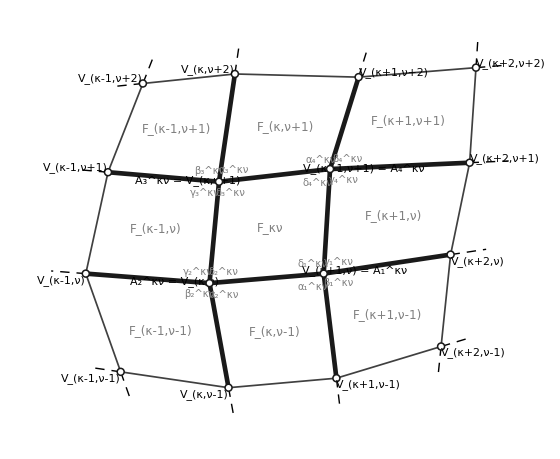
Given hypotheses:
The numbers with the superscript κν form the quadruples (α_1^κν, β_1^κν, γ_1^κν, δ_1^κν), (α_2^κν, β_2^κν, γ_2^κν, δ_2^κν), (α_3^κν, β_3^κν, γ_3^κν, δ_3^κν), (α_4^κν, β_4^κν, γ_4^κν, δ_4^κν) with the indices 1, 2, 3, 4, where
      (α_1^κν, β_1^κν, γ_1^κν, δ_1^κν) = (α, β, γ, δ),   α, β, γ, δ ∈ (0, π).
The pairs (κ, ν) with the same ν form the row ν; the numbers with every superscript of a row satisfy the relations of one of the cases below, the same for the whole row, and different rows may have different cases.

Definitions:
The pairs (κ-1, ν), (κ+1, ν), (κ, ν-1), (κ, ν+1) are the neighbouring pairs of (κ, ν). The numbers of neighbouring pairs are related by the following equations, with κ and ν shifted as needed:
(α_1^(κ,ν+1), β_1^(κ,ν+1), γ_1^(κ,ν+1), δ_1^(κ,ν+1)) = (δ_4^κν, γ_4^κν, β_4^κν, α_4^κν)
(α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) = (δ_3^κν, γ_3^κν, β_3^κν, α_3^κν)
(α_2^(κ+1,ν), β_2^(κ+1,ν), γ_2^(κ+1,ν), δ_2^(κ+1,ν)) = (β_1^κν, α_1^κν, δ_1^κν, γ_1^κν)
(α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) = (β_4^κν, α_4^κν, δ_4^κν, γ_4^κν)
A pair gets from a neighbouring pair two received quadruples by these equations, read in either direction, the reversal and the swap being their own inverses; from one received quadruple, the numbers of the pair are prescribed by the relations of the case of its row. The numbers of all pairs are prescribed pair by pair from one given pair, each time from an already prescribed neighbouring pair.
For illustration only, the figure shows where the numbers with the superscript κν would be flat angles in a net; no net is assumed.
-Graphics-

Given cases (the relations of the numbers with one superscript, which is omitted):
Case (a)  α_1==α_3==π-α_2==π-α_4,  β_1==β_3==π-β_2==π-β_4,  γ_1==γ_3==π-γ_2==π-γ_4,  δ_1==δ_3==π-δ_2==π-δ_4
Case (b)  α_1==β_4==π-α_2==π-β_3,  β_1==α_4==π-β_2==π-α_3,  γ_1==δ_4==π-γ_2==π-δ_3,  δ_1==γ_4==π-δ_2==π-γ_3
Case (c)  α_1==α_4==π-α_2==π-α_3,  β_1==β_4==π-β_2==π-β_3,  γ_1==γ_3==π-γ_2==π-γ_4,  δ_1==δ_3==π-δ_2==π-δ_4
Case (d)  α_1==β_4==π-α_2==π-β_3,  β_1==α_4==π-β_2==π-α_3,  γ_1==δ_3==π-γ_2==π-δ_4,  δ_1==γ_3==π-δ_2==π-γ_4
Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed.

We want to test the following claims ★ :
◼ Claim 1. Every neighbouring pair of (κ, ν) receives from it two quadruples that agree with the relations of the case of its row, whatever the cases of the rows.
◼ Claim 2. The numbers of the pair (κ+1, ν+1) prescribed through (κ+1, ν) and through (κ, ν+1) are the same, whatever the cases of the rows.
◼ Claim 3. The numbers prescribed for every pair do not depend on the neighbouring pair they are prescribed from.

Claim 1: the neighbouring pairs of (κ, ν)Verified
Verification: every neighbouring pair has as its two received quadruples those of (κ, ν) given by the equations, reversed or swapped; its numbers are prescribed, uniquely, from the first by the relations of its case, and its second received quadruple is compared with the prescribed one entry by entry, as linear identities in α, β, γ, δ. The neighbouring pairs in the rows ν-1 and ν+1 are taken in every case.
Case (a) in the row of (κ, ν):
    (κ+1, ν) (case (a)):  (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) prescribed = received = (π-β, π-α, π-δ, π-γ)  ☑
    (κ-1, ν) (case (a)):  (α_4^(κ-1,ν), β_4^(κ-1,ν), γ_4^(κ-1,ν), δ_4^(κ-1,ν)) prescribed = received = (β, α, δ, γ)  ☑
    (κ, ν+1) (case (a)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, β, α)  ☑
    (κ, ν+1) (case (b)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, β, α)  ☑
    (κ, ν+1) (case (c)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, β, α)  ☑
    (κ, ν+1) (case (d)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, β, α)  ☑
    (κ, ν-1) (case (a)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (b)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (c)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (d)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑

Case (b) in the row of (κ, ν):
    (κ+1, ν) (case (b)):  (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) prescribed = received = (α, β, γ, δ)  ☑
    (κ-1, ν) (case (b)):  (α_4^(κ-1,ν), β_4^(κ-1,ν), γ_4^(κ-1,ν), δ_4^(κ-1,ν)) prescribed = received = (π-α, π-β, π-γ, π-δ)  ☑
    (κ, ν+1) (case (a)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (π-γ, π-δ, π-α, π-β)  ☑
    (κ, ν+1) (case (b)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (π-γ, π-δ, π-α, π-β)  ☑
    (κ, ν+1) (case (c)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (π-γ, π-δ, π-α, π-β)  ☑
    (κ, ν+1) (case (d)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (π-γ, π-δ, π-α, π-β)  ☑
    (κ, ν-1) (case (a)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (b)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (c)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (d)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑

Case (c) in the row of (κ, ν):
    (κ+1, ν) (case (c)):  (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) prescribed = received = (β, α, π-δ, π-γ)  ☑
    (κ-1, ν) (case (c)):  (α_4^(κ-1,ν), β_4^(κ-1,ν), γ_4^(κ-1,ν), δ_4^(κ-1,ν)) prescribed = received = (π-β, π-α, δ, γ)  ☑
    (κ, ν+1) (case (a)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, π-β, π-α)  ☑
    (κ, ν+1) (case (b)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, π-β, π-α)  ☑
    (κ, ν+1) (case (c)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, π-β, π-α)  ☑
    (κ, ν+1) (case (d)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (δ, γ, π-β, π-α)  ☑
    (κ, ν-1) (case (a)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (b)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (c)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (d)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑

Case (d) in the row of (κ, ν):
    (κ+1, ν) (case (d)):  (α_3^(κ+1,ν), β_3^(κ+1,ν), γ_3^(κ+1,ν), δ_3^(κ+1,ν)) prescribed = received = (α, β, π-γ, π-δ)  ☑
    (κ-1, ν) (case (d)):  (α_4^(κ-1,ν), β_4^(κ-1,ν), γ_4^(κ-1,ν), δ_4^(κ-1,ν)) prescribed = received = (π-α, π-β, γ, δ)  ☑
    (κ, ν+1) (case (a)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (γ, δ, π-α, π-β)  ☑
    (κ, ν+1) (case (b)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (γ, δ, π-α, π-β)  ☑
    (κ, ν+1) (case (c)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (γ, δ, π-α, π-β)  ☑
    (κ, ν+1) (case (d)):  (α_2^(κ,ν+1), β_2^(κ,ν+1), γ_2^(κ,ν+1), δ_2^(κ,ν+1)) prescribed = received = (γ, δ, π-α, π-β)  ☑
    (κ, ν-1) (case (a)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (b)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (c)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
    (κ, ν-1) (case (d)):  (α_3^(κ,ν-1), β_3^(κ,ν-1), γ_3^(κ,ν-1), δ_3^(κ,ν-1)) prescribed = received = (π-δ, π-γ, π-β, π-α)  ☑
Together, these give Claim 1.

Claim 2: the pair (κ+1, ν+1)Verified
Verification: through (κ+1, ν), the numbers of that pair are prescribed from its received quadruple with the index 2 by the relations of the row ν, and those of (κ+1, ν+1) from the quadruple it receives from that pair with the index 1; through (κ, ν+1), the numbers of that pair are prescribed from its received quadruple with the index 1 by the relations of the row ν+1, and those of (κ+1, ν+1) from the quadruple it receives from that pair with the index 2. The two results are compared number by number, as linear identities in α, β, γ, δ; the quadruple with the index 1 is shown.
    row ν: (a),  row ν+1: (a):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, α, β)  ☑
    row ν: (a),  row ν+1: (b):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, α, β)  ☑
    row ν: (a),  row ν+1: (c):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, α, β)  ☑
    row ν: (a),  row ν+1: (d):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, α, β)  ☑
    row ν: (b),  row ν+1: (a):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (π-δ, π-γ, π-β, π-α)  ☑
    row ν: (b),  row ν+1: (b):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (π-δ, π-γ, π-β, π-α)  ☑
    row ν: (b),  row ν+1: (c):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (π-δ, π-γ, π-β, π-α)  ☑
    row ν: (b),  row ν+1: (d):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (π-δ, π-γ, π-β, π-α)  ☑
    row ν: (c),  row ν+1: (a):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, π-α, π-β)  ☑
    row ν: (c),  row ν+1: (b):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, π-α, π-β)  ☑
    row ν: (c),  row ν+1: (c):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, π-α, π-β)  ☑
    row ν: (c),  row ν+1: (d):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (γ, δ, π-α, π-β)  ☑
    row ν: (d),  row ν+1: (a):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (δ, γ, π-β, π-α)  ☑
    row ν: (d),  row ν+1: (b):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (δ, γ, π-β, π-α)  ☑
    row ν: (d),  row ν+1: (c):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (δ, γ, π-β, π-α)  ☑
    row ν: (d),  row ν+1: (d):  (α_1^(κ+1,ν+1), β_1^(κ+1,ν+1), γ_1^(κ+1,ν+1), δ_1^(κ+1,ν+1)) through (κ+1, ν) = through (κ, ν+1) = (δ, γ, π-β, π-α)  ☑
Together, these give Claim 2.

Claim 3: every pairVerified
Verification: by Claim 1, the numbers of a pair prescribed from a neighbouring pair agree with both quadruples it receives from it, and pass back to that neighbouring pair its own quadruples, because the reversal and the swap are their own inverses; by Claim 2, the prescriptions around every square of four pairs close up, and any two paths through neighbouring pairs between two pairs differ by such squares. So the numbers prescribed for a pair do not depend on the neighbouring pair they are prescribed from.
    every neighbouring pair receives quadruples that agree with the relations of the case of its row  ☑
    the prescriptions around every square of four pairs close up  ☑
    the numbers prescribed for every pair do not depend on the neighbouring pair they are prescribed from  ☑
Together, these give Claim 3.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[α,β,γ,δ,X,statusChip,smallChip,colTest,bullet,colRec,colPre,colNote,recW,preW,cases,caseCol,unk,relsOf,relDisp,prescribe,revOf,swapOf,quadDisp,vDisp,lstS,eqLine,vtx,sKN,sKN1,sK1N,sK1N1,sKm1N,sKNm1,pKN,pKN1,pK1N,pK1N1,pKm1N,pKNm1,okC1,okC2,resultsAll,figBlock,a1,b1,g1,d1,a2,b2,g2,d2,a3,b3,g3,d3,a4,b4,g4,d4];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
colTest=RGBColor[0.10,0.35,0.75];
bullet=Style["◼ ",12,colTest];
colRec=RGBColor[0.80,0.35,0.05];
colPre=RGBColor[0.00,0.50,0.30];
colNote=RGBColor[0.70,0.10,0.10];
recW=Style["received",Bold,colRec];
preW=Style["prescribed",Bold,colPre];
(*The numbers with a superscript kappa nu form the quadruples (alpha_i,beta_i,gamma_i,delta_i),i=1,2,3,4,of the pair (kappa,nu);no net is assumed.The relations of a case determine all four quadruples from any one of them:prescribe[c,k,Y] solves them by Solve for the numbers of case c whose quadruple with the index k is Y,and returns Missing[] unless the solution is unique.The pair (kappa,nu) has the independent symbols alpha,beta,gamma,delta as its quadruple with the index 1. Every check below is a linear identity in alpha,beta,gamma,delta,decided by Simplify.*)
X={α,β,γ,δ};
cases={"(a)","(b)","(c)","(d)"};
caseCol["(a)"]=RGBColor[0.55,0.33,0.10];
caseCol["(b)"]=RGBColor[0.00,0.45,0.25];
caseCol["(c)"]=RGBColor[0.10,0.45,0.65];
caseCol["(d)"]=RGBColor[0.55,0.15,0.25];
unk={{a1,b1,g1,d1},{a2,b2,g2,d2},{a3,b3,g3,d3},{a4,b4,g4,d4}};
relsOf["(a)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[3]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[4]]),b[[1]]-b[[3]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[4]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(b)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[4]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[3]]),d[[1]]-g[[4]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[3]])}];
relsOf["(c)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-a[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-a[[3]]),b[[1]]-b[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-b[[3]]),g[[1]]-g[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-g[[4]]),d[[1]]-d[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-d[[4]])}];
relsOf["(d)"][V_]:=Module[{a=V[[All,1]],b=V[[All,2]],g=V[[All,3]],d=V[[All,4]]},{a[[1]]-b[[4]],a[[1]]-(π-a[[2]]),a[[1]]-(π-b[[3]]),b[[1]]-a[[4]],b[[1]]-(π-b[[2]]),b[[1]]-(π-a[[3]]),g[[1]]-d[[3]],g[[1]]-(π-g[[2]]),g[[1]]-(π-d[[4]]),d[[1]]-g[[3]],d[[1]]-(π-d[[2]]),d[[1]]-(π-g[[4]])}];
relDisp["(a)"]={HoldForm[Subscript[α,1]==Subscript[α,3]==π-Subscript[α,2]==π-Subscript[α,4]],HoldForm[Subscript[β,1]==Subscript[β,3]==π-Subscript[β,2]==π-Subscript[β,4]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(b)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,4]==π-Subscript[γ,2]==π-Subscript[δ,3]],HoldForm[Subscript[δ,1]==Subscript[γ,4]==π-Subscript[δ,2]==π-Subscript[γ,3]]};
relDisp["(c)"]={HoldForm[Subscript[α,1]==Subscript[α,4]==π-Subscript[α,2]==π-Subscript[α,3]],HoldForm[Subscript[β,1]==Subscript[β,4]==π-Subscript[β,2]==π-Subscript[β,3]],HoldForm[Subscript[γ,1]==Subscript[γ,3]==π-Subscript[γ,2]==π-Subscript[γ,4]],HoldForm[Subscript[δ,1]==Subscript[δ,3]==π-Subscript[δ,2]==π-Subscript[δ,4]]};
relDisp["(d)"]={HoldForm[Subscript[α,1]==Subscript[β,4]==π-Subscript[α,2]==π-Subscript[β,3]],HoldForm[Subscript[β,1]==Subscript[α,4]==π-Subscript[β,2]==π-Subscript[α,3]],HoldForm[Subscript[γ,1]==Subscript[δ,3]==π-Subscript[γ,2]==π-Subscript[δ,4]],HoldForm[Subscript[δ,1]==Subscript[γ,3]==π-Subscript[δ,2]==π-Subscript[γ,4]]};
prescribe[c_,k_,Y_List]:=Module[{V=ReplacePart[unk,k->Y],sol},sol=Solve[Thread[relsOf[c][V]==0],Flatten[Delete[unk,k]]];If[Length[sol]==1,V/. First[sol],Missing[]]];
(*the equations between neighbouring pairs:the reversal between the rows nu and nu+1,the swap within a row;each is its own inverse*)
revOf[{a_,b_,g_,d_}]:={d,g,b,a};
swapOf[{a_,b_,g_,d_}]:={b,a,d,g};
(*displays:superscripts and pairs*)
sKN=Row[{κ,ν}];sKN1=Row[{κ,",",ν,"+1"}];sK1N=Row[{κ,"+1,",ν}];sK1N1=Row[{κ,"+1,",ν,"+1"}];sKm1N=Row[{κ,"-1,",ν}];sKNm1=Row[{κ,",",ν,"-1"}];
pKN=Row[{"(",κ,", ",ν,")"}];pKN1=Row[{"(",κ,", ",ν,"+1)"}];pK1N=Row[{"(",κ,"+1, ",ν,")"}];pK1N1=Row[{"(",κ,"+1, ",ν,"+1)"}];pKm1N=Row[{"(",κ,"-1, ",ν,")"}];pKNm1=Row[{"(",κ,", ",ν,"-1)"}];
lstS[i_,sup_]:={Subsuperscript[α,i,sup],Subsuperscript[β,i,sup],Subsuperscript[γ,i,sup],Subsuperscript[δ,i,sup]};
quadDisp[Y_List]:=TraditionalForm[Row[{"(",Row[Riffle[Y,", "]],")"}]];
vDisp[i_,sup_]:=quadDisp[lstS[i,sup]];
vtx[i_,sup_]:=TraditionalForm[Subsuperscript[A,i,sup]];
eqLine[lhs_,rhs_]:=Row[{lhs," = ",rhs}];
resultsAll={};
(*the illustration,drawn by the notebook:where the numbers with the superscript kappa nu would be flat angles in a net*)
figBlock=Module[{W,thin,thick,cont,dot,ang,lab,fl,faceCenter,angleAt,vName,sup,seg,grey=GrayLevel[0.5],bg=RGBColor[0.99,0.96,0.88]},W[0,0]={0.3,0.0};W[1,0]={3.7,-0.5};W[2,0]={7.1,-0.2};W[3,0]={10.4,0.8};
W[0,1]={-0.8,3.1};W[1,1]={3.1,2.8};W[2,1]={6.7,3.1};W[3,1]={10.7,3.7};
W[0,2]={-0.1,6.3};W[1,2]={3.4,6.0};W[2,2]={6.9,6.4};W[3,2]={11.3,6.6};
W[0,3]={1.0,9.1};W[1,3]={3.9,9.4};W[2,3]={7.8,9.3};W[3,3]={11.5,9.6};
faceCenter[i_,j_]:=(W[i,j]+W[i+1,j+1]+W[i+1,j]+W[i,j+1])/4;
sup[k_,n_]:=Row[{Which[k==-1,Row[{κ,"-1"}],k==0,κ,k==1,Row[{κ,"+1"}]],If[k==0&&n==0,"",","],Which[n==-1,Row[{ν,"-1"}],n==0,ν,n==1,Row[{ν,"+1"}]]}];
vName[i_,j_]:=Style[TraditionalForm[Subscript[V,Row[{Which[i==0,Row[{κ,"-1"}],i==1,κ,i==2,Row[{κ,"+1"}],i==3,Row[{κ,"+2"}]],",",Which[j==0,Row[{ν,"-1"}],j==1,ν,j==2,Row[{ν,"+1"}],j==3,Row[{ν,"+2"}]]}]]],11];
seg[p_,q_,t_]:=p+t (q-p);
thin={Thickness[0.0022],GrayLevel[0.25],Line[{W[0,0],W[1,0],W[2,0],W[3,0],W[3,1],W[3,2],W[3,3],W[2,3],W[1,3],W[0,3],W[0,2],W[0,1],W[0,0]}]};
thick={Thickness[0.006],GrayLevel[0.1],Line[{W[1,1],W[2,1],W[2,2],W[1,2],W[1,1]}],Line[{W[1,1],W[1,0]}],Line[{W[1,1],W[0,1]}],Line[{W[2,1],W[2,0]}],Line[{W[2,1],W[3,1]}],Line[{W[1,2],W[1,3]}],Line[{W[1,2],W[0,2]}],Line[{W[2,2],W[2,3]}],Line[{W[2,2],W[3,2]}]};
cont={Thickness[0.0018],Black,Dashing[{0.012,0.009}],Sequence@@Table[Line[{W[i,0],seg[W[i,0],W[i,1],-0.28]}],{i,0,3}],Sequence@@Table[Line[{W[i,3],seg[W[i,3],W[i,2],-0.28]}],{i,0,3}],Sequence@@Table[Line[{W[0,j],seg[W[0,j],W[1,j],-0.28]}],{j,0,3}],Sequence@@Table[Line[{W[3,j],seg[W[3,j],W[2,j],-0.28]}],{j,0,3}]};
dot={White,EdgeForm[{GrayLevel[0.1],Thickness[0.002]}],Sequence@@Table[Disk[W[i,j],0.11],{i,0,3},{j,0,3}]};
fl=Table[Text[Style[TraditionalForm[Subscript[F,sup[i-1,j-1]]],12,grey],faceCenter[i,j]],{i,0,2},{j,0,2}];
angleAt[i_,j_,ci_,cj_,letter_,k_]:=Text[Style[TraditionalForm[Subsuperscript[letter,k,sKN]],10,grey],seg[W[i,j],faceCenter[ci,cj],0.22]];
ang={angleAt[2,1,1,1,δ,1],angleAt[2,1,1,0,α,1],angleAt[2,1,2,1,γ,1],angleAt[2,1,2,0,β,1],angleAt[1,1,1,1,δ,2],angleAt[1,1,1,0,α,2],angleAt[1,1,0,1,γ,2],angleAt[1,1,0,0,β,2],angleAt[1,2,1,1,δ,3],angleAt[1,2,1,2,α,3],angleAt[1,2,0,1,γ,3],angleAt[1,2,0,2,β,3],angleAt[2,2,1,1,δ,4],angleAt[2,2,1,2,α,4],angleAt[2,2,2,1,γ,4],angleAt[2,2,2,2,β,4]};
lab={Text[Framed[Style[eqLine[vName[2,1],vtx[1,sKN]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[2,1],W[3,1],0.24],{-1,0}],Text[Framed[Style[eqLine[vtx[2,sKN],vName[1,1]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[1,1],W[0,1],0.28],{1,0}],Text[Framed[Style[eqLine[vtx[3,sKN],vName[1,2]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[1,2],W[0,2],0.28],{1,0}],Text[Framed[Style[eqLine[vName[2,2],vtx[4,sKN]],11],Background->bg,FrameStyle->White,FrameMargins->2],seg[W[2,2],W[3,2],0.24],{-1,0}],Text[vName[0,0],W[0,0],{1.3,1.1}],Text[vName[1,0],W[1,0],{1.1,1.1}],Text[vName[2,0],W[2,0],{-1.6,1.1}],Text[vName[3,0],W[3,0],{-1.4,1.1}],Text[vName[0,1],W[0,1],{1.3,1.1}],Text[vName[3,1],W[3,1],{-1.4,1.1}],Text[vName[0,2],W[0,2],{1.3,-1.1}],Text[vName[3,2],W[3,2],{-1.4,-1.1}],Text[vName[0,3],W[0,3],{1.3,-1.1}],Text[vName[1,3],W[1,3],{1.1,-1.1}],Text[vName[2,3],W[2,3],{-1.6,-1.1}],Text[vName[3,3],W[3,3],{-1.4,-1.1}]};
Graphics[{cont,thin,thick,fl,ang,dot,lab},ImageSize->560,PlotRangePadding->1.2,Background->None,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses:",Bold,14],Style[Row[{"The numbers with the superscript ",TraditionalForm[sKN]," form the quadruples ",vDisp[1,sKN],", ",vDisp[2,sKN],", ",vDisp[3,sKN],", ",vDisp[4,sKN]," with the indices 1, 2, 3, 4, where"}],13],Style[Row[{"      ",eqLine[vDisp[1,sKN],quadDisp[X]],",   α, β, γ, δ ∈ (0, π)."}],13],Style[Row[{"The pairs ",pKN," with the same ",ν," form the row ",ν,"; the numbers with every superscript of a row satisfy the relations of one of the cases below, the same for the whole row, and different rows may have different cases."}],13],"",Style["Definitions:",Bold,14],Style[Row[{"The pairs ",pKm1N,", ",pK1N,", ",pKNm1,", ",pKN1," are the neighbouring pairs of ",pKN,". The numbers of neighbouring pairs are related by the following equations, with ",κ," and ",ν," shifted as needed:"}],13],Style[Column[{eqLine[vDisp[1,sKN1],quadDisp[revOf[lstS[4,sKN]]]],eqLine[vDisp[2,sKN1],quadDisp[revOf[lstS[3,sKN]]]],eqLine[vDisp[2,sK1N],quadDisp[swapOf[lstS[1,sKN]]]],eqLine[vDisp[3,sK1N],quadDisp[swapOf[lstS[4,sKN]]]]},Alignment->Left,Spacings->0.6],13],Style[Row[{"A pair gets from a neighbouring pair two ",recW," quadruples by these equations, read in either direction, the reversal and the swap being their own inverses; from one received quadruple, the numbers of the pair are ",preW," by the relations of the case of its row. The numbers of all pairs are prescribed pair by pair from one given pair, each time from an already prescribed neighbouring pair."}],13],Style[Row[{Style["For illustration only",Bold,colNote],", the figure shows where the numbers with the superscript ",TraditionalForm[sKN]," would be flat angles in a net; ",Style["no net is assumed.",Bold,colNote]}],13],figBlock,"",Style["Given cases (the relations of the numbers with one superscript, which is omitted):",Bold,14],Sequence@@Table[Style[Row[{Style["Case "<>c<>"  ",Bold,13],Row[Riffle[TraditionalForm/@relDisp[c],",  "]]}],13,caseCol[c]],{c,cases}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Row[{bullet,Style[Row[{"Claim 1. Every neighbouring pair of ",pKN," receives from it two quadruples that agree with the relations of the case of its row, whatever the cases of the rows."}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"Claim 2. The numbers of the pair ",pK1N1," prescribed through ",pK1N," and through ",pKN1," are the same, whatever the cases of the rows."}],Bold,13,colTest]}],Row[{bullet,Style["Claim 3. The numbers prescribed for every pair do not depend on the neighbouring pair they are prescribed from.",Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=RGBColor[0.10,0.35,0.75],rows={},ok=True,ind="    "},Do[Module[{G=prescribe[c,1,X],tests,lines},(*each test:the superscript and the name of the neighbouring pair,its case,the index it is prescribed from,the quadruple received there,the other index,the quadruple received there*)tests=Join[{{sK1N,pK1N,c,2,swapOf[G[[1]]],3,swapOf[G[[4]]]},{sKm1N,pKm1N,c,1,swapOf[G[[2]]],4,swapOf[G[[3]]]}},Table[{sKN1,pKN1,cn,1,revOf[G[[4]]],2,revOf[G[[3]]]},{cn,cases}],Table[{sKNm1,pKNm1,cn,4,revOf[G[[1]]],3,revOf[G[[2]]]},{cn,cases}]];
lines=Table[Module[{B=prescribe[t[[3]],t[[4]],t[[5]]],okm},okm=!MissingQ[B]&&And@@Table[Simplify[B[[t[[6]],j]]-t[[7,j]]]===0,{j,4}];
ok=ok&&okm;
Row[{ind,t[[2]],Style[" (case "<>t[[3]]<>"):  ",Bold,caseCol[t[[3]]]],vDisp[t[[6]],t[[1]]]," ",preW," = ",recW," = ",quadDisp[t[[7]]],"  ",smallChip[okm]}]],{t,tests}];
rows=Join[rows,{Style[Row[{Style["Case "<>c<>" in the row of ",Bold,caseCol[c]],pKN,":"}],13],Style[Column[lines,Spacings->0.4],13],""}]],{c,cases}];
okC1=ok;AppendTo[resultsAll,ok];
Print[Panel[Column[Join[{Row[{Style[Row[{"Claim 1: the neighbouring pairs of ",pKN}],Bold,15,col],Spacer[20],statusChip[ok]}],Style[Row[{"Verification: every neighbouring pair has as its two ",recW," quadruples those of ",pKN," given by the equations, reversed or swapped; its numbers are ",preW,", uniquely, from the first by the relations of its case, and its second received quadruple is compared with the prescribed one entry by entry, as linear identities in α, β, γ, δ. The neighbouring pairs in the rows ",ν,"-1 and ",ν,"+1 are taken in every case."}],Bold,13]},Most[rows],{Style["Together, these give Claim 1.",13]}],Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=RGBColor[0.50,0.20,0.65],lines={},ok=True,ind="    "},Do[Module[{G=prescribe[c,1,X],R,Ab,Q1,Q2,okm},R=prescribe[c,2,swapOf[G[[1]]]];
Ab=prescribe[cu,1,revOf[G[[4]]]];
Q1=prescribe[cu,1,revOf[R[[4]]]];
Q2=prescribe[cu,2,swapOf[Ab[[1]]]];
okm=!MissingQ[Q1]&&!MissingQ[Q2]&&And@@Flatten[Table[Simplify[Q1[[i,j]]-Q2[[i,j]]]===0,{i,4},{j,4}]];
ok=ok&&okm;
AppendTo[lines,Row[{ind,Style[Row[{"row ",ν,": ",Style[c,caseCol[c]],",  row ",ν,"+1: ",Style[cu,caseCol[cu]],":  "}],Bold],vDisp[1,sK1N1]," through ",pK1N," = through ",pKN1," = ",quadDisp[Q1[[1]]],"  ",smallChip[okm]}]]],{c,cases},{cu,cases}];
okC2=ok;AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style[Row[{"Claim 2: the pair ",pK1N1}],Bold,15,col],Spacer[20],statusChip[ok]}],Style[Row[{"Verification: through ",pK1N,", the numbers of that pair are ",preW," from its ",recW," quadruple with the index 2 by the relations of the row ",ν,", and those of ",pK1N1," from the quadruple it receives from that pair with the index 1; through ",pKN1,", the numbers of that pair are prescribed from its received quadruple with the index 1 by the relations of the row ",ν,"+1, and those of ",pK1N1," from the quadruple it receives from that pair with the index 2. The two results are compared number by number, as linear identities in α, β, γ, δ; the quadruple with the index 1 is shown."}],Bold,13],Style[Column[lines,Spacings->0.4],13],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=RGBColor[0.00,0.55,0.55],chk,ind="    "},chk=okC1&&okC2;AppendTo[resultsAll,chk];
Print[Panel[Column[{Row[{Style["Claim 3: every pair",Bold,15,col],Spacer[20],statusChip[chk]}],Style["Verification: by Claim 1, the numbers of a pair prescribed from a neighbouring pair agree with both quadruples it receives from it, and pass back to that neighbouring pair its own quadruples, because the reversal and the swap are their own inverses; by Claim 2, the prescriptions around every square of four pairs close up, and any two paths through neighbouring pairs between two pairs differ by such squares. So the numbers prescribed for a pair do not depend on the neighbouring pair they are prescribed from.",Bold,13],Style[Column[{Row[{ind,"every neighbouring pair receives quadruples that agree with the relations of the case of its row  ",smallChip[okC1]}],Row[{ind,"the prescriptions around every square of four pairs close up  ",smallChip[okC2]}],Row[{ind,"the numbers prescribed for every pair do not depend on the neighbouring pair they are prescribed from  ",smallChip[chk]}]},Spacings->0.5],13],Style["Together, these give Claim 3.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

## Section 4

## Results of Section 4 are used in the proof of Lemma 18

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[plusT,minusT,qT,dT,cotSD,yS1,zS1,yS2,zS2,ytS1,ztS1,ytS2,ztS2,epS1,epS2,eS1,eS2,uS,xS1,ddS,supS,supG,tilO,pairsInt,statusChip,smallChip,givenChip,colTest,cols,bullet,ind,vlift,idxB,ptB,pt,edg,evec,nv,wv,tld,gk,thI,bx,cotSqTag,cotTag,mulR,absR,frac,caseDef,note,firstBase,nrow,prow,hrow,vgap,vgrid,iv,trigNames,simpleBoxQ,trigBoxRule,disp,dispRule,ptBS,ptS,edgS,evecS,gkS,thK,thKS,nvK,nvKS,tilD,tilDS,vLab,quadD,tupD,itl,lab,ren,renQ,subQ,qP,qS,al,be,ga,de,qa,qb,qg,qd,sgQ,ratQ,ra,rb,rc,rd,yv,zv,uv,til,t,e0,e1,e2,u,x1,y1,z1,y2,z2,yt1,zt1,yt2,zt2,ep1,ep2,dd,cotF,qQ,cotP,cotFS,qQS,cotStar,subS,pairs,w1,w2,w3,lam,mu,nuF,vB1,vC1,vA4,vA3,vB2,vC2,figPair,okC1,okC2,okC3,okC4,resultsAll,blt];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];ind="    ";vlift=0.16;
(*a bullet line of a claim,with one relation*)
blt[e_]:=Row[{bullet,Style[e,Bold,13,colTest]}];
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
edg[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptB[s1,i1],ptB[s2,i2]}]];
evec[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptB[s1,i1],ptB[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
nv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
wv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["w",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
tld[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
cotSqTag[t_]:=DisplayForm[RowBox[{SuperscriptBox["cot","2"],"(",bx[t],"/","2",")"}]];
cotTag[t_]:=DisplayForm[RowBox[{"cot","(",bx[t],"/","2",")"}]];
mulR[args___]:=Row[Riffle[{args}," "]];absR[e_]:=Row[{"|",e,"|"}];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
caseDef[lhs_,rows_]:=DisplayForm[RowBox[{bx[lhs]," ∶= ",StyleBox["{",SpanMaxSize->Infinity],GridBox[Map[bx,rows,{2}],ColumnAlignments->Left,ColumnSpacings->1.6,RowSpacings->0.9]}]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
(*a numbered line,an unnumbered line (for a name),and a heading line of a block*)
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed index i is an italic string as well*)
iv=Style["i",Italic];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
(*a starred label marks the polyhedron with the second central face;indices given as strings are set upright*)
ptBS[s_,i_]:=SubsuperscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i],"*"];ptS[s_,i_]:=DisplayForm[ptBS[s,i]];
edgS[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptBS[s1,i1],ptBS[s2,i2]}]];
evecS[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptBS[s1,i1],ptBS[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
gkS[g_,i_]:=DisplayForm[SubsuperscriptBox[g,idxB[i],"*"]];
thK[k_String]:=DisplayForm[SubscriptBox["θ",k]];thKS[k_String]:=DisplayForm[SubsuperscriptBox["θ",k,"*"]];
nvK[k_String]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],k]];
nvKS[k_String]:=DisplayForm[SubsuperscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],k,"*"]];
tilD[s_,i_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"],idxB[i]]];
tilDS[s_,i_]:=DisplayForm[SubsuperscriptBox[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"],idxB[i],"*"]];
itl[s_]:=DisplayForm[StyleBox[s,FontSlant->"Italic"]];
supS[s_]:=DisplayForm[SuperscriptBox[StyleBox[s,FontSlant->"Italic"],"*"]];supG[g_]:=DisplayForm[SuperscriptBox[g,"*"]];
tilO[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
tupD[l_List]:=Row[{"(",Row[Riffle[disp/@l,", "]],")"}];
quadD[l_List]:=Row[{"(",Row[Riffle[l,", "]],")"}];
(*a vertex label V,given by its offsets {a,b} from (kappa,nu)*)
vLab[{a_,b_}]:=Module[{f},f[s_,k_]:=s<>Which[k==0,"",k>0,"+"<>ToString[k],True,"−"<>ToString[-k]];DisplayForm[SubscriptBox[StyleBox["V",FontSlant->"Italic"],RowBox[{f["κ",a],",",f["ν",b]}]]]];
(*the formulas are displayed through these strings,so that no value of a symbol enters the display*)
dispRule={al[k_]:>Subscript["α",k],be[k_]:>Subscript["β",k],ga[k_]:>Subscript["γ",k],de[k_]:>Subscript["δ",k],t->Style["t",Italic],u->Style["u",Italic],e0->Subscript[Style["e",Italic],0],e1->Subscript[Style["e",Italic],1],e2->Subscript[Style["e",Italic],2],x1->Subscript[Style["x",Italic],1],y1->Subscript[Style["y",Italic],1],z1->Subscript[Style["z",Italic],1],y2->Subscript[Style["y",Italic],2],z2->Subscript[Style["z",Italic],2],yt1->Subscript[OverTilde[Style["y",Italic]],1],zt1->Subscript[OverTilde[Style["z",Italic]],1],yt2->Subscript[OverTilde[Style["y",Italic]],2],zt2->Subscript[OverTilde[Style["z",Italic]],2],ep1->Subscript["ε",1],ep2->Subscript["ε",2],dd->Row[{Style["D",Italic],"(",Subscript[Style["x",Italic],1],", ",Style["t",Italic],")"}]};

(*the starred quantities,for display only*)
dispRule=Join[dispRule,{yS1->Subsuperscript[Style["y",Italic],1,"*"],zS1->Subsuperscript[Style["z",Italic],1,"*"],yS2->Subsuperscript[Style["y",Italic],2,"*"],zS2->Subsuperscript[Style["z",Italic],2,"*"],ytS1->Subsuperscript[OverTilde[Style["y",Italic]],1,"*"],ztS1->Subsuperscript[OverTilde[Style["z",Italic]],1,"*"],ytS2->Subsuperscript[OverTilde[Style["y",Italic]],2,"*"],ztS2->Subsuperscript[OverTilde[Style["z",Italic]],2,"*"],epS1->Subsuperscript["ε",1,"*"],epS2->Subsuperscript["ε",2,"*"],eS1->Subsuperscript[Style["e",Italic],1,"*"],eS2->Subsuperscript[Style["e",Italic],2,"*"],uS->Superscript[Style["u",Italic],"*"],xS1->Subsuperscript[Style["x",Italic],1,"*"],ddS->Row[{Style["D",Italic],"(",Subsuperscript[Style["x",Italic],1,"*"],", ",Style["t",Italic],")"}]}];
(*the formulas as they are displayed,held so that their terms keep the order in which they are written;the checks below use the same formulas released*)
plusT[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=HoldForm[a1 (t Sqrt[a6 a2 a3 (1+a4) (1+a6 a4)]+e0 a5 Sqrt[a6 a3 a4 a7])/(a3 a6 (a4+a2 t^2))];
minusT[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=HoldForm[a1 (t Sqrt[a6 a2 a3 (1+a4) (1+a6 a4)]-e0 a5 Sqrt[a6 a3 a4 a7])/(a3 a6 (a4+a2 t^2))];
qT[a6_,a2_]:=HoldForm[e0 Sqrt[(1+a6 a2) (a2 t^2-1)/((1+a2) (1-a6 a2 t^2))]];
dT[a6_,a2_]:=HoldForm[(a2 t^2-1) (1-a6 a2 t^2)];

(*the vertices of the block with the central face F(kappa+a0,nu+b0),as offsets from (kappa,nu),in the labelling of the 3 x 3 net*)
lab[{a0_,b0_}]:=Module[{add=#+{a0,b0}&},<|"A"->add/@{{1,0},{0,0},{0,1},{1,1}},"B"->add/@{{1,-1},{0,-1},{0,2},{1,2}},"C"->add/@{{2,0},{-1,0},{-1,1},{2,1}}|>];
(*the cyclic permutation of the indices by j:A_(i+j) becomes A_i,and,for odd j,B and C exchange their roles,and so do alpha and gamma*)
ren[l_,j_]:=Module[{o=Mod[Range[4]+j,4,1]},<|"A"->l["A"][[o]],"B"->If[OddQ[j],l["C"],l["B"]][[o]],"C"->If[OddQ[j],l["B"],l["C"]][[o]]|>];
renQ[qf_,j_,i_]:=Module[{q=qf[Mod[i+j,4,1]]},If[OddQ[j],q[[{3,2,1,4}]],q]];
subQ[q_List]:=q[[{4,3,2,1}]];
qP[i_]:={al[i],be[i],ga[i],de[i]};
(*the flat angles of the second block at the shared vertices,before the renumbering,in the two cases*)
qS[1]=<|1->{de[4],ga[4],be[4],al[4]},2->{de[3],ga[3],be[3],al[3]}|>;
qS[2]=<|2->{be[1],al[1],de[1],ga[1]},3->{be[4],al[4],de[4],ga[4]}|>;
(*the quantities of one quadruple (alpha,beta,gamma,delta)*)
sgQ[q_]:=Total[q]/2;ratQ[q_,k_]:=Sin[q[[k]]]/Sin[sgQ[q]-q[[k]]];
til[w_,uu_]:=-(1+w)/(1+uu w);
(*the dihedral angles given by the flexion formulas,for the parameter t and the sign e0*)
cotF[ep_,yy_,zz_,sg_]:=ep (t Sqrt[u x1 yy (1+zz) (1+u zz)]+sg e0 Sqrt[u yy zz dd])/(yy u (zz+x1 t^2));
qQ=(1+u x1) (x1 t^2-1)/((1+x1) (1-u x1 t^2));
cotP=<|"1"->t,"2"->cotF[ep2,y2,z2,e2],"4"->cotF[ep1,y1,z1,-e1],"11"->cotF[ep1,yt1,zt1,-e1],"12"->cotF[ep2,yt2,zt2,e2],"41"->e0 Sqrt[qQ]/e1,"22"->-e0 Sqrt[qQ]/e2|>;
(*the same formulas for the second block,in its own quantities,as they are displayed in the given panel*)
cotFS[ep_,yy_,zz_,sg_]:=ep (t Sqrt[uS xS1 yy (1+zz) (1+uS zz)]+sg e0 Sqrt[uS yy zz ddS])/(yy uS (zz+xS1 t^2));
qQS=(1+uS xS1) (xS1 t^2-1)/((1+xS1) (1-uS xS1 t^2));
cotStar=<|"1"->t,"2"->cotFS[epS2,yS2,zS2,eS2],"4"->cotFS[epS1,yS1,zS1,-eS1],"11"->cotFS[epS1,ytS1,ztS1,-eS1],"12"->cotFS[epS2,ytS2,ztS2,eS2],"41"->e0 Sqrt[qQS]/eS1,"22"->-e0 Sqrt[qQS]/eS2|>;
(*the quantities of the second block replaced as in Claim 2,and its signs by the given relation*)
subS={uS->u,xS1->x1,ddS->dd,yS2->yt1,zS2->zt1,epS2->ep1,yS1->yt2,zS1->zt2,epS1->ep2,ytS2->y1,ztS2->z1,ytS1->y2,ztS1->z2,eS1->-e2,eS2->-e1};
pairs={{"1","1"},{"2","11′"},{"4","12′"},{"11′","2"},{"12′","4"},{"22′","41′"},{"41′","22′"}};
pairsInt={{"1","1"},{"2","11"},{"4","12"},{"11","2"},{"12","4"},{"22","41"},{"41","22"}};
(*the formulas of the second block after the replacement,as they are displayed*)
cotSD=<|"1"->HoldForm[t],"2"->minusT[ep1,x1,yt1,zt1,e1,u,dd],"4"->plusT[ep2,x1,yt2,zt2,e2,u,dd],"11"->plusT[ep2,x1,y2,z2,e2,u,dd],"12"->minusT[ep1,x1,y1,z1,e1,u,dd],"41"->HoldForm[-e0 Sqrt[(1+u x1) (x1 t^2-1)/((1+x1) (1-u x1 t^2))]/e2],"22"->HoldForm[e0 Sqrt[(1+u x1) (x1 t^2-1)/((1+x1) (1-u x1 t^2))]/e1]|>;
resultsAll={};
(*the figure:the two blocks after the renumbering,flexed and seen from above at an angle,with the dihedral angles along the seven edges at the shared vertices;the faces are the parallelograms of a translation surface,so they are planar;the numbers of the drawing enter no verification*)
figPair=Module[{F,G,V,faceCol,faces,thick,cen,arcAt,arcData,arcs,dots,labData,labs,blue=RGBColor[0.10,0.35,0.75],purple=RGBColor[0.50,0.20,0.65],grey=GrayLevel[0.45],orange=RGBColor[0.85,0.45,0.05]},F[i_]:={i,0.06 i,0.30 (i-0.5)^2};G[j_]:={0.18 j,0.92 j,-0.22 (j-1)^2};
V[{i_,j_}]:=F[i]+G[j];
faceCol[{i_,j_}]:=Which[j==-1,RGBColor[0.80,0.87,0.97],j==2,RGBColor[0.88,0.80,0.95],MemberQ[{{0,0},{0,1}},{i,j}],RGBColor[0.70,0.86,0.64],True,RGBColor[0.84,0.93,0.80]];
faces=Flatten[Table[{FaceForm[faceCol[{i,j}]],Polygon[V/@{{i,j},{i+1,j},{i+1,j+1},{i,j+1}}]},{i,-1,1},{j,-1,2}],1];
thick={GrayLevel[0.08],AbsoluteThickness[3.2],Line[V/@#]&/@{{{0,1},{1,1}},{{0,1},{0,0}},{{0,1},{0,2}},{{0,1},{-1,1}},{{1,1},{1,0}},{{1,1},{1,2}},{{1,1},{2,1}}}};
cen[f_]:=Mean[V/@{f,f+{1,0},f+{1,1},f+{0,1}}];
(*an arc from one face to the other,around the midpoint of their common edge,and a point for its label*)arcAt[{p_,q_},{f1_,f2_},r_]:=Module[{P=V[p],R=V[q],M,e,d1,d2,w,ph},M=(P+R)/2;e=Normalize[R-P];
d1=Normalize[(cen[f1]-M)-((cen[f1]-M).e) e];d2=Normalize[(cen[f2]-M)-((cen[f2]-M).e) e];
ph=ArcCos[Clip[d1.d2,{-1,1}]];w=Normalize[d2-(d2.d1) d1];
{Table[M+r (Cos[s] d1+Sin[s] w),{s,0,ph,ph/24}],M+(r+0.17) (Cos[ph/2] d1+Sin[ph/2] w)}];
(*each arc:its edge,the two faces,its names,and the offset of its label;an offset {x,y} moves the label by x half-widths to the left and y half-heights down*)arcData={{{{0,1},{1,1}},{{0,0},{0,1}},{thK["1"],thKS["1"]},{0,0}},{{{0,1},{0,0}},{{-1,0},{0,0}},{thK["4"],thKS["12′"]},{0.3,0}},{{{0,1},{0,2}},{{-1,1},{0,1}},{thK["11′"],thKS["2"]},{0,-0.3}},{{{0,1},{-1,1}},{{-1,0},{-1,1}},{thK["41′"],thKS["22′"]},{0,1.2}},{{{1,1},{1,0}},{{0,0},{1,0}},{thK["2"],thKS["11′"]},{-0.3,0.6}},{{{1,1},{1,2}},{{0,1},{1,1}},{thK["12′"],thKS["4"]},{0,-0.3}},{{{1,1},{2,1}},{{1,0},{1,1}},{thK["22′"],thKS["41′"]},{0,1.2}}};
arcs=Function[ad,Module[{g=arcAt[ad[[1]],ad[[2]],0.22]},{{orange,AbsoluteThickness[2.2],Line[g[[1]]]},Text[Style[Row[{Style[ad[[3,1]],blue],Style[" = ",grey],Style[ad[[3,2]],purple]}],11],g[[2]],ad[[4]]]}]]/@arcData;
(*each vertex:its position in the grid,its labels in the two blocks,and the offset of its label,as for the arcs*)labData={{{0,1},pt["A",1],ptS["A",2],{1.35,0.75}},{{1,1},pt["A",2],ptS["A",1],{-1.0,1.6}},{{1,0},pt["A",3],ptS["B",1],{-1.1,1.6}},{{0,0},pt["A",4],ptS["B",2],{1.45,1.0}},{{0,2},pt["B",1],ptS["A",3],{1.1,-0.9}},{{1,2},pt["B",2],ptS["A",4],{-1.1,-0.9}},{{-1,1},pt["C",1],ptS["C",2],{1.3,0}},{{2,1},pt["C",2],ptS["C",1],{-1.3,0}},{{1,-1},pt["B",3],None,{0,2.0}},{{0,-1},pt["B",4],None,{0,2.0}},{{2,0},pt["C",3],None,{-1.7,0}},{{-1,0},pt["C",4],None,{1.8,0}},{{0,3},None,ptS["B",3],{0,-2.0}},{{1,3},None,ptS["B",4],{0,-2.0}},{{-1,2},None,ptS["C",3],{1.8,0}},{{2,2},None,ptS["C",4],{-1.7,0}}};
dots={GrayLevel[0.1],PointSize[0.009],Point[V[#[[1]]]&/@labData]};
labs=Text[Style[Row[Riffle[DeleteCases[{If[#[[2]]===None,None,Style[#[[2]],blue]],If[#[[3]]===None,None,Style[#[[3]],purple]]},None],Style[" = ",grey]]],12],V[#[[1]]],#[[4]]]&/@labData;
Graphics3D[{EdgeForm[{GrayLevel[0.45],AbsoluteThickness[0.8]}],Opacity[0.85],faces,Opacity[1],thick,arcs,dots,labs,Text[Style[DisplayForm[StyleBox["Q",FontSlant->"Italic"]],14,Bold,blue],cen[{0,0}]],Text[Style[DisplayForm[SuperscriptBox[StyleBox["Q",FontSlant->"Italic"],"*"]],14,Bold,purple],cen[{0,1}]]},Boxed->False,Lighting->"Neutral",ViewPoint->{0.5,-1.3,3.0},ViewVertical->{0,0,1},ImageSize->700,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)(*PART 2:GIVEN PANEL*)(* ============================================================*)Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style[Row[{"two 3 × 3 blocks, ",itl["Q"]," and ",supS["Q"],", whose central faces share an edge; a star marks the labels and quantities of ",supS["Q"]}],13],Style[Grid[{{"case 1:",Row[{"central faces ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ","ν"}]]]," and ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ",",","ν+1"}]]],";   ",itl["Q"]," renumbered by the cyclic permutation of the indices by 2, ",supS["Q"]," kept"}]},{"case 2:",Row[{"central faces ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ","ν"}]]]," and ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ+1",",","ν"}]]],";   ",itl["Q"]," renumbered by the cyclic permutation of the indices by 3, and ",supS["Q"]," by the cyclic permutation of the indices by 1"}]}},Alignment->Left,Spacings->{2,0.6}],13],note[Row[{"the cyclic permutation by j relabels ",pt["A","i+j"]," as ",pt["A","i"],", with the indices modulo 4 and values in {1, …, 4}, and ",pt["e","i+j"]," as ",pt["e","i"],"; for odd j, B and C exchange their roles, and so do α and γ"}]],Style[Row[{"vertex labels of the block with the central face ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ","ν"}]]],", before the renumbering:"}],13],Style[Grid[{{Row[{pt["A",1],", ",pt["A",2],", ",pt["A",3],", ",pt["A",4]}]," = ",Row[Riffle[vLab/@{{1,0},{0,0},{0,1},{1,1}},", "]]},{Row[{pt["B",1],", ",pt["B",2],", ",pt["B",3],", ",pt["B",4]}]," = ",Row[Riffle[vLab/@{{1,-1},{0,-1},{0,2},{1,2}},", "]]},{Row[{pt["C",1],", ",pt["C",2],", ",pt["C",3],", ",pt["C",4]}]," = ",Row[Riffle[vLab/@{{2,0},{-1,0},{-1,1},{2,1}},", "]]}},Alignment->Left,Spacings->{0.6,0.5}],13],note[Row[{"the block with the central face ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′","ν′"}]]]," is labelled in the same way, with κ′ and ν′ in place of κ and ν"}]],note[Row[{"the labels ",DisplayForm[SubscriptBox[StyleBox["V",FontSlant->"Italic"],RowBox[{StyleBox["i",FontSlant->"Italic"],StyleBox["j",FontSlant->"Italic"]}]]]," are pairs of indices, and no net is assumed; a vertex of ",itl["Q"]," and one of ",supS["Q"]," are the same vertex when they have the same label"}]],Style["flat angles at the shared vertices, before the renumbering:",13],Style[Grid[{{"case 1:",Row[{quadD[{gkS["α",1],gkS["β",1],gkS["γ",1],gkS["δ",1]}]," = ",quadD[{gk["δ",4],gk["γ",4],gk["β",4],gk["α",4]}]}]},{"",Row[{quadD[{gkS["α",2],gkS["β",2],gkS["γ",2],gkS["δ",2]}]," = ",quadD[{gk["δ",3],gk["γ",3],gk["β",3],gk["α",3]}]}]},{"case 2:",Row[{quadD[{gkS["α",2],gkS["β",2],gkS["γ",2],gkS["δ",2]}]," = ",quadD[{gk["β",1],gk["α",1],gk["δ",1],gk["γ",1]}]}]},{"",Row[{quadD[{gkS["α",3],gkS["β",3],gkS["γ",3],gkS["δ",3]}]," = ",quadD[{gk["β",4],gk["α",4],gk["δ",4],gk["γ",4]}]}]}},Alignment->Left,Spacings->{2,0.6}],13],Style["signs after the renumbering:",13],Style[Row[{ptS["e",1]," = −",pt["e",2]}],13],Style[Row[{ptS["e",2]," = −",pt["e",1]}],13],note[Row[{"if necessary, after replacing all signs of ",supS["Q"]," and its sign ",pt["e",0]," by their negatives, which leaves its polyhedra unchanged; both blocks are taken with the same parameter ",itl["t"]," and the same sign ",pt["e",0]}]],Spacer[{0,8}],Style["Quantities of a quadruple (α, β, γ, δ):",Bold,14],Style[Column[{Row[{"σ = (α + β + γ + δ)/2",",   ","ε = sign(sin σ)"}],Row[{itl["a"]," = ",frac[Row[{"sin α"}],Row[{"sin(σ − α)"}]],",   ",itl["b"]," = ",frac[Row[{"sin β"}],Row[{"sin(σ − β)"}]],",   ",itl["c"]," = ",frac[Row[{"sin γ"}],Row[{"sin(σ − γ)"}]],",   ",itl["d"]," = ",frac[Row[{"sin δ"}],Row[{"sin(σ − δ)"}]]}],Row[{itl["M"]," = ",mulR[itl["a"],itl["b"],itl["c"],itl["d"]],",   ",itl["r"]," = ",mulR[itl["a"],itl["d"]],",   ",itl["s"]," = ",mulR[itl["c"],itl["d"]],",   ",itl["f"]," = ",mulR[itl["a"],itl["c"]]}],Row[{itl["x"]," = ",frac[Row[{"1"}],Row[{itl["r"]," − 1"}]],",   ",itl["y"]," = ",frac[Row[{"1"}],Row[{itl["s"]," − 1"}]],",   ",itl["z"]," = ",frac[Row[{"1"}],Row[{itl["f"]," − 1"}]]}]},Spacings->0.9],13],Spacer[{0,4}],Style[Column[{Row[{"the index i marks the quadruple at ",pt["A","i"]}],Row[{"in each block,  ",pt["M",1]," = … = ",pt["M",4]," = ",itl["M"]}],Row[{itl["u"]," = 1 − ",itl["M"]}],Row[{"in each block,  ",pt["r",1]," = ",pt["r",2]}],Row[{"hence, in each block,  ",pt["x",1]," = ",pt["x",2]}],Row[{tilD["y","i"]," = −",frac[Row[{"1 + ",pt["y","i"]}],Row[{"1 + ",mulR[itl["u"],pt["y","i"]]}]]}],Row[{tilD["z","i"]," = −",frac[Row[{"1 + ",pt["z","i"]}],Row[{"1 + ",mulR[itl["u"],pt["z","i"]]}]]}]},Spacings->0.9],13],Spacer[{0,8}],Style[Row[{"Dihedral angles of ",itl["Q"]," for the parameter ",itl["t"]," and the sign ",pt["e",0],", after the renumbering:"}],Bold,14],Style[Column[{Row[{cotTag[thK["1"]]," = ",itl["t"]}],Row[{cotTag[thK["2"]]," = ",disp[plusT[ep2,x1,y2,z2,e2,u,dd]]}],Row[{cotTag[thK["4"]]," = ",disp[minusT[ep1,x1,y1,z1,e1,u,dd]]}],Row[{cotTag[thK["11′"]]," = ",disp[minusT[ep1,x1,yt1,zt1,e1,u,dd]]}],Row[{cotTag[thK["12′"]]," = ",disp[plusT[ep2,x1,yt2,zt2,e2,u,dd]]}],Row[{pt["e",1]," ",cotTag[thK["41′"]]," = −",pt["e",2]," ",cotTag[thK["22′"]]," = ",disp[qT[u,x1]]}],Row[{"where  ",disp[dd]," = ",disp[dT[u,x1]]}]},Spacings->1.1],13],Spacer[{0,14}],Style[Row[{"Dihedral angles of ",supS["Q"]," for the parameter ",itl["t"]," and the sign ",pt["e",0],", after the renumbering:"}],Bold,14],Style[Column[{Row[{cotTag[thKS["1"]]," = ",itl["t"]}],Row[{cotTag[thKS["2"]]," = ",disp[plusT[epS2,xS1,yS2,zS2,eS2,uS,ddS]]}],Row[{cotTag[thKS["4"]]," = ",disp[minusT[epS1,xS1,yS1,zS1,eS1,uS,ddS]]}],Row[{cotTag[thKS["11′"]]," = ",disp[minusT[epS1,xS1,ytS1,ztS1,eS1,uS,ddS]]}],Row[{cotTag[thKS["12′"]]," = ",disp[plusT[epS2,xS1,ytS2,ztS2,eS2,uS,ddS]]}],Row[{ptS["e",1]," ",cotTag[thKS["41′"]]," = −",ptS["e",2]," ",cotTag[thKS["22′"]]," = ",disp[qT[uS,xS1]]}],Row[{"where  ",disp[ddS]," = ",disp[dT[uS,xS1]]}]},Spacings->1.1],13],note[Row[{"for all ",itl["t"]," of the flexion but the finitely many at which a denominator vanishes"}]],Spacer[{0,8}],Style["Oriented angles, normals, and dihedral angles along the edges at the shared vertices:",Bold,14],Style[caseDef[Row[{"θ(",wv[1],", ",wv[2],", ",wv[3],")"}],{{Row[{"∠(",wv[1],", ",wv[2],") ∈ (0, π),"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") > 0,"}]},{Row[{"-∠(",wv[1],", ",wv[2],") ∈ [-π, 0],"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") ≤ 0."}]}}],13],Style[Column[{Row[{nvK["0"]," = ",evec["A",2,"A",1]," × ",evec["A",2,"A",3]}],Row[{nvK["1"]," = ",evec["A",2,"A",1]," × ",evec["A",2,"B",2],",   ",nvK["2"]," = ",evec["A",2,"C",2]," × ",evec["A",2,"A",3],",   ",nvK["4"]," = ",evec["A",1,"A",4]," × ",evec["A",1,"C",1]}],Row[{nvK["1′"]," = ",evec["A",1,"B",1]," × ",evec["A",1,"C",1],",   ",nvK["2′"]," = ",evec["A",2,"C",2]," × ",evec["A",2,"B",2]}],Row[{thK["1"]," = θ(",nvK["0"],", ",nvK["1"],", ",evec["A",2,"A",1],"),   ",thK["2"]," = θ(",nvK["0"],", ",nvK["2"],", ",evec["A",3,"A",2],"),   ",thK["4"]," = θ(",nvK["0"],", ",nvK["4"],", ",evec["A",1,"A",4],")"}],Row[{thK["11′"]," = θ(",nvK["1"],", ",nvK["1′"],", ",evec["B",1,"A",1],"),   ",thK["12′"]," = θ(",nvK["1"],", ",nvK["2′"],", ",evec["A",2,"B",2],"),   ",thK["22′"]," = θ(",nvK["2"],", ",nvK["2′"],", ",evec["C",2,"A",2],"),   ",thK["41′"]," = θ(",nvK["4"],", ",nvK["1′"],", ",evec["A",1,"C",1],")"}]},Spacings->0.8],13],note[Row[{"the same for ",supS["Q"],", with stars;  ",itl["Q"]," and ",supS["Q"]," agree on the common faces if their dihedral angles along the seven edges at the shared vertices coincide"}]],Spacer[{0,6}],Column[{figPair,Style[Row[{"Figure 1.  The two blocks after the renumbering, in case 1 (in case 2 the picture is the same), flexed and seen at an angle. Blue: the labels of ",itl["Q"],"; purple: those of ",supS["Q"],"; green: the six common faces; thick: the seven edges at the shared vertices; orange: the dihedral angles along them, named in both labellings."}],12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,8}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim 1.",Bold,13,colTest],Style["After the renumbering, in both cases,",Bold,13,colTest],blt[Row[{pt["A",1]," = ",ptS["A",2]}]],blt[Row[{pt["A",2]," = ",ptS["A",1]}]],blt[Row[{pt["B",1]," = ",ptS["A",3]}]],blt[Row[{pt["B",2]," = ",ptS["A",4]}]],blt[Row[{pt["A",4]," = ",ptS["B",2]}]],blt[Row[{pt["A",3]," = ",ptS["B",1]}]],blt[Row[{pt["C",1]," = ",ptS["C",2]}]],blt[Row[{pt["C",2]," = ",ptS["C",1]}]],blt[Row[{quadD[{gkS["α",2],gkS["β",2],gkS["γ",2],gkS["δ",2]}]," = ",quadD[{gk["δ",1],gk["γ",1],gk["β",1],gk["α",1]}]}]],blt[Row[{quadD[{gkS["α",1],gkS["β",1],gkS["γ",1],gkS["δ",1]}]," = ",quadD[{gk["δ",2],gk["γ",2],gk["β",2],gk["α",2]}]}]],Spacer[{0,12}],Style["Claim 2.",Bold,13,colTest],blt[Row[{supS["u"]," = ",itl["u"]}]],blt[Row[{ptS["x",1]," = ",pt["x",1]}]],blt[Row[{quadD[{ptS["y",2],ptS["z",2],gkS["ε",2]}]," = ",quadD[{tilD["y",1],tilD["z",1],gk["ε",1]}]}]],blt[Row[{quadD[{ptS["y",1],ptS["z",1],gkS["ε",1]}]," = ",quadD[{tilD["y",2],tilD["z",2],gk["ε",2]}]}]],blt[Row[{quadD[{tilDS["y",2],tilDS["z",2]}]," = ",quadD[{pt["y",1],pt["z",1]}]}]],blt[Row[{quadD[{tilDS["y",1],tilDS["z",1]}]," = ",quadD[{pt["y",2],pt["z",2]}]}]],Spacer[{0,12}],Style["Claim 3.",Bold,13,colTest],Style[Row[{"For the same ",itl["t"]," and ",pt["e",0],","}],Bold,13,colTest],Sequence@@(blt[Row[{thKS[#[[1]]]," = ",thK[#[[2]]]}]]&/@pairs),Spacer[{0,12}],Style["Claim 4.",Bold,13,colTest],Style[Row[{"The definitions of the dihedral angles of ",supS["Q"],", rewritten in the labels of ",itl["Q"],", give the same oriented angles between the same two faces as those of ",itl["Q"],":"}],Bold,13,colTest],Sequence@@(Row[{bullet,Style[Row[{thKS[#[[1]]]," and ",thK[#[[2]]],",  along ",#[[3]]}],Bold,13,colTest]}]&/@{{"1","1",edg["A",1,"A",2]},{"2","11′",edg["A",1,"B",1]},{"4","12′",edg["A",2,"B",2]},{"12′","4",edg["A",1,"A",4]},{"11′","2",edg["A",2,"A",3]},{"22′","41′",edg["A",1,"C",1]},{"41′","22′",edg["A",2,"C",2]}}),Style[Row[{"Hence, by Claim 3, ",itl["Q"]," and ",supS["Q"]," agree on the common faces."}],Bold,13,colTest]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=cols[[1]],oks={},chk,caseRows,rows},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
caseRows[k_,jP_,jS_,offS_]:=Module[{lbP=ren[lab[{0,0}],jP],lbS=ren[lab[offS],jS],newP,newS,vRow,lb},lb[m_]:=ToString[k]<>"."<>ToString[m];
newP[i_]:=renQ[qP,jP,i];newS[i_]:=renQ[qS[k],jS,i];
vRow[m_,{n1_,i1_},{n2_,i2_}]:=nrow[lb[m],Row[{pt[n1,i1]," = ",ptS[n2,i2]," = ",vLab[lbP[n1][[i1]]]}],smallChip[chk[lbP[n1][[i1]]===lbS[n2][[i2]]]],"the same label"];
Join[{hrow[Row[{Style["Case "<>ToString[k]<>".",Bold],"  ",itl["Q"]," renumbered by the cyclic permutation by ",ToString[jP],",  ",supS["Q"],If[jS==0," kept"," by the cyclic permutation by "<>ToString[jS]]}]]},{vRow[1,{"A",1},{"A",2}],vRow[2,{"A",2},{"A",1}],vRow[3,{"B",1},{"A",3}],vRow[4,{"B",2},{"A",4}],vRow[5,{"A",4},{"B",2}],vRow[6,{"A",3},{"B",1}],vRow[7,{"C",1},{"C",2}],vRow[8,{"C",2},{"C",1}],vgap,nrow[lb[9],Row[{quadD[{gkS["α",2],gkS["β",2],gkS["γ",2],gkS["δ",2]}]," = ",tupD[newS[2]]}],givenChip,"the renumbering, in the labels before it"],nrow[lb[10],Row[{quadD[{gk["δ",1],gk["γ",1],gk["β",1],gk["α",1]}]," = ",tupD[subQ[newP[1]]]}],givenChip,"the renumbering, in the labels before it"],nrow[lb[11],Row[{quadD[{gkS["α",2],gkS["β",2],gkS["γ",2],gkS["δ",2]}]," = ",quadD[{gk["δ",1],gk["γ",1],gk["β",1],gk["α",1]}]}],smallChip[chk[newS[2]===subQ[newP[1]]]],"the right-hand sides of ("<>lb[9]<>") and ("<>lb[10]<>") coincide"],vgap,nrow[lb[12],Row[{quadD[{gkS["α",1],gkS["β",1],gkS["γ",1],gkS["δ",1]}]," = ",tupD[newS[1]]}],givenChip,"the renumbering, in the labels before it"],nrow[lb[13],Row[{quadD[{gk["δ",2],gk["γ",2],gk["β",2],gk["α",2]}]," = ",tupD[subQ[newP[2]]]}],givenChip,"the renumbering, in the labels before it"],nrow[lb[14],Row[{quadD[{gkS["α",1],gkS["β",1],gkS["γ",1],gkS["δ",1]}]," = ",quadD[{gk["δ",2],gk["γ",2],gk["β",2],gk["α",2]}]}],smallChip[chk[newS[1]===subQ[newP[2]]]],"the right-hand sides of ("<>lb[12]<>") and ("<>lb[13]<>") coincide"],vgap}]];
rows=Join[caseRows[1,2,0,{0,1}],caseRows[2,3,1,{1,0}]];
okC1=And@@oks;AppendTo[resultsAll,okC1];
Print[Panel[Column[{Row[{Style["Claim 1: the shared vertices and flat angles",Bold,15,col],Spacer[20],statusChip[okC1]}],Style["Verification: the renumbering, applied in both cases to the vertex labels and to the flat angles at the shared vertices.",Bold,13],vgrid[rows],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=cols[[2]],oks={},chk,q={qa,qb,qg,qd},qs,rt={ra,rb,rc,rd},rtS,mm,rows},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
qs=subQ[q];rtS=rt[[{4,3,2,1}]];mm=ra rb rc rd;
rows={nrow[1,Row[{quadD[{supG["α"],supG["β"],supG["γ"],supG["δ"]}]," = (δ, γ, β, α)"}],givenChip,"Claim 1 at a shared vertex, with the index dropped"],nrow[2,Row[{supG["σ"]," = σ"}],smallChip[chk[sgQ[qs]===sgQ[q]]],"the same sum"],nrow[3,Row[{supG["ε"]," = ε"}],givenChip,"by (2), because ε = sign(sin σ)"],nrow[4,Row[{supS["a"]," = ",itl["d"]}],smallChip[chk[ratQ[qs,1]===ratQ[q,4]]],"by (1) and (2)"],nrow[5,Row[{supS["b"]," = ",itl["c"]}],smallChip[chk[ratQ[qs,2]===ratQ[q,3]]],"by (1) and (2)"],nrow[6,Row[{supS["c"]," = ",itl["b"]}],smallChip[chk[ratQ[qs,3]===ratQ[q,2]]],"by (1) and (2)"],nrow[7,Row[{supS["d"]," = ",itl["a"]}],smallChip[chk[ratQ[qs,4]===ratQ[q,1]]],"by (1) and (2)"],vgap,nrow[8,Row[{supS["M"]," = ",itl["M"]}],smallChip[chk[Together[Times@@rtS-mm]===0]],"by (4)–(7)"],nrow[9,Row[{supS["r"]," = ",itl["r"]}],smallChip[chk[Together[rtS[[1]] rtS[[4]]-ra rd]===0]],"by (4) and (7)"],nrow[10,Row[{supS["s"]," = ",frac[itl["M"],itl["s"]]}],smallChip[chk[Together[rtS[[3]] rtS[[4]]-mm/(rc rd)]===0]],"by (4)–(7)"],nrow[11,Row[{supS["f"]," = ",frac[itl["M"],itl["f"]]}],smallChip[chk[Together[rtS[[1]] rtS[[3]]-mm/(ra rc)]===0]],"by (4)–(7)"],nrow[12,Row[{supS["y"]," = −",frac[Row[{"1 + ",itl["y"]}],Row[{"1 + ",mulR[itl["u"],itl["y"]]}]]," = ",tilO["y"]}],smallChip[chk[Together[1/(rtS[[3]] rtS[[4]]-1)-til[1/(rc rd-1),1-mm]]===0]],Row[{"with ",itl["y"]," = 1/(",itl["s"]," − 1), ",itl["u"]," = 1 − ",itl["M"],", and (10)"}]],nrow[13,Row[{supS["z"]," = −",frac[Row[{"1 + ",itl["z"]}],Row[{"1 + ",mulR[itl["u"],itl["z"]]}]]," = ",tilO["z"]}],smallChip[chk[Together[1/(rtS[[1]] rtS[[3]]-1)-til[1/(ra rc-1),1-mm]]===0]],Row[{"with ",itl["z"]," = 1/(",itl["f"]," − 1), ",itl["u"]," = 1 − ",itl["M"],", and (11)"}]],nrow[14,Row[{"−",frac[Row[{"1 + ",tilO["y"]}],Row[{"1 + ",mulR[itl["u"],tilO["y"]]}]]," = ",itl["y"]}],smallChip[chk[Together[til[til[yv,uv],uv]-yv]===0]],"the tilde undoes itself"],nrow[15,Row[{"−",frac[Row[{"1 + ",tilO["z"]}],Row[{"1 + ",mulR[itl["u"],tilO["z"]]}]]," = ",itl["z"]}],smallChip[chk[Together[til[til[zv,uv],uv]-zv]===0]],"the tilde undoes itself"],vgap,nrow[16,Row[{supS["u"]," = ",itl["u"]}],givenChip,Row[{"by (8) at ",ptS["A",2]," = ",pt["A",1],": the common modulus of ",supS["Q"]," is that of ",itl["Q"]}]],nrow[17,Row[{ptS["x",1]," = ",pt["x",1]}],givenChip,Row[{"by (9) at ",ptS["A",1]," = ",pt["A",2],": ",ptS["r",1]," = ",pt["r",2]," = ",pt["r",1]}]],nrow[18,Row[{quadD[{ptS["y",2],ptS["z",2],gkS["ε",2]}]," = ",quadD[{tilD["y",1],tilD["z",1],gk["ε",1]}]}],givenChip,Row[{"by (12), (13), and (3) at ",ptS["A",2]," = ",pt["A",1],", with (16)"}]],nrow[19,Row[{quadD[{ptS["y",1],ptS["z",1],gkS["ε",1]}]," = ",quadD[{tilD["y",2],tilD["z",2],gk["ε",2]}]}],givenChip,Row[{"by (12), (13), and (3) at ",ptS["A",1]," = ",pt["A",2],", with (16)"}]],nrow[20,Row[{quadD[{tilDS["y",2],tilDS["z",2]}]," = ",quadD[{pt["y",1],pt["z",1]}]}],givenChip,"by (18), (14), (15), and (16)"],nrow[21,Row[{quadD[{tilDS["y",1],tilDS["z",1]}]," = ",quadD[{pt["y",2],pt["z",2]}]}],givenChip,"by (19), (14), (15), and (16)"],vgap};
okC2=And@@oks;AppendTo[resultsAll,okC2];
Print[Panel[Column[{Row[{Style["Claim 2: the quantities of the second block at the shared vertices",Bold,15,col],Spacer[20],statusChip[okC2]}],Style["Verification: the quantities of a quadruple after the exchange of Claim 1, with a, b, c, d treated as independent positive reals from line (8) on.",Bold,13],vgrid[rows],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=cols[[3]],oks={},chk,rows},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{ks=pairs[[m,1]],kp=pairs[[m,2]],iS=pairsInt[[m,1]],iP=pairsInt[[m,2]],lb},lb[k_]:=ToString[m]<>"."<>ToString[k];
{nrow[lb[1],Row[{cotTag[thKS[ks]]," = ",disp[cotSD[iS]]}],smallChip[chk[Together[(cotStar[iS]/. subS)-ReleaseHold[cotSD[iS]]]===0]],If[m==1,Row[{"the parameter of ",supS["Q"]}],Row[{"the formula for ",supS["Q"],", with Claim 2 and the given signs"}]]],nrow[lb[2],Row[{cotTag[thKS[ks]]," = ",cotTag[thK[kp]]}],smallChip[chk[Together[ReleaseHold[cotSD[iS]]-cotP[iP]]===0]],If[m==1,"the same parameter",Row[{"the formula for ",thK[kp]," of ",itl["Q"]}]]],nrow[lb[3],Row[{thKS[ks]," = ",thK[kp]}],givenChip,Row[{"by (",lb[2],"), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \\ {0}"}]],vgap}],{m,Length[pairs]}],1];
okC3=And@@oks;AppendTo[resultsAll,okC3];
Print[Panel[Column[{Row[{Style["Claim 3: the dihedral angles along the edges at the shared vertices",Bold,15,col],Spacer[20],statusChip[okC3]}],Style[Row[{"Verification: each formula for ",supS["Q"],", with the quantities of Claim 2 and the given signs, is the formula for the corresponding angle of ",itl["Q"],"."}],Bold,13],vgrid[rows],Style["Together, these give Claim 3.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:CLAIM 4*)
(* ============================================================*)
Module[{col=cols[[4]],oks={},chk,v1=Array[w1,3],v2=Array[w2,3],v3=Array[w3,3],vb=Array[vB1,3],vc=Array[vC1,3],va4=Array[vA4,3],va3=Array[vA3,3],vb2=Array[vB2,3],vc2=Array[vC2,3],antiQ,rows},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
antiQ[p_,q_]:=Expand[Cross[p,q]+Cross[q,p]]==={0,0,0};
rows={nrow[1,Row[{"(−",wv[1],") · (−",wv[2],") = ",wv[1]," · ",wv[2]}],smallChip[chk[Expand[(-v1).(-v2)-v1.v2]===0]],Row[{"with |−",wv[1],"| = |",wv[1],"| and |−",wv[2],"| = |",wv[2],"|: the same unoriented angle"}]],nrow[2,Row[{"det(−",wv[1],", −",wv[2],", ",wv[3],") = det(",wv[1],", ",wv[2],", ",wv[3],")"}],smallChip[chk[Expand[Det[{-v1,-v2,v3}]-Det[{v1,v2,v3}]]===0]],"the same sign"],nrow[3,Row[{"θ(−",wv[1],", −",wv[2],", ",wv[3],") = θ(",wv[1],", ",wv[2],", ",wv[3],")"}],givenChip,"by (1), (2), and the definition"],nrow[4,Row[{wv[2]," · ",wv[1]," = ",wv[1]," · ",wv[2]}],smallChip[chk[Expand[v2.v1-v1.v2]===0]],"the same unoriented angle"],nrow[5,Row[{"det(",wv[2],", ",wv[1],", −",wv[3],") = det(",wv[1],", ",wv[2],", ",wv[3],")"}],smallChip[chk[Expand[Det[{v2,v1,-v3}]-Det[{v1,v2,v3}]]===0]],"the same sign"],nrow[6,Row[{"θ(",wv[2],", ",wv[1],", −",wv[3],") = θ(",wv[1],", ",wv[2],", ",wv[3],")"}],givenChip,"by (4), (5), and the definition"],nrow[7,Row[{"det(",gk["ω",1],wv[1],", ",gk["ω",2],wv[2],", ",gk["ω",3],wv[3],") = ",mulR[gk["ω",1],gk["ω",2],gk["ω",3]]," det(",wv[1],", ",wv[2],", ",wv[3],")"}],smallChip[chk[Expand[Det[{lam v1,mu v2,nuF v3}]-lam mu nuF Det[{v1,v2,v3}]]===0]],Row[{"so positive factors ",gk["ω",1],", ",gk["ω",2],", ",gk["ω",3]," change no θ, because they change neither the unoriented angle nor this sign"}]],vgap,nrow[8,Row[{nvKS["0"]," = ",evecS["A",2,"A",1]," × ",evecS["A",2,"A",3]," = ",evec["A",1,"A",2]," × ",evec["A",1,"B",1]," ∥ −",nvK["1"]}],givenChip,Row[{"Claim 1; in the convex face ",edg["A",1,"A",2],pt["B",2],pt["B",1],", the product (edge to the previous vertex) × (edge to the next one) is −",nvKS["0"]," at ",pt["A",1]," and ",nvK["1"]," at ",pt["A",2],", and they point the same way"}]],nrow[9,Row[{nvKS["1"]," = ",evecS["A",2,"A",1]," × ",evecS["A",2,"B",2]," = ",evec["A",1,"A",2]," × ",evec["A",1,"A",4]," ∥ −",nvK["0"]}],givenChip,Row[{"Claim 1; in the convex face ",edg["A",1,"A",2],pt["A",3],pt["A",4],", this product is −",nvKS["1"]," at ",pt["A",1]," and ",nvK["0"]," at ",pt["A",2],", and they point the same way"}]],nrow[10,Row[{nvKS["2"]," = ",evecS["A",2,"C",2]," × ",evecS["A",2,"A",3]," = ",evec["A",1,"C",1]," × ",evec["A",1,"B",1]," = −",nvK["1′"]}],smallChip[chk[antiQ[vc,vb]]],Row[{"Claim 1, and ",nvK["1′"]," = ",evec["A",1,"B",1]," × ",evec["A",1,"C",1]}]],nrow[11,Row[{nvKS["2′"]," = ",evecS["A",2,"C",2]," × ",evecS["A",2,"B",2]," = ",evec["A",1,"C",1]," × ",evec["A",1,"A",4]," = −",nvK["4"]}],smallChip[chk[antiQ[vc,va4]]],Row[{"Claim 1, and ",nvK["4"]," = ",evec["A",1,"A",4]," × ",evec["A",1,"C",1]}]],nrow[12,Row[{nvKS["1′"]," = ",evecS["A",1,"B",1]," × ",evecS["A",1,"C",1]," = ",evec["A",2,"A",3]," × ",evec["A",2,"C",2]," = −",nvK["2"]}],smallChip[chk[antiQ[va3,vc2]]],Row[{"Claim 1, and ",nvK["2"]," = ",evec["A",2,"C",2]," × ",evec["A",2,"A",3]}]],nrow[13,Row[{nvKS["4"]," = ",evecS["A",1,"A",4]," × ",evecS["A",1,"C",1]," = ",evec["A",2,"B",2]," × ",evec["A",2,"C",2]," = −",nvK["2′"]}],smallChip[chk[antiQ[vb2,vc2]]],Row[{"Claim 1, and ",nvK["2′"]," = ",evec["A",2,"C",2]," × ",evec["A",2,"B",2]}]],vgap,nrow[14,Row[{thKS["1"]," = θ(",nvKS["0"],", ",nvKS["1"],", ",evecS["A",2,"A",1],") = θ(−",nvK["1"],", −",nvK["0"],", ",evec["A",1,"A",2],") = θ(",nvK["0"],", ",nvK["1"],", ",evec["A",2,"A",1],") = ",thK["1"]}],givenChip,Row[{"the edge ",edg["A",1,"A",2],", by (7)–(9), (3), and (6)"}]],nrow[15,Row[{thKS["2"]," = θ(",nvKS["0"],", ",nvKS["2"],", ",evecS["A",3,"A",2],") = θ(−",nvK["1"],", −",nvK["1′"],", ",evec["B",1,"A",1],") = ",thK["11′"]}],givenChip,Row[{"the edge ",edg["A",1,"B",1],", by (7), (8), (10), and (3)"}]],nrow[16,Row[{thKS["4"]," = θ(",nvKS["0"],", ",nvKS["4"],", ",evecS["A",1,"A",4],") = θ(−",nvK["1"],", −",nvK["2′"],", ",evec["A",2,"B",2],") = ",thK["12′"]}],givenChip,Row[{"the edge ",edg["A",2,"B",2],", by (7), (8), (13), and (3)"}]],nrow[17,Row[{thKS["12′"]," = θ(",nvKS["1"],", ",nvKS["2′"],", ",evecS["A",2,"B",2],") = θ(−",nvK["0"],", −",nvK["4"],", ",evec["A",1,"A",4],") = ",thK["4"]}],givenChip,Row[{"the edge ",edg["A",1,"A",4],", by (7), (9), (11), and (3)"}]],nrow[18,Row[{thKS["11′"]," = θ(",nvKS["1"],", ",nvKS["1′"],", ",evecS["B",1,"A",1],") = θ(−",nvK["0"],", −",nvK["2"],", ",evec["A",3,"A",2],") = ",thK["2"]}],givenChip,Row[{"the edge ",edg["A",2,"A",3],", by (7), (9), (12), and (3)"}]],nrow[19,Row[{thKS["22′"]," = θ(",nvKS["2"],", ",nvKS["2′"],", ",evecS["C",2,"A",2],") = θ(−",nvK["1′"],", −",nvK["4"],", ",evec["C",1,"A",1],") = θ(",nvK["4"],", ",nvK["1′"],", ",evec["A",1,"C",1],") = ",thK["41′"]}],givenChip,Row[{"the edge ",edg["A",1,"C",1],", by (10), (11), (3), and (6)"}]],nrow[20,Row[{thKS["41′"]," = θ(",nvKS["4"],", ",nvKS["1′"],", ",evecS["A",1,"C",1],") = θ(−",nvK["2′"],", −",nvK["2"],", ",evec["A",2,"C",2],") = θ(",nvK["2"],", ",nvK["2′"],", ",evec["C",2,"A",2],") = ",thK["22′"]}],givenChip,Row[{"the edge ",edg["A",2,"C",2],", by (12), (13), (3), and (6)"}]],vgap,nrow[21,Row[{itl["Q"]," and ",supS["Q"]," agree on the common faces"}],givenChip,"by (14)–(20) and Claim 3"]};
okC4=And@@oks;AppendTo[resultsAll,okC4];
Print[Panel[Column[{Row[{Style["Claim 4: the two labellings measure the same angles",Bold,15,col],Spacer[20],statusChip[okC4]}],Style[Row[{"Verification: two rules for oriented angles, the normals of the common faces in the two labellings, and the definitions of the seven dihedral angles of ",supS["Q"]," rewritten in the labels of ",itl["Q"],"."}],Bold,13],vgrid[rows],Style["Together, these give Claim 4.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 7:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

Given hypotheses and definitions:
two 3 × 3 blocks, Q and Q^*, whose central faces share an edge; a star marks the labels and quantities of Q^*
case 1: | central faces F_κν and F_(κ,ν+1);   Q renumbered by the cyclic permutation of the indices by 2, Q^* kept
case 2: | central faces F_κν and F_(κ+1,ν);   Q renumbered by the cyclic permutation of the indices by 3, and Q^* by the cyclic permutation of the indices by 1
the cyclic permutation by j relabels A_(i+j) as A_i, with the indices modulo 4 and values in {1, …, 4}, and e_(i+j) as e_i; for odd j, B and C exchange their roles, and so do α and γ
vertex labels of the block with the central face F_κν, before the renumbering:
A_1, A_2, A_3, A_4 |  =  | V_(κ+1,ν), V_(κ,ν), V_(κ,ν+1), V_(κ+1,ν+1)
B_1, B_2, B_3, B_4 |  =  | V_(κ+1,ν−1), V_(κ,ν−1), V_(κ,ν+2), V_(κ+1,ν+2)
C_1, C_2, C_3, C_4 |  =  | V_(κ+2,ν), V_(κ−1,ν), V_(κ−1,ν+1), V_(κ+2,ν+1)
the block with the central face F_κ′ν′ is labelled in the same way, with κ′ and ν′ in place of κ and ν
the labels V_ij are pairs of indices, and no net is assumed; a vertex of Q and one of Q^* are the same vertex when they have the same label
flat angles at the shared vertices, before the renumbering:
case 1: | (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_4, γ_4, β_4, α_4)
 | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_3, γ_3, β_3, α_3)
case 2: | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (β_1, α_1, δ_1, γ_1)
 | (α_3^*, β_3^*, γ_3^*, δ_3^*) = (β_4, α_4, δ_4, γ_4)
signs after the renumbering:
e_1^* = −e_2
e_2^* = −e_1
if necessary, after replacing all signs of Q^* and its sign e_0 by their negatives, which leaves its polyhedra unchanged; both blocks are taken with the same parameter t and the same sign e_0

Quantities of a quadruple (α, β, γ, δ):
σ = (α + β + γ + δ)/2,   ε = sign(sin σ)
a = (sin α)/(sin(σ − α)),   b = (sin β)/(sin(σ − β)),   c = (sin γ)/(sin(σ − γ)),   d = (sin δ)/(sin(σ − δ))
M = a b c d,   r = a d,   s = c d,   f = a c
x = 1/(r − 1),   y = 1/(s − 1),   z = 1/(f − 1)

the index i marks the quadruple at A_i
in each block,  M_1 = … = M_4 = M
u = 1 − M
in each block,  r_1 = r_2
hence, in each block,  x_1 = x_2
(ỹ)_i = −(1 + y_i)/(1 + u y_i)
(z̃)_i = −(1 + z_i)/(1 + u z_i)

Dihedral angles of Q for the parameter t and the sign e_0, after the renumbering:
cot(θ_1/2) = t
cot(θ_2/2) = (ε_2 (t √(u x_1 y_2 (1+z_2) (1+u z_2))+e_0 e_2 √(u y_2 z_2 D(x_1, t))))/(y_2 u (z_2+x_1 t^2))
cot(θ_4/2) = (ε_1 (t √(u x_1 y_1 (1+z_1) (1+u z_1))-e_0 e_1 √(u y_1 z_1 D(x_1, t))))/(y_1 u (z_1+x_1 t^2))
cot(θ_(11′)/2) = (ε_1 (t √(u x_1 (ỹ)_1 (1+(z̃)_1) (1+u (z̃)_1))-e_0 e_1 √(u (ỹ)_1 (z̃)_1 D(x_1, t))))/((ỹ)_1 u ((z̃)_1+x_1 t^2))
cot(θ_(12′)/2) = (ε_2 (t √(u x_1 (ỹ)_2 (1+(z̃)_2) (1+u (z̃)_2))+e_0 e_2 √(u (ỹ)_2 (z̃)_2 D(x_1, t))))/((ỹ)_2 u ((z̃)_2+x_1 t^2))
e_1 cot(θ_(41′)/2) = −e_2 cot(θ_(22′)/2) = e_0 √(((1+u x_1) (x_1 t^2-1))/((1+x_1) (1-u x_1 t^2)))
where  D(x_1, t) = (x_1 t^2-1) (1-u x_1 t^2)

Dihedral angles of Q^* for the parameter t and the sign e_0, after the renumbering:
cot(θ_1^*/2) = t
cot(θ_2^*/2) = (ε_2^* (t √(u^* x_1^* y_2^* (1+z_2^*) (1+u^* z_2^*))+e_0 e_2^* √(u^* y_2^* z_2^* D(x_1^*, t))))/(y_2^* u^* (z_2^*+x_1^* t^2))
cot(θ_4^*/2) = (ε_1^* (t √(u^* x_1^* y_1^* (1+z_1^*) (1+u^* z_1^*))-e_0 e_1^* √(u^* y_1^* z_1^* D(x_1^*, t))))/(y_1^* u^* (z_1^*+x_1^* t^2))
cot(θ_(11′)^*/2) = (ε_1^* (t √(u^* x_1^* (ỹ)_1^* (1+(z̃)_1^*) (1+u^* (z̃)_1^*))-e_0 e_1^* √(u^* (ỹ)_1^* (z̃)_1^* D(x_1^*, t))))/((ỹ)_1^* u^* ((z̃)_1^*+x_1^* t^2))
cot(θ_(12′)^*/2) = (ε_2^* (t √(u^* x_1^* (ỹ)_2^* (1+(z̃)_2^*) (1+u^* (z̃)_2^*))+e_0 e_2^* √(u^* (ỹ)_2^* (z̃)_2^* D(x_1^*, t))))/((ỹ)_2^* u^* ((z̃)_2^*+x_1^* t^2))
e_1^* cot(θ_(41′)^*/2) = −e_2^* cot(θ_(22′)^*/2) = e_0 √(((1+u^* x_1^*) (x_1^* t^2-1))/((1+x_1^*) (1-u^* x_1^* t^2)))
where  D(x_1^*, t) = (x_1^* t^2-1) (1-u^* x_1^* t^2)
for all t of the flexion but the finitely many at which a denominator vanishes

Oriented angles, normals, and dihedral angles along the edges at the shared vertices:
θ((w⃗)_1, (w⃗)_2, (w⃗)_3) ∶= {∠((w⃗)_1, (w⃗)_2) ∈ (0, π), | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) > 0,
-∠((w⃗)_1, (w⃗)_2) ∈ [-π, 0], | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) ≤ 0.
(n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶
(n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶,   (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶,   (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶
(n⃗)_(1′) = (A_1 B_1)^⟶ × (A_1 C_1)^⟶,   (n⃗)_(2′) = (A_2 C_2)^⟶ × (A_2 B_2)^⟶
θ_1 = θ((n⃗)_0, (n⃗)_1, (A_2 A_1)^⟶),   θ_2 = θ((n⃗)_0, (n⃗)_2, (A_3 A_2)^⟶),   θ_4 = θ((n⃗)_0, (n⃗)_4, (A_1 A_4)^⟶)
θ_(11′) = θ((n⃗)_1, (n⃗)_(1′), (B_1 A_1)^⟶),   θ_(12′) = θ((n⃗)_1, (n⃗)_(2′), (A_2 B_2)^⟶),   θ_(22′) = θ((n⃗)_2, (n⃗)_(2′), (C_2 A_2)^⟶),   θ_(41′) = θ((n⃗)_4, (n⃗)_(1′), (A_1 C_1)^⟶)
the same for Q^*, with stars;  Q and Q^* agree on the common faces if their dihedral angles along the seven edges at the shared vertices coincide

-Graphics3D-
Figure 1.  The two blocks after the renumbering, in case 1 (in case 2 the picture is the same), flexed and seen at an angle. Blue: the labels of Q; purple: those of Q^*; green: the six common faces; thick: the seven edges at the shared vertices; orange: the dihedral angles along them, named in both labellings.

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, or an inference stated in words beside it.

We want to test the following claims ★ :

Claim 1.
After the renumbering, in both cases,
◼ A_1 = A_2^*
◼ A_2 = A_1^*
◼ B_1 = A_3^*
◼ B_2 = A_4^*
◼ A_4 = B_2^*
◼ A_3 = B_1^*
◼ C_1 = C_2^*
◼ C_2 = C_1^*
◼ (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_1, γ_1, β_1, α_1)
◼ (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_2, γ_2, β_2, α_2)

Claim 2.
◼ u^* = u
◼ x_1^* = x_1
◼ (y_2^*, z_2^*, ε_2^*) = ((ỹ)_1, (z̃)_1, ε_1)
◼ (y_1^*, z_1^*, ε_1^*) = ((ỹ)_2, (z̃)_2, ε_2)
◼ ((ỹ)_2^*, (z̃)_2^*) = (y_1, z_1)
◼ ((ỹ)_1^*, (z̃)_1^*) = (y_2, z_2)

Claim 3.
For the same t and e_0,
◼ θ_1^* = θ_1
◼ θ_2^* = θ_(11′)
◼ θ_4^* = θ_(12′)
◼ θ_(11′)^* = θ_2
◼ θ_(12′)^* = θ_4
◼ θ_(22′)^* = θ_(41′)
◼ θ_(41′)^* = θ_(22′)

Claim 4.
The definitions of the dihedral angles of Q^*, rewritten in the labels of Q, give the same oriented angles between the same two faces as those of Q:
◼ θ_1^* and θ_1,  along A_1 A_2
◼ θ_2^* and θ_(11′),  along A_1 B_1
◼ θ_4^* and θ_(12′),  along A_2 B_2
◼ θ_(12′)^* and θ_4,  along A_1 A_4
◼ θ_(11′)^* and θ_2,  along A_2 A_3
◼ θ_(22′)^* and θ_(41′),  along A_1 C_1
◼ θ_(41′)^* and θ_(22′),  along A_2 C_2
Hence, by Claim 3, Q and Q^* agree on the common faces.

Claim 1: the shared vertices and flat anglesVerified
Verification: the renumbering, applied in both cases to the vertex labels and to the flat angles at the shared vertices.
Case 1.  Q renumbered by the cyclic permutation by 2,  Q^* kept |  |  | 
(1.1) | A_1 = A_2^* = V_(κ,ν+1) | ☑ | the same label
(1.2) | A_2 = A_1^* = V_(κ+1,ν+1) | ☑ | the same label
(1.3) | B_1 = A_3^* = V_(κ,ν+2) | ☑ | the same label
(1.4) | B_2 = A_4^* = V_(κ+1,ν+2) | ☑ | the same label
(1.5) | A_4 = B_2^* = V_(κ,ν) | ☑ | the same label
(1.6) | A_3 = B_1^* = V_(κ+1,ν) | ☑ | the same label
(1.7) | C_1 = C_2^* = V_(κ−1,ν+1) | ☑ | the same label
(1.8) | C_2 = C_1^* = V_(κ+2,ν+1) | ☑ | the same label
 |  |  | 
(1.9) | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_3, γ_3, β_3, α_3) | • | the renumbering, in the labels before it
(1.10) | (δ_1, γ_1, β_1, α_1) = (δ_3, γ_3, β_3, α_3) | • | the renumbering, in the labels before it
(1.11) | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_1, γ_1, β_1, α_1) | ☑ | the right-hand sides of (1.9) and (1.10) coincide
 |  |  | 
(1.12) | (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_4, γ_4, β_4, α_4) | • | the renumbering, in the labels before it
(1.13) | (δ_2, γ_2, β_2, α_2) = (δ_4, γ_4, β_4, α_4) | • | the renumbering, in the labels before it
(1.14) | (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_2, γ_2, β_2, α_2) | ☑ | the right-hand sides of (1.12) and (1.13) coincide
 |  |  | 
Case 2.  Q renumbered by the cyclic permutation by 3,  Q^* by the cyclic permutation by 1 |  |  | 
(2.1) | A_1 = A_2^* = V_(κ+1,ν+1) | ☑ | the same label
(2.2) | A_2 = A_1^* = V_(κ+1,ν) | ☑ | the same label
(2.3) | B_1 = A_3^* = V_(κ+2,ν+1) | ☑ | the same label
(2.4) | B_2 = A_4^* = V_(κ+2,ν) | ☑ | the same label
(2.5) | A_4 = B_2^* = V_(κ,ν+1) | ☑ | the same label
(2.6) | A_3 = B_1^* = V_(κ,ν) | ☑ | the same label
(2.7) | C_1 = C_2^* = V_(κ+1,ν+2) | ☑ | the same label
(2.8) | C_2 = C_1^* = V_(κ+1,ν−1) | ☑ | the same label
 |  |  | 
(2.9) | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_4, α_4, β_4, γ_4) | • | the renumbering, in the labels before it
(2.10) | (δ_1, γ_1, β_1, α_1) = (δ_4, α_4, β_4, γ_4) | • | the renumbering, in the labels before it
(2.11) | (α_2^*, β_2^*, γ_2^*, δ_2^*) = (δ_1, γ_1, β_1, α_1) | ☑ | the right-hand sides of (2.9) and (2.10) coincide
 |  |  | 
(2.12) | (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_1, α_1, β_1, γ_1) | • | the renumbering, in the labels before it
(2.13) | (δ_2, γ_2, β_2, α_2) = (δ_1, α_1, β_1, γ_1) | • | the renumbering, in the labels before it
(2.14) | (α_1^*, β_1^*, γ_1^*, δ_1^*) = (δ_2, γ_2, β_2, α_2) | ☑ | the right-hand sides of (2.12) and (2.13) coincide
 |  |  | 
Together, these give Claim 1.

Claim 2: the quantities of the second block at the shared verticesVerified
Verification: the quantities of a quadruple after the exchange of Claim 1, with a, b, c, d treated as independent positive reals from line (8) on.
(1) | (α^*, β^*, γ^*, δ^*) = (δ, γ, β, α) | • | Claim 1 at a shared vertex, with the index dropped
(2) | σ^* = σ | ☑ | the same sum
(3) | ε^* = ε | • | by (2), because ε = sign(sin σ)
(4) | a^* = d | ☑ | by (1) and (2)
(5) | b^* = c | ☑ | by (1) and (2)
(6) | c^* = b | ☑ | by (1) and (2)
(7) | d^* = a | ☑ | by (1) and (2)
 |  |  | 
(8) | M^* = M | ☑ | by (4)–(7)
(9) | r^* = r | ☑ | by (4) and (7)
(10) | s^* = M/s | ☑ | by (4)–(7)
(11) | f^* = M/f | ☑ | by (4)–(7)
(12) | y^* = −(1 + y)/(1 + u y) = ỹ | ☑ | with y = 1/(s − 1), u = 1 − M, and (10)
(13) | z^* = −(1 + z)/(1 + u z) = z̃ | ☑ | with z = 1/(f − 1), u = 1 − M, and (11)
(14) | −(1 + ỹ)/(1 + u ỹ) = y | ☑ | the tilde undoes itself
(15) | −(1 + z̃)/(1 + u z̃) = z | ☑ | the tilde undoes itself
 |  |  | 
(16) | u^* = u | • | by (8) at A_2^* = A_1: the common modulus of Q^* is that of Q
(17) | x_1^* = x_1 | • | by (9) at A_1^* = A_2: r_1^* = r_2 = r_1
(18) | (y_2^*, z_2^*, ε_2^*) = ((ỹ)_1, (z̃)_1, ε_1) | • | by (12), (13), and (3) at A_2^* = A_1, with (16)
(19) | (y_1^*, z_1^*, ε_1^*) = ((ỹ)_2, (z̃)_2, ε_2) | • | by (12), (13), and (3) at A_1^* = A_2, with (16)
(20) | ((ỹ)_2^*, (z̃)_2^*) = (y_1, z_1) | • | by (18), (14), (15), and (16)
(21) | ((ỹ)_1^*, (z̃)_1^*) = (y_2, z_2) | • | by (19), (14), (15), and (16)
 |  |  | 
Together, these give Claim 2.

Claim 3: the dihedral angles along the edges at the shared verticesVerified
Verification: each formula for Q^*, with the quantities of Claim 2 and the given signs, is the formula for the corresponding angle of Q.
(1.1) | cot(θ_1^*/2) = t | ☑ | the parameter of Q^*
(1.2) | cot(θ_1^*/2) = cot(θ_1/2) | ☑ | the same parameter
(1.3) | θ_1^* = θ_1 | • | by (1.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(2.1) | cot(θ_2^*/2) = (ε_1 (t √(u x_1 (ỹ)_1 (1+(z̃)_1) (1+u (z̃)_1))-e_0 e_1 √(u (ỹ)_1 (z̃)_1 D(x_1, t))))/((ỹ)_1 u ((z̃)_1+x_1 t^2)) | ☑ | the formula for Q^*, with Claim 2 and the given signs
(2.2) | cot(θ_2^*/2) = cot(θ_(11′)/2) | ☑ | the formula for θ_(11′) of Q
(2.3) | θ_2^* = θ_(11′) | • | by (2.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(3.1) | cot(θ_4^*/2) = (ε_2 (t √(u x_1 (ỹ)_2 (1+(z̃)_2) (1+u (z̃)_2))+e_0 e_2 √(u (ỹ)_2 (z̃)_2 D(x_1, t))))/((ỹ)_2 u ((z̃)_2+x_1 t^2)) | ☑ | the formula for Q^*, with Claim 2 and the given signs
(3.2) | cot(θ_4^*/2) = cot(θ_(12′)/2) | ☑ | the formula for θ_(12′) of Q
(3.3) | θ_4^* = θ_(12′) | • | by (3.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(4.1) | cot(θ_(11′)^*/2) = (ε_2 (t √(u x_1 y_2 (1+z_2) (1+u z_2))+e_0 e_2 √(u y_2 z_2 D(x_1, t))))/(y_2 u (z_2+x_1 t^2)) | ☑ | the formula for Q^*, with Claim 2 and the given signs
(4.2) | cot(θ_(11′)^*/2) = cot(θ_2/2) | ☑ | the formula for θ_2 of Q
(4.3) | θ_(11′)^* = θ_2 | • | by (4.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(5.1) | cot(θ_(12′)^*/2) = (ε_1 (t √(u x_1 y_1 (1+z_1) (1+u z_1))-e_0 e_1 √(u y_1 z_1 D(x_1, t))))/(y_1 u (z_1+x_1 t^2)) | ☑ | the formula for Q^*, with Claim 2 and the given signs
(5.2) | cot(θ_(12′)^*/2) = cot(θ_4/2) | ☑ | the formula for θ_4 of Q
(5.3) | θ_(12′)^* = θ_4 | • | by (5.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(6.1) | cot(θ_(22′)^*/2) = (e_0 √(((1+u x_1) (x_1 t^2-1))/((1+x_1) (1-u x_1 t^2))))/e_1 | ☑ | the formula for Q^*, with Claim 2 and the given signs
(6.2) | cot(θ_(22′)^*/2) = cot(θ_(41′)/2) | ☑ | the formula for θ_(41′) of Q
(6.3) | θ_(22′)^* = θ_(41′) | • | by (6.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
(7.1) | cot(θ_(41′)^*/2) = -(e_0 √(((1+u x_1) (x_1 t^2-1))/((1+x_1) (1-u x_1 t^2))))/e_2 | ☑ | the formula for Q^*, with Claim 2 and the given signs
(7.2) | cot(θ_(41′)^*/2) = cot(θ_(22′)/2) | ☑ | the formula for θ_(22′) of Q
(7.3) | θ_(41′)^* = θ_(22′) | • | by (7.2), because θ ↦ cot(θ/2) is one-to-one on [−π, π) \ {0}
 |  |  | 
Together, these give Claim 3.

Claim 4: the two labellings measure the same anglesVerified
Verification: two rules for oriented angles, the normals of the common faces in the two labellings, and the definitions of the seven dihedral angles of Q^* rewritten in the labels of Q.
(1) | (−(w⃗)_1) · (−(w⃗)_2) = (w⃗)_1 · (w⃗)_2 | ☑ | with |−(w⃗)_1| = |(w⃗)_1| and |−(w⃗)_2| = |(w⃗)_2|: the same unoriented angle
(2) | det(−(w⃗)_1, −(w⃗)_2, (w⃗)_3) = det((w⃗)_1, (w⃗)_2, (w⃗)_3) | ☑ | the same sign
(3) | θ(−(w⃗)_1, −(w⃗)_2, (w⃗)_3) = θ((w⃗)_1, (w⃗)_2, (w⃗)_3) | • | by (1), (2), and the definition
(4) | (w⃗)_2 · (w⃗)_1 = (w⃗)_1 · (w⃗)_2 | ☑ | the same unoriented angle
(5) | det((w⃗)_2, (w⃗)_1, −(w⃗)_3) = det((w⃗)_1, (w⃗)_2, (w⃗)_3) | ☑ | the same sign
(6) | θ((w⃗)_2, (w⃗)_1, −(w⃗)_3) = θ((w⃗)_1, (w⃗)_2, (w⃗)_3) | • | by (4), (5), and the definition
(7) | det(ω_1(w⃗)_1, ω_2(w⃗)_2, ω_3(w⃗)_3) = ω_1 ω_2 ω_3 det((w⃗)_1, (w⃗)_2, (w⃗)_3) | ☑ | so positive factors ω_1, ω_2, ω_3 change no θ, because they change neither the unoriented angle nor this sign
 |  |  | 
(8) | (n⃗)_0^* = (A_2^*A_1^*)^⟶ × (A_2^*A_3^*)^⟶ = (A_1 A_2)^⟶ × (A_1 B_1)^⟶ ∥ −(n⃗)_1 | • | Claim 1; in the convex face A_1 A_2B_2B_1, the product (edge to the previous vertex) × (edge to the next one) is −(n⃗)_0^* at A_1 and (n⃗)_1 at A_2, and they point the same way
(9) | (n⃗)_1^* = (A_2^*A_1^*)^⟶ × (A_2^*B_2^*)^⟶ = (A_1 A_2)^⟶ × (A_1 A_4)^⟶ ∥ −(n⃗)_0 | • | Claim 1; in the convex face A_1 A_2A_3A_4, this product is −(n⃗)_1^* at A_1 and (n⃗)_0 at A_2, and they point the same way
(10) | (n⃗)_2^* = (A_2^*C_2^*)^⟶ × (A_2^*A_3^*)^⟶ = (A_1 C_1)^⟶ × (A_1 B_1)^⟶ = −(n⃗)_(1′) | ☑ | Claim 1, and (n⃗)_(1′) = (A_1 B_1)^⟶ × (A_1 C_1)^⟶
(11) | (n⃗)_(2′)^* = (A_2^*C_2^*)^⟶ × (A_2^*B_2^*)^⟶ = (A_1 C_1)^⟶ × (A_1 A_4)^⟶ = −(n⃗)_4 | ☑ | Claim 1, and (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶
(12) | (n⃗)_(1′)^* = (A_1^*B_1^*)^⟶ × (A_1^*C_1^*)^⟶ = (A_2 A_3)^⟶ × (A_2 C_2)^⟶ = −(n⃗)_2 | ☑ | Claim 1, and (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶
(13) | (n⃗)_4^* = (A_1^*A_4^*)^⟶ × (A_1^*C_1^*)^⟶ = (A_2 B_2)^⟶ × (A_2 C_2)^⟶ = −(n⃗)_(2′) | ☑ | Claim 1, and (n⃗)_(2′) = (A_2 C_2)^⟶ × (A_2 B_2)^⟶
 |  |  | 
(14) | θ_1^* = θ((n⃗)_0^*, (n⃗)_1^*, (A_2^*A_1^*)^⟶) = θ(−(n⃗)_1, −(n⃗)_0, (A_1 A_2)^⟶) = θ((n⃗)_0, (n⃗)_1, (A_2 A_1)^⟶) = θ_1 | • | the edge A_1 A_2, by (7)–(9), (3), and (6)
(15) | θ_2^* = θ((n⃗)_0^*, (n⃗)_2^*, (A_3^*A_2^*)^⟶) = θ(−(n⃗)_1, −(n⃗)_(1′), (B_1 A_1)^⟶) = θ_(11′) | • | the edge A_1 B_1, by (7), (8), (10), and (3)
(16) | θ_4^* = θ((n⃗)_0^*, (n⃗)_4^*, (A_1^*A_4^*)^⟶) = θ(−(n⃗)_1, −(n⃗)_(2′), (A_2 B_2)^⟶) = θ_(12′) | • | the edge A_2 B_2, by (7), (8), (13), and (3)
(17) | θ_(12′)^* = θ((n⃗)_1^*, (n⃗)_(2′)^*, (A_2^*B_2^*)^⟶) = θ(−(n⃗)_0, −(n⃗)_4, (A_1 A_4)^⟶) = θ_4 | • | the edge A_1 A_4, by (7), (9), (11), and (3)
(18) | θ_(11′)^* = θ((n⃗)_1^*, (n⃗)_(1′)^*, (B_1^*A_1^*)^⟶) = θ(−(n⃗)_0, −(n⃗)_2, (A_3 A_2)^⟶) = θ_2 | • | the edge A_2 A_3, by (7), (9), (12), and (3)
(19) | θ_(22′)^* = θ((n⃗)_2^*, (n⃗)_(2′)^*, (C_2^*A_2^*)^⟶) = θ(−(n⃗)_(1′), −(n⃗)_4, (C_1 A_1)^⟶) = θ((n⃗)_4, (n⃗)_(1′), (A_1 C_1)^⟶) = θ_(41′) | • | the edge A_1 C_1, by (10), (11), (3), and (6)
(20) | θ_(41′)^* = θ((n⃗)_4^*, (n⃗)_(1′)^*, (A_1^*C_1^*)^⟶) = θ(−(n⃗)_(2′), −(n⃗)_2, (A_2 C_2)^⟶) = θ((n⃗)_2, (n⃗)_(2′), (C_2 A_2)^⟶) = θ_(22′) | • | the edge A_2 C_2, by (12), (13), (3), and (6)
 |  |  | 
(21) | Q and Q^* agree on the common faces | • | by (14)–(20) and Claim 3
Together, these give Claim 4.

ALL CLAIMS VERIFIED

## Section 5

## Results of Section 5 are used in the proof of Proposition 4

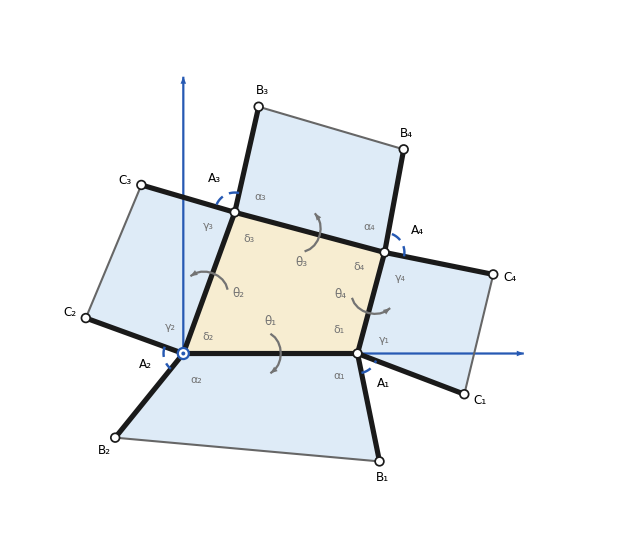
Given hypotheses and definitions:
a vertex A_i of a 3 × 3 net,   i = 1, 2, 3, 4,   where the indices are taken modulo 4, with values in {1, 2, 3, 4}
so, for i = 1:  A_(i−1) = A_4,   θ_(i−1) = θ_4,   (n⃗)_(i−1) = (n⃗)_4 (not (n⃗)_0);   and for i = 4:  A_(i+1) = A_1
the flat angles  α_i, β_i, γ_i, δ_i ∈ (0, π)
the central dihedral angles  θ_(i−1), θ_i ∈ [−π, π) \ {0}  along  A_i A_(i−1), A_i A_(i+1)

Normals:
(n⃗)_0 = (A_2 A_1)^⟶ × (A_2 A_3)^⟶
(n⃗)_1 = (A_2 A_1)^⟶ × (A_2 B_2)^⟶,   (n⃗)_2 = (A_2 C_2)^⟶ × (A_2 A_3)^⟶,   (n⃗)_3 = (A_3 B_3)^⟶ × (A_3 A_4)^⟶,   (n⃗)_4 = (A_1 A_4)^⟶ × (A_1 C_1)^⟶
the same normals through the edges at A_i, up to positive factors, because each face is convex:
odd i: | (n⃗)_0 ∥ (A_i A_(i−1))^⟶ × (A_i A_(i+1))^⟶ | (n⃗)_(i−1) ∥ (A_i A_(i−1))^⟶ × (A_i C_i)^⟶ | (n⃗)_i ∥ (A_i B_i)^⟶ × (A_i A_(i+1))^⟶
even i: | (n⃗)_0 ∥ (A_i A_(i−1))^⟶ × (A_i A_(i+1))^⟶ | (n⃗)_(i−1) ∥ (A_i A_(i−1))^⟶ × (A_i B_i)^⟶ | (n⃗)_i ∥ (A_i C_i)^⟶ × (A_i A_(i+1))^⟶

Dihedral angles:
θ((w⃗)_1, (w⃗)_2, (w⃗)_3) ∶= {∠((w⃗)_1, (w⃗)_2) ∈ (0, π), | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) > 0,
-∠((w⃗)_1, (w⃗)_2) ∈ [-π, 0], | if det((w⃗)_1, (w⃗)_2, (w⃗)_3) ≤ 0.
θ_(i−1) = θ((n⃗)_0, (n⃗)_(i−1), (A_i A_(i−1))^⟶),      θ_i = θ((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶)

Bricard's equation at A_i:
σ_i = (α_i + β_i + γ_i + δ_i)/2 | (ᾱ)_i = σ_i − α_i | (β̄)_i = σ_i − β_i | (γ̄)_i = σ_i − γ_i | (δ̄)_i = σ_i − δ_i
P_i(X, Y) = c_22 X^2 Y^2 + c_20 X^2 + c_02 Y^2 + 2 c_11 X Y + c_00
c_00 = sin σ_i sin (β̄)_i | c_22 = sin (δ̄)_i sin((δ̄)_i − β_i) | c_20 = sin (ᾱ)_i sin((ᾱ)_i − β_i)
c_02 = sin (γ̄)_i sin((γ̄)_i − β_i) | c_11 = −sin α_i sin γ_i | 
odd i: | X = cot(θ_i/2) | Y = cot(θ_(i−1)/2)
even i: | X = cot(θ_(i−1)/2) | Y = cot(θ_i/2)
Z = cot(θ_1/2),   W_2 = cot(θ_2/2),   U = cot(θ_3/2),   W_1 = cot(θ_4/2)
(X, Y) = (Z, W_1), (Z, W_2), (U, W_2), (U, W_1)   for   i = 1, 2, 3, 4

Cartesian coordinates at A_i:
one coordinate frame for each vertex, so that one computation serves all four vertices
origin at A_i,   the first axis along A_i A_(i−1),   the central face in the half-plane of the first two axes where the second coordinate is ≥ 0   (Figure 1 shows i = 2)
(A_i A_(i−1))^⟶ = |A_i A_(i−1)| (1, 0, 0),   (A_i A_(i+1))^⟶ = |A_i A_(i+1)| (cos δ_i, sin δ_i, 0)
-Graphics-
Figure 1.  The central face and the four side faces of a 3 × 3 net, with the coordinates at A_2, projected onto the plane of the first two axes; the corner faces are left out. The blue arrows are the first two axes, and the blue circled dot is the third one, which points towards the viewer. The grey arrows mark the central dihedral angles, and the dashed arcs the angles ∠B_i A_i C_i.

the side faces at each A_i, with the angle at A_i and the free edge, that is, the edge from A_i not on the central face:
 | face on A_i A_(i−1) | face on A_i A_(i+1)
i = 1 | A_4 A_1 C_1 C_4:   γ_1,  A_1 C_1 | A_1 A_2 B_2 B_1:   α_1,  A_1 B_1
i = 2 | A_1 A_2 B_2 B_1:   α_2,  A_2 B_2 | A_2 A_3 C_3 C_2:   γ_2,  A_2 C_2
i = 3 | A_2 A_3 C_3 C_2:   γ_3,  A_3 C_3 | A_3 A_4 B_4 B_3:   α_3,  A_3 B_3
i = 4 | A_3 A_4 B_4 B_3:   α_4,  A_4 B_4 | A_4 A_1 C_1 C_4:   γ_4,  A_4 C_4
so the face with the angle γ_i and the free edge A_i C_i lies on A_i A_(i−1) for odd i, and on A_i A_(i+1) for even i

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, or an inference stated in words beside it.

We want to test the following claims ★ :

Claim 1.
The side faces attached to the central face with the dihedral angles θ_(i−1), θ_i have the free edges
◼ odd i: | (A_i C_i)^⟶ = |A_i C_i| {cos γ_i,sin γ_i cos θ_(i−1),sin γ_i sin θ_(i−1)}
 | (A_i B_i)^⟶ = |A_i B_i| {sin α_i sin δ_i cos θ_i+cos α_i cos δ_i,cos α_i sin δ_i-sin α_i cos δ_i cos θ_i,sin α_i sin θ_i}
◼ even i: | (A_i B_i)^⟶ = |A_i B_i| {cos α_i,sin α_i cos θ_(i−1),sin α_i sin θ_(i−1)}
 | (A_i C_i)^⟶ = |A_i C_i| {sin γ_i sin δ_i cos θ_i+cos γ_i cos δ_i,cos γ_i sin δ_i-sin γ_i cos δ_i cos θ_i,sin γ_i sin θ_i}

Claim 2.
◼ cos β_i − cos ∠B_i A_i C_i = (2 P_i(X, Y))/((1 + X^2)(1 + Y^2))
◼ cos ∠B_i A_i C_i = cos β_i  if and only if  P_i(X, Y) = 0

Claim 3.
If  P_1(Z, W_1) = P_2(Z, W_2) = P_3(U, W_2) = P_4(U, W_1) = 0, then
◼ ∠B_i A_i C_i = β_i  for  i = 1, 2, 3, 4:  the corner faces fit between the side faces attached with the dihedral angles θ_1, …, θ_4.

Claim 1: the free edges of the side facesVerified
Verification: at each vertex, the displayed free edges make the angles of their faces with the edges of the central face, and their faces make the dihedral angles of the given panel with the central face.
Part 1.  Odd i: |  |  | 
(1.1) | (A_i A_(i−1))^⟶ = |A_i A_(i−1)| {1,0,0},   (A_i A_(i+1))^⟶ = |A_i A_(i+1)| {cos δ_i,sin δ_i,0} | • | the coordinates
(1.2) | (A_i C_i)^⟶ = |A_i C_i| {cos γ_i,sin γ_i cos θ_(i−1),sin γ_i sin θ_(i−1)} | • | the free edge of the face on A_i A_(i−1)
(1.3) | (A_i B_i)^⟶ = |A_i B_i| {sin α_i sin δ_i cos θ_i+cos α_i cos δ_i,cos α_i sin δ_i-sin α_i cos δ_i cos θ_i,sin α_i sin θ_i} | • | the free edge of the face on A_i A_(i+1)
(1.4) | |{cos γ_i,sin γ_i cos θ_(i−1),sin γ_i sin θ_(i−1)}| = 1 | ☑ | so |A_i C_i| is the length of the vector in (1.2)
(1.5) | (A_i C_i)^⟶ · (A_i A_(i−1))^⟶ = |A_i C_i| |A_i A_(i−1)| cos γ_i | ☑ | the angle of this face at A_i
(1.6) | |{sin α_i sin δ_i cos θ_i+cos α_i cos δ_i,cos α_i sin δ_i-sin α_i cos δ_i cos θ_i,sin α_i sin θ_i}| = 1 | ☑ | so |A_i B_i| is the length of the vector in (1.3)
(1.7) | (A_i B_i)^⟶ · (A_i A_(i+1))^⟶ = |A_i B_i| |A_i A_(i+1)| cos α_i | ☑ | the angle of this face at A_i
 |  |  | 
(1.8) | (n⃗)_0 ∥ (A_i A_(i−1))^⟶ × (A_i A_(i+1))^⟶ = |A_i A_(i−1)| |A_i A_(i+1)| {0,0,sin δ_i} | ☑ | a positive multiple of (n⃗)_0, which we use for (n⃗)_0; its length is |A_i A_(i−1)| |A_i A_(i+1)| sin δ_i > 0
(1.9) | (n⃗)_(i−1) ∥ (A_i A_(i−1))^⟶ × (A_i C_i)^⟶ = |A_i A_(i−1)| |A_i C_i| sin γ_i {0,-sin θ_(i−1),cos θ_(i−1)} | ☑ | which we use for (n⃗)_(i−1); its length is |A_i A_(i−1)| |A_i C_i| sin γ_i > 0
(1.10) | (n⃗)_i ∥ (A_i B_i)^⟶ × (A_i A_(i+1))^⟶ = |A_i B_i| |A_i A_(i+1)| sin α_i {-sin δ_i sin θ_i,cos δ_i sin θ_i,cos θ_i} | ☑ | which we use for (n⃗)_i; its length is |A_i B_i| |A_i A_(i+1)| sin α_i > 0
 |  |  | 
(1.11) | (n⃗)_0 · (n⃗)_(i−1) = |(n⃗)_0| |(n⃗)_(i−1)| cos θ_(i−1) | ☑ | from (1.8) and (1.9)
(1.12) | det((n⃗)_0, (n⃗)_(i−1), (A_i A_(i−1))^⟶) = |(n⃗)_0| |(n⃗)_(i−1)| |A_i A_(i−1)| sin θ_(i−1) | ☑ | from (1.1), (1.8) and (1.9)
(1.13) | (n⃗)_0 · (n⃗)_i = |(n⃗)_0| |(n⃗)_i| cos θ_i | ☑ | from (1.8) and (1.10)
(1.14) | det((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = |(n⃗)_0| |(n⃗)_i| |A_i A_(i+1)| sin θ_i | ☑ | from (1.1), (1.8) and (1.10), with (A_(i+1)A_i)^⟶ = −(A_i A_(i+1))^⟶
(1.15) | θ((n⃗)_0, (n⃗)_(i−1), (A_i A_(i−1))^⟶) = θ_(i−1),   θ((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = θ_i | • | by (1.11)–(1.14) and the definition: the cosines give the absolute values, because θ_(i−1), θ_i ∈ [−π, π), and the determinants the signs, 0 for −π; positive factors of the normals change neither
 |  |  | 
Part 2.  Even i: |  |  | 
(2.1) | (A_i A_(i−1))^⟶ = |A_i A_(i−1)| {1,0,0},   (A_i A_(i+1))^⟶ = |A_i A_(i+1)| {cos δ_i,sin δ_i,0} | • | the coordinates
(2.2) | (A_i B_i)^⟶ = |A_i B_i| {cos α_i,sin α_i cos θ_(i−1),sin α_i sin θ_(i−1)} | • | the free edge of the face on A_i A_(i−1)
(2.3) | (A_i C_i)^⟶ = |A_i C_i| {sin γ_i sin δ_i cos θ_i+cos γ_i cos δ_i,cos γ_i sin δ_i-sin γ_i cos δ_i cos θ_i,sin γ_i sin θ_i} | • | the free edge of the face on A_i A_(i+1)
(2.4) | |{cos α_i,sin α_i cos θ_(i−1),sin α_i sin θ_(i−1)}| = 1 | ☑ | so |A_i B_i| is the length of the vector in (2.2)
(2.5) | (A_i B_i)^⟶ · (A_i A_(i−1))^⟶ = |A_i B_i| |A_i A_(i−1)| cos α_i | ☑ | the angle of this face at A_i
(2.6) | |{sin γ_i sin δ_i cos θ_i+cos γ_i cos δ_i,cos γ_i sin δ_i-sin γ_i cos δ_i cos θ_i,sin γ_i sin θ_i}| = 1 | ☑ | so |A_i C_i| is the length of the vector in (2.3)
(2.7) | (A_i C_i)^⟶ · (A_i A_(i+1))^⟶ = |A_i C_i| |A_i A_(i+1)| cos γ_i | ☑ | the angle of this face at A_i
 |  |  | 
(2.8) | (n⃗)_0 ∥ (A_i A_(i−1))^⟶ × (A_i A_(i+1))^⟶ = |A_i A_(i−1)| |A_i A_(i+1)| {0,0,sin δ_i} | ☑ | a positive multiple of (n⃗)_0, which we use for (n⃗)_0; its length is |A_i A_(i−1)| |A_i A_(i+1)| sin δ_i > 0
(2.9) | (n⃗)_(i−1) ∥ (A_i A_(i−1))^⟶ × (A_i B_i)^⟶ = |A_i A_(i−1)| |A_i B_i| sin α_i {0,-sin θ_(i−1),cos θ_(i−1)} | ☑ | which we use for (n⃗)_(i−1); its length is |A_i A_(i−1)| |A_i B_i| sin α_i > 0
(2.10) | (n⃗)_i ∥ (A_i C_i)^⟶ × (A_i A_(i+1))^⟶ = |A_i C_i| |A_i A_(i+1)| sin γ_i {-sin δ_i sin θ_i,cos δ_i sin θ_i,cos θ_i} | ☑ | which we use for (n⃗)_i; its length is |A_i C_i| |A_i A_(i+1)| sin γ_i > 0
 |  |  | 
(2.11) | (n⃗)_0 · (n⃗)_(i−1) = |(n⃗)_0| |(n⃗)_(i−1)| cos θ_(i−1) | ☑ | from (2.8) and (2.9)
(2.12) | det((n⃗)_0, (n⃗)_(i−1), (A_i A_(i−1))^⟶) = |(n⃗)_0| |(n⃗)_(i−1)| |A_i A_(i−1)| sin θ_(i−1) | ☑ | from (2.1), (2.8) and (2.9)
(2.13) | (n⃗)_0 · (n⃗)_i = |(n⃗)_0| |(n⃗)_i| cos θ_i | ☑ | from (2.8) and (2.10)
(2.14) | det((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = |(n⃗)_0| |(n⃗)_i| |A_i A_(i+1)| sin θ_i | ☑ | from (2.1), (2.8) and (2.10), with (A_(i+1)A_i)^⟶ = −(A_i A_(i+1))^⟶
(2.15) | θ((n⃗)_0, (n⃗)_(i−1), (A_i A_(i−1))^⟶) = θ_(i−1),   θ((n⃗)_0, (n⃗)_i, (A_(i+1)A_i)^⟶) = θ_i | • | by (2.11)–(2.14) and the definition: the cosines give the absolute values, because θ_(i−1), θ_i ∈ [−π, π), and the determinants the signs, 0 for −π; positive factors of the normals change neither
 |  |  | 
Together, these give Claim 1.

Claim 2: the angle between the free edgesVerified
Verification: the coefficients of P_i(X, Y) through cosines, the cosine of the angle between the free edges of Claim 1 through the half-angle cotangents X and Y, and the comparison of the two, coefficient by coefficient.
(1) | cot(θ/2) = (sin θ)/(1 − cos θ),      sin θ = (2 cot(θ/2))/(1 + cot^2(θ/2)),      cos θ = (cot^2(θ/2) − 1)/(cot^2(θ/2) + 1) | ☑ | for θ ≠ 0 (mod 2π)
 |  |  | 
(2) | 2 c_22 = cos β_i − cos(α_i + γ_i − δ_i) | ☑ | 2 sin x sin y = cos(x − y) − cos(x + y), with 2(δ̄)_i − β_i = α_i + γ_i − δ_i
(3) | 2 c_20 = cos β_i − cos(α_i − γ_i − δ_i) | ☑ | in the same way, with 2(ᾱ)_i − β_i = −α_i + γ_i + δ_i
(4) | 2 c_02 = cos β_i − cos(α_i − γ_i + δ_i) | ☑ | in the same way, with 2(γ̄)_i − β_i = α_i − γ_i + δ_i
(5) | 2 c_00 = cos β_i − cos(α_i + γ_i + δ_i) | ☑ | in the same way, with 2σ_i − β_i = α_i + γ_i + δ_i
(6) | 4 c_11 = −4 sin α_i sin γ_i | ☑ | the definition
 |  |  | 
Part 1.  Odd i:   X = cot(θ_i/2),  Y = cot(θ_(i−1)/2) |  |  | 
(1.1) | cos ∠B_i A_i C_i = ((A_i B_i)^⟶ · (A_i C_i)^⟶)/(|A_i B_i| |A_i C_i|) = cos γ_i (sin α_i sin δ_i cos θ_i+cos α_i cos δ_i)+sin γ_i cos θ_(i−1) (cos α_i sin δ_i-sin α_i cos δ_i cos θ_i)+sin α_i sin γ_i sin θ_i sin θ_(i−1) | ☑ | with the free edges of Claim 1
(1.2) | (1 + X^2)(1 + Y^2) cos ∠B_i A_i C_i = cos(α_i + γ_i − δ_i) X^2 Y^2 + cos(α_i − γ_i − δ_i) X^2 + cos(α_i − γ_i + δ_i) Y^2
+ 4 sin α_i sin γ_i X Y + cos(α_i + γ_i + δ_i) | ☑ | (1.1) with (1), and the sum formulas for the cosine
 |  |  | 
Part 2.  Even i:   X = cot(θ_(i−1)/2),  Y = cot(θ_i/2) |  |  | 
(2.1) | cos ∠B_i A_i C_i = ((A_i B_i)^⟶ · (A_i C_i)^⟶)/(|A_i B_i| |A_i C_i|) = cos α_i (sin γ_i sin δ_i cos θ_i+cos γ_i cos δ_i)+sin α_i cos θ_(i−1) (cos γ_i sin δ_i-sin γ_i cos δ_i cos θ_i)+sin α_i sin γ_i sin θ_i sin θ_(i−1) | ☑ | with the free edges of Claim 1
(2.2) | (1 + X^2)(1 + Y^2) cos ∠B_i A_i C_i = cos(α_i + γ_i − δ_i) X^2 Y^2 + cos(α_i − γ_i − δ_i) X^2 + cos(α_i − γ_i + δ_i) Y^2
+ 4 sin α_i sin γ_i X Y + cos(α_i + γ_i + δ_i) | ☑ | (2.1) with (1), and the sum formulas for the cosine
 |  |  | 
Both parts.  The right-hand sides of (1.2) and (2.2) are the same: |  |  | 
(7) | (cos β_i − cos ∠B_i A_i C_i)(1 + X^2)(1 + Y^2) = (cos β_i − cos(α_i + γ_i − δ_i)) X^2 Y^2 + (cos β_i − cos(α_i − γ_i − δ_i)) X^2
+ (cos β_i − cos(α_i − γ_i + δ_i)) Y^2 − 4 sin α_i sin γ_i X Y + (cos β_i − cos(α_i + γ_i + δ_i)) | ☑ | by (1.2) and (2.2), with (1 + X^2)(1 + Y^2) = X^2 Y^2 + X^2 + Y^2 + 1
(8) | (cos β_i − cos ∠B_i A_i C_i)(1 + X^2)(1 + Y^2) = 2 c_22 X^2 Y^2 + 2 c_20 X^2 + 2 c_02 Y^2 + 4 c_11 X Y + 2 c_00 = 2 P_i(X, Y) | ☑ | by (7) and (2)–(6)
(9) | cos ∠B_i A_i C_i = cos β_i  if and only if  P_i(X, Y) = 0 | • | by (8), because (1 + X^2)(1 + Y^2) > 0
 |  |  | 
Together, these give Claim 2.

Claim 3: the corner faces fitVerified
Verification: Bricard's equations make the angle between the free edges at each vertex that of the corner face.
(1) | P_1(Z, W_1) = P_2(Z, W_2) = P_3(U, W_2) = P_4(U, W_1) = 0 | • | the assumption
(2) | cos ∠B_i A_i C_i = cos β_i,   i = 1, 2, 3, 4 | ☑ | by Claim 2, with (X, Y) = (Z, W_1), (Z, W_2), (U, W_2), (U, W_1)
(3) | ∠B_i A_i C_i = β_i | • | both angles lie in [0, π]
 |  |  | 
(4) | the corner face at A_i fits between the side faces | • | by (3): its edges A_i B_i, A_i C_i lie along the free edges of Claim 1, with the lengths of the side faces
 |  |  | 
Together, these give Claim 3.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[nC,qE,cfE,faceN,cellF,zD,uD,statusChip,smallChip,givenChip,colTest,cols,bullet,ind,vlift,idxB,ptB,pt,edg,evec,nv,wv,tld,gk,thI,bx,cotSqTag,cotTag,mulR,absR,capX,capY,tSym,frac,caseDef,note,firstBase,nrow,prow,hrow,vgap,vgrid,iv,im1,dispRule,trigNames,simpleBoxQ,trigBoxRule,disp,angBAC,capPi,coefD,barG,sqD,aI,bI,gI,dI,tM,tI,X,Y,angSyms,hh,zz,hRule,zeroE,types,aPrevOf,aNextOf,prevEnd,nextEnd,ePrev,eNext,lP,lN,lFP,lFN,ePrevV,eNextV,uPrevOf,uNextOf,fPrevOf,fNextOf,n0,nPrevOf,nNextOf,dirP,dirN,lenPD,lenND,cosForm,sig,c00,c22,c20,c02,c11,pXY,xyRules,figNet,okC1,okC2,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];ind="    ";vlift=0.16;
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
edg[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptB[s1,i1],ptB[s2,i2]}]];
evec[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptB[s1,i1],ptB[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
nv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
(*the normal of the central face*)
nC=nv[0];
wv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["w",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
tld[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
cotSqTag[t_]:=DisplayForm[RowBox[{SuperscriptBox["cot","2"],"(",bx[t],"/","2",")"}]];
cotTag[t_]:=DisplayForm[RowBox[{"cot","(",bx[t],"/","2",")"}]];
mulR[args___]:=Row[Riffle[{args}," "]];absR[e_]:=Row[{"|",e,"|"}];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
caseDef[lhs_,rows_]:=DisplayForm[RowBox[{bx[lhs]," ∶= ",StyleBox["{",SpanMaxSize->Infinity],GridBox[Map[bx,rows,{2}],ColumnAlignments->Left,ColumnSpacings->1.6,RowSpacings->0.9]}]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
(*a numbered line,an unnumbered line (for a name),and a heading line of a block*)
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed index i is an italic string as well*)
iv=Style["i",Italic];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
capX=DisplayForm[StyleBox["X",FontSlant->"Italic"]];capY=DisplayForm[StyleBox["Y",FontSlant->"Italic"]];zD=DisplayForm[StyleBox["Z",FontSlant->"Italic"]];uD=DisplayForm[StyleBox["U",FontSlant->"Italic"]];
im1=Style["i−1",Italic];
(*a side face named by its four vertices,and a cell of the table of the side faces*)
faceN[l_]:=DisplayForm[RowBox[ptB@@@l]];
cellF[f_,ang_,e_]:=Row[{f,":   ",ang,",  ",e}];
(*the angle between the free edges;the polynomial and its coefficients;a barred angle;a square*)
angBAC=DisplayForm[RowBox[{"∠",ptB["B","i"],ptB["A","i"],ptB["C","i"]}]];
capPi[x_,y_]:=DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],idxB["i"]],"(",bx[x],", ",bx[y],")"}]];
coefD[k_]:=DisplayForm[SubscriptBox[StyleBox["c",FontSlant->"Italic"],k]];
barG[g_]:=DisplayForm[SubscriptBox[OverscriptBox[g,"_"],idxB["i"]]];
sqD[x_]:=DisplayForm[SuperscriptBox[bx[x],"2"]];
(*the flat angles at A_i and the central dihedral angles along A_iA_(i-1) and A_iA_(i+1)*)
dispRule={aI->Subscript["α",iv],bI->Subscript["β",iv],gI->Subscript["γ",iv],dI->Subscript["δ",iv],tM->Subscript["θ",im1],tI->Subscript["θ",iv]};
(*a trigonometric identity is decided without Simplify:every angle is written as twice a half angle,each trigonometric function is written through the exponentials of the half angles,and the resulting rational function,or each component of a vector,must be 0*)
angSyms={aI,bI,gI,dI,tM,tI};
hRule=Thread[angSyms->Table[2 hh[k],{k,Length[angSyms]}]];
zeroE[e_]:=Module[{f=e/. hRule,hv,mon},hv=Union[Cases[f,hh[_],{0,Infinity}]];mon[x_]:=Product[zz[h]^Coefficient[x,h],{h,hv}];
f=f/. {Sin[x_]:>(mon[x]-1/mon[x])/(2 I),Cos[x_]:>(mon[x]+1/mon[x])/2,Tan[x_]:>(mon[x]-1/mon[x])/(I (mon[x]+1/mon[x])),Cot[x_]:>I (mon[x]+1/mon[x])/(mon[x]-1/mon[x]),Sec[x_]:>2/(mon[x]+1/mon[x]),Csc[x_]:>2 I/(mon[x]-1/mon[x])};
AllTrue[Flatten[{Together[f]}],#===0&]];

(*the coordinates at A_i:the origin at A_i,the unit vectors along A_iA_(i-1) and A_iA_(i+1),and,for odd and even i,the angle at A_i of the face on each of these edges and the end of its free edge.The four edges at A_i have arbitrary lengths:lP= |A_iA_(i-1)|,lN= |A_iA_(i+1)|,lFP and lFN those of the free edges of the faces on A_iA_(i-1) and on A_iA_(i+1)*)
types={"odd","even"};
aPrevOf["odd"]=gI;aNextOf["odd"]=aI;prevEnd["odd"]="C";nextEnd["odd"]="B";
aPrevOf["even"]=aI;aNextOf["even"]=gI;prevEnd["even"]="B";nextEnd["even"]="C";
ePrev={1,0,0};eNext={Cos[dI],Sin[dI],0};ePrevV=lP ePrev;eNextV=lN eNext;
uPrevOf[v_]:={Cos[aPrevOf[v]],Sin[aPrevOf[v]] Cos[tM],Sin[aPrevOf[v]] Sin[tM]};
uNextOf[v_]:=Cos[aNextOf[v]] eNext+Sin[aNextOf[v]] {Sin[dI] Cos[tI],-Cos[dI] Cos[tI],Sin[tI]};
fPrevOf[v_]:=lFP uPrevOf[v];fNextOf[v_]:=lFN uNextOf[v];
n0=Cross[ePrevV,eNextV];
nPrevOf[v_]:=Cross[ePrevV,fPrevOf[v]];nNextOf[v_]:=Cross[fNextOf[v],eNextV];
lenPD=absR[edg["A","i","A","i−1"]];lenND=absR[edg["A","i","A","i+1"]];
dirP={0,-Sin[tM],Cos[tM]};dirN={-Sin[dI] Sin[tI],Cos[dI] Sin[tI],Cos[tI]};
cosForm[v_]:=Module[{p=aPrevOf[v],q=aNextOf[v]},Cos[p] (Cos[q] Cos[dI]+Sin[q] Sin[dI] Cos[tI])+Sin[p] Cos[tM] (Cos[q] Sin[dI]-Sin[q] Cos[dI] Cos[tI])+Sin[p] Sin[q] Sin[tM] Sin[tI]];
(*Bricard's polynomial at A_i;X is the cotangent of half the dihedral angle along the edge of the face with the angle alpha,Y along the edge of the face with the angle gamma*)
sig=(aI+bI+gI+dI)/2;
c00=Sin[sig] Sin[sig-bI];c22=Sin[sig-dI] Sin[sig-dI-bI];c20=Sin[sig-aI] Sin[sig-aI-bI];c02=Sin[sig-gI] Sin[sig-gI-bI];c11=-Sin[aI] Sin[gI];
pXY=c22 X^2 Y^2+c20 X^2+c02 Y^2+2 c11 X Y+c00;
(*(1+X^2)(1+Y^2) times the cosine of the angle between the free edges,and cos(beta)(1+X^2)(1+Y^2) minus it,as polynomials in X and Y*)
qE=Cos[aI+gI-dI] X^2 Y^2+Cos[aI-gI-dI] X^2+Cos[aI-gI+dI] Y^2+4 Sin[aI] Sin[gI] X Y+Cos[aI+gI+dI];
cfE=(Cos[bI]-Cos[aI+gI-dI]) X^2 Y^2+(Cos[bI]-Cos[aI-gI-dI]) X^2+(Cos[bI]-Cos[aI-gI+dI]) Y^2-4 Sin[aI] Sin[gI] X Y+(Cos[bI]-Cos[aI+gI+dI]);
xyRules["odd"]={Cos[tI]->(X^2-1)/(X^2+1),Sin[tI]->2 X/(X^2+1),Cos[tM]->(Y^2-1)/(Y^2+1),Sin[tM]->2 Y/(Y^2+1)};
xyRules["even"]={Cos[tM]->(X^2-1)/(X^2+1),Sin[tM]->2 X/(X^2+1),Cos[tI]->(Y^2-1)/(Y^2+1),Sin[tI]->2 Y/(Y^2+1)};
resultsAll={};
(*the figure:the central face and the four side faces of one 3 x 3 net,with the coordinates at A_2,projected onto the plane of the central face;the corner faces are left out,and the dashed arcs mark the angles between the free edges.The numbers of the drawing are chosen by hand and enter no verification*)
figNet=Module[{dg=π/180.,l1=4.4,l2=3.8,l4,mL={3.2,3.0,3.1,3.0},vL={3.4,3.2,3.0,3.3},d1,d2,d3,d4,t1,t2,t3,t4,al,ga,pA,pB,pC,vA,vB,vC,cen,nextA={2,1,4,3},prevA={4,3,2,1},grey=GrayLevel[0.45],blue=RGBColor[0.15,0.35,0.7],bis,gapArc,thArc,faces,thin,thick,dots,axes,zmark,arcs,gaps,angLabs,vtxLabs,xEnd=8.6,yEnd=7.0},{d1,d2,d3,d4}={105,70,95,90} dg;{t1,t2,t3,t4}={150,145,152,148} dg;
al={100,125,92,86} dg;ga={95,90,87,93} dg;
l4=(l2 Sin[d3]-l1 Sin[d2+d3])/Sin[d4];
pA[2]={0,0,0};pA[1]={l1,0,0};pA[3]=l2 {Cos[d2],Sin[d2],0};pA[4]=pA[1]+l4 {-Cos[d1],Sin[d1],0};
pB[1]=pA[1]+mL[[1]] {-Cos[al[[1]]],Sin[al[[1]]] Cos[t1],Sin[al[[1]]] Sin[t1]};
pB[2]=pA[2]+mL[[2]] {Cos[al[[2]]],Sin[al[[2]]] Cos[t1],Sin[al[[2]]] Sin[t1]};
pB[3]=pA[3]+mL[[3]] {-(Cos[al[[3]]] Cos[d2+d3]+Sin[al[[3]]] Cos[t3] Sin[d2+d3]),-(Cos[al[[3]]] Sin[d2+d3]-Sin[al[[3]]] Cos[t3] Cos[d2+d3]),Sin[al[[3]]] Sin[t3]};
pB[4]=pA[4]+mL[[4]] {Cos[al[[4]]] Cos[d2+d3]-Sin[al[[4]]] Cos[t3] Sin[d2+d3],Cos[al[[4]]] Sin[d2+d3]+Sin[al[[4]]] Cos[t3] Cos[d2+d3],Sin[al[[4]]] Sin[t3]};
pC[1]=pA[1]+vL[[1]] {-(Cos[ga[[1]]] Cos[d1]+Sin[ga[[1]]] Cos[t4] Sin[d1]),Cos[ga[[1]]] Sin[d1]-Sin[ga[[1]]] Cos[t4] Cos[d1],Sin[ga[[1]]] Sin[t4]};
pC[2]=pA[2]+vL[[2]] {Cos[ga[[2]]] Cos[d2]+Sin[ga[[2]]] Cos[t2] Sin[d2],Cos[ga[[2]]] Sin[d2]-Sin[ga[[2]]] Cos[t2] Cos[d2],Sin[ga[[2]]] Sin[t2]};
pC[3]=pA[3]+vL[[3]] {-(Cos[ga[[3]]] Cos[d2]-Sin[ga[[3]]] Cos[t2] Sin[d2]),-(Cos[ga[[3]]] Sin[d2]+Sin[ga[[3]]] Cos[t2] Cos[d2]),Sin[ga[[3]]] Sin[t2]};
pC[4]=pA[4]+vL[[4]] {Cos[ga[[4]]] Cos[d1]-Sin[ga[[4]]] Cos[t4] Sin[d1],-(Cos[ga[[4]]] Sin[d1]+Sin[ga[[4]]] Cos[t4] Cos[d1]),Sin[ga[[4]]] Sin[t4]};
vA=Table[Most[pA[i]],{i,4}];vB=Table[Most[pB[i]],{i,4}];vC=Table[Most[pC[i]],{i,4}];
cen=Mean[vA];
bis[o_,p_,q_]:=Normalize[Normalize[p-o]+Normalize[q-o]];
gapArc[i_]:=Module[{o=vA[[i]],ab,ac,am,s,e},ab=ArcTan@@(vB[[i]]-o);ac=ArcTan@@(vC[[i]]-o);am=ArcTan@@(cen-o);If[Mod[am-ab,2 π]<Mod[ac-ab,2 π],{s,e}={ac,ab},{s,e}={ab,ac}];If[e<s,e+=2 π];{{blue,Dashing[{0.012,0.008}],Thickness[0.0028],Circle[o,0.5,{s,e}]},Text[Style[pt["A",i],12],o+1.0 {Cos[(s+e)/2],Sin[(s+e)/2]}]}];
thArc[a_,b_,into_,lbl_]:=Module[{mp=(a+b)/2,ed=Normalize[b-a],nn,dd},nn={-ed[[2]],ed[[1]]};dd=If[nn.(into-mp)>0,nn,-nn];{{grey,Thickness[0.0026],Arrowheads[0.02],Arrow[BezierCurve[{mp-0.5 dd,mp-0.3 dd+0.35 ed,mp+0.3 dd+0.35 ed,mp+0.5 dd}]]},Text[Style[lbl,12,grey],mp-0.8 dd]}];
faces={EdgeForm[None],FaceForm[RGBColor[0.97,0.93,0.82]],Polygon[vA],FaceForm[RGBColor[0.87,0.92,0.97]],Polygon[{vA[[1]],vA[[2]],vB[[2]],vB[[1]]}],Polygon[{vA[[2]],vA[[3]],vC[[3]],vC[[2]]}],Polygon[{vA[[3]],vA[[4]],vB[[4]],vB[[3]]}],Polygon[{vA[[4]],vA[[1]],vC[[1]],vC[[4]]}]};
thin={Thickness[0.0024],GrayLevel[0.4],Line[{vB[[2]],vB[[1]]}],Line[{vC[[3]],vC[[2]]}],Line[{vB[[4]],vB[[3]]}],Line[{vC[[1]],vC[[4]]}]};
thick={Thickness[0.006],GrayLevel[0.1],Line[Append[vA,vA[[1]]]],Sequence@@Table[Line[{vA[[i]],vB[[i]]}],{i,4}],Sequence@@Table[Line[{vA[[i]],vC[[i]]}],{i,4}]};
dots={White,EdgeForm[{GrayLevel[0.1],Thickness[0.002]}],Sequence@@Table[Disk[pp,0.11],{pp,Join[{vA[[1]],vA[[3]],vA[[4]]},vB,vC]}]};
axes={blue,Thickness[0.0026],Arrowheads[0.018],Arrow[{vA[[2]],{xEnd,0}}],Arrow[{vA[[2]],{0,yEnd}}]};
zmark={White,EdgeForm[{blue,Thickness[0.0026]}],Disk[vA[[2]],0.14],EdgeForm[None],blue,Disk[vA[[2]],0.05]};
arcs={thArc[vA[[2]],vA[[1]],Mean[{vB[[1]],vB[[2]]}],thI[1]],thArc[vA[[2]],vA[[3]],Mean[{vC[[2]],vC[[3]]}],thI[2]],thArc[vA[[3]],vA[[4]],Mean[{vB[[3]],vB[[4]]}],thI[3]],thArc[vA[[4]],vA[[1]],Mean[{vC[[4]],vC[[1]]}],thI[4]]};
gaps=Table[gapArc[i],{i,4}];
angLabs=Flatten[Table[{Text[Style[gk["δ",i],11,grey],vA[[i]]+0.75 bis[vA[[i]],vA[[nextA[[i]]]],vA[[prevA[[i]]]]]],Text[Style[gk["α",i],11,grey],vA[[i]]+0.75 bis[vA[[i]],vA[[nextA[[i]]]],vB[[i]]]],Text[Style[gk["γ",i],11,grey],vA[[i]]+0.75 bis[vA[[i]],vA[[prevA[[i]]]],vC[[i]]]]},{i,4}]];
vtxLabs=Join[Table[Text[Style[pt["B",i],12],vB[[i]]+0.42 Normalize[vB[[i]]-vA[[i]]]],{i,4}],Table[Text[Style[pt["C",i],12],vC[[i]]+0.42 Normalize[vC[[i]]-vA[[i]]]],{i,4}]];
Graphics[{faces,axes,thin,thick,arcs,gaps,angLabs,dots,zmark,vtxLabs},ImageSize->620,PlotRange->{{-3.2,9.6},{-3.4,7.7}},PlotRangePadding->None,Background->None,BaseStyle->{FontFamily->"Times"}]];

(* ============================================================*)
(*PART 2:GIVEN PANEL*)
(* ============================================================*)
Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style[Column[{Row[{"a vertex ",pt["A","i"]," of a 3 × 3 net,   i = 1, 2, 3, 4,   where the indices are taken modulo 4, with values in {1, 2, 3, 4}"}],note[Row[{"so, for i = 1:  ",pt["A","i−1"]," = ",pt["A",4],",   ",thI["i−1"]," = ",thI[4],",   ",nv["i−1"]," = ",nv[4]," (not ",nC,")",";   and for i = 4:  ",pt["A","i+1"]," = ",pt["A",1]}]],Row[{"the flat angles  ",gk["α","i"],", ",gk["β","i"],", ",gk["γ","i"],", ",gk["δ","i"]," ∈ (0, π)"}],Row[{"the central dihedral angles  ",thI["i−1"],", ",thI["i"]," ∈ [−π, π) \\ {0}  along  ",edg["A","i","A","i−1"],", ",edg["A","i","A","i+1"]}]},Spacings->0.7],13],Spacer[{0,8}],Style["Normals:",Bold,14],Style[Column[{Row[{nC," = ",evec["A",2,"A",1]," × ",evec["A",2,"A",3]}],Row[{nv[1]," = ",evec["A",2,"A",1]," × ",evec["A",2,"B",2],",   ",nv[2]," = ",evec["A",2,"C",2]," × ",evec["A",2,"A",3],",   ",nv[3]," = ",evec["A",3,"B",3]," × ",evec["A",3,"A",4],",   ",nv[4]," = ",evec["A",1,"A",4]," × ",evec["A",1,"C",1]}]},Spacings->0.8],13],Style[Row[{"the same normals through the edges at ",pt["A","i"],", up to positive factors, because each face is convex:"}],13],Style[Grid[{{"odd i:",Row[{nC," ∥ ",evec["A","i","A","i−1"]," × ",evec["A","i","A","i+1"]}],Row[{nv["i−1"]," ∥ ",evec["A","i","A","i−1"]," × ",evec["A","i","C","i"]}],Row[{nv["i"]," ∥ ",evec["A","i","B","i"]," × ",evec["A","i","A","i+1"]}]},{"even i:",Row[{nC," ∥ ",evec["A","i","A","i−1"]," × ",evec["A","i","A","i+1"]}],Row[{nv["i−1"]," ∥ ",evec["A","i","A","i−1"]," × ",evec["A","i","B","i"]}],Row[{nv["i"]," ∥ ",evec["A","i","C","i"]," × ",evec["A","i","A","i+1"]}]}},Alignment->Left,Spacings->{2.4,0.8}],13],Spacer[{0,8}],Style["Dihedral angles:",Bold,14],Style[caseDef[Row[{"θ(",wv[1],", ",wv[2],", ",wv[3],")"}],{{Row[{"∠(",wv[1],", ",wv[2],") ∈ (0, π),"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") > 0,"}]},{Row[{"-∠(",wv[1],", ",wv[2],") ∈ [-π, 0],"}],Row[{"if det(",wv[1],", ",wv[2],", ",wv[3],") ≤ 0."}]}}],13],Style[Row[{thI["i−1"]," = θ(",nC,", ",nv["i−1"],", ",evec["A","i","A","i−1"],"),      ",thI["i"]," = θ(",nC,", ",nv["i"],", ",evec["A","i+1","A","i"],")"}],13],Spacer[{0,8}],Style[Row[{"Bricard's equation at ",pt["A","i"],":"}],Bold,14],Style[Grid[{{Row[{gk["σ","i"]," = (",gk["α","i"]," + ",gk["β","i"]," + ",gk["γ","i"]," + ",gk["δ","i"],")/2"}],Row[{barG["α"]," = ",gk["σ","i"]," − ",gk["α","i"]}],Row[{barG["β"]," = ",gk["σ","i"]," − ",gk["β","i"]}],Row[{barG["γ"]," = ",gk["σ","i"]," − ",gk["γ","i"]}],Row[{barG["δ"]," = ",gk["σ","i"]," − ",gk["δ","i"]}]}},Alignment->Left,Spacings->{2.4,0}],13],Style[Row[{capPi[capX,capY]," = ",mulR[coefD["22"],sqD[capX],sqD[capY]]," + ",mulR[coefD["20"],sqD[capX]]," + ",mulR[coefD["02"],sqD[capY]]," + 2 ",mulR[coefD["11"],capX,capY]," + ",coefD["00"]}],13],Style[Grid[{{Row[{coefD["00"]," = sin ",gk["σ","i"]," sin ",barG["β"]}],Row[{coefD["22"]," = sin ",barG["δ"]," sin(",barG["δ"]," − ",gk["β","i"],")"}],Row[{coefD["20"]," = sin ",barG["α"]," sin(",barG["α"]," − ",gk["β","i"],")"}]},{Row[{coefD["02"]," = sin ",barG["γ"]," sin(",barG["γ"]," − ",gk["β","i"],")"}],Row[{coefD["11"]," = −sin ",gk["α","i"]," sin ",gk["γ","i"]}],""}},Alignment->Left,Spacings->{2.4,0.8}],13],Style[Grid[{{"odd i:",Row[{capX," = ",cotTag[thI["i"]]}],Row[{capY," = ",cotTag[thI["i−1"]]}]},{"even i:",Row[{capX," = ",cotTag[thI["i−1"]]}],Row[{capY," = ",cotTag[thI["i"]]}]}},Alignment->Left,Spacings->{2.4,0.6}],13],Style[Row[{zD," = ",cotTag[thI[1]],",   ",pt["W",2]," = ",cotTag[thI[2]],",   ",uD," = ",cotTag[thI[3]],",   ",pt["W",1]," = ",cotTag[thI[4]]}],13],Style[Row[{"(",capX,", ",capY,") = (",zD,", ",pt["W",1],"), (",zD,", ",pt["W",2],"), (",uD,", ",pt["W",2],"), (",uD,", ",pt["W",1],")   for   i = 1, 2, 3, 4"}],13],Spacer[{0,8}],Style[Row[{"Cartesian coordinates at ",pt["A","i"],":"}],Bold,14],note["one coordinate frame for each vertex, so that one computation serves all four vertices"],Style[Row[{"origin at ",pt["A","i"],",   the first axis along ",edg["A","i","A","i−1"],",   the central face in the half-plane of the first two axes where the second coordinate is ≥ 0   (Figure 1 shows i = 2)"}],13],Style[Row[{evec["A","i","A","i−1"]," = ",lenPD," (1, 0, 0),   ",evec["A","i","A","i+1"]," = ",lenND," (cos ",gk["δ","i"],", sin ",gk["δ","i"],", 0)"}],13],Column[{figNet,Style[Row[{"Figure 1.  The central face and the four side faces of a 3 × 3 net, with the coordinates at ",pt["A",2],", projected onto the plane of the first two axes; the corner faces are left out. The blue arrows are the first two axes, and the blue circled dot is the third one, which points towards the viewer. The grey arrows mark the central dihedral angles, and the dashed arcs the angles ",angBAC,"."}],12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,6}],Style[Row[{"the side faces at each ",pt["A","i"],", with the angle at ",pt["A","i"]," and the free edge, that is, the edge from ",pt["A","i"]," not on the central face:"}],13],Style[Grid[{{"",Row[{"face on ",edg["A","i","A","i−1"]}],Row[{"face on ",edg["A","i","A","i+1"]}]},{"i = 1",cellF[faceN[{{"A",4},{"A",1},{"C",1},{"C",4}}],gk["γ",1],edg["A",1,"C",1]],cellF[faceN[{{"A",1},{"A",2},{"B",2},{"B",1}}],gk["α",1],edg["A",1,"B",1]]},{"i = 2",cellF[faceN[{{"A",1},{"A",2},{"B",2},{"B",1}}],gk["α",2],edg["A",2,"B",2]],cellF[faceN[{{"A",2},{"A",3},{"C",3},{"C",2}}],gk["γ",2],edg["A",2,"C",2]]},{"i = 3",cellF[faceN[{{"A",2},{"A",3},{"C",3},{"C",2}}],gk["γ",3],edg["A",3,"C",3]],cellF[faceN[{{"A",3},{"A",4},{"B",4},{"B",3}}],gk["α",3],edg["A",3,"B",3]]},{"i = 4",cellF[faceN[{{"A",3},{"A",4},{"B",4},{"B",3}}],gk["α",4],edg["A",4,"B",4]],cellF[faceN[{{"A",4},{"A",1},{"C",1},{"C",4}}],gk["γ",4],edg["A",4,"C",4]]}},Alignment->Left,Spacings->{3,0.6},Dividers->{None,{2->GrayLevel[0.75]}}],13],note[Row[{"so the face with the angle ",gk["γ","i"]," and the free edge ",edg["A","i","C","i"]," lies on ",edg["A","i","A","i−1"]," for odd i, and on ",edg["A","i","A","i+1"]," for even i"}]],Spacer[{0,8}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim 1.",Bold,13,colTest],Style[Row[{"The side faces attached to the central face with the dihedral angles ",thI["i−1"],", ",thI["i"]," have the free edges"}],Bold,13,colTest],Style[Grid[{{Row[{bullet,"odd i:"}],Row[{evec["A","i","C","i"]," = ",absR[edg["A","i","C","i"]]," ",disp[uPrevOf["odd"]]}]},{"",Row[{evec["A","i","B","i"]," = ",absR[edg["A","i","B","i"]]," ",disp[uNextOf["odd"]]}]},{Row[{bullet,"even i:"}],Row[{evec["A","i","B","i"]," = ",absR[edg["A","i","B","i"]]," ",disp[uPrevOf["even"]]}]},{"",Row[{evec["A","i","C","i"]," = ",absR[edg["A","i","C","i"]]," ",disp[uNextOf["even"]]}]}},Alignment->{Left,Baseline},Spacings->{1.5,0.7}],Bold,13,colTest],Spacer[{0,12}],Style["Claim 2.",Bold,13,colTest],Row[{bullet,Style[Row[{"cos ",gk["β","i"]," − cos ",angBAC," = ",frac[Row[{"2 ",capPi[capX,capY]}],Row[{"(1 + ",sqD[capX],")(1 + ",sqD[capY],")"}]]}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"cos ",angBAC," = cos ",gk["β","i"],"  if and only if  ",capPi[capX,capY]," = 0"}],Bold,13,colTest]}],Spacer[{0,12}],Style["Claim 3.",Bold,13,colTest],Style[Row[{"If  ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"1"],"(",StyleBox["Z",FontSlant->"Italic"],", ",ptB["W",1],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"2"],"(",StyleBox["Z",FontSlant->"Italic"],", ",ptB["W",2],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"3"],"(",StyleBox["U",FontSlant->"Italic"],", ",ptB["W",2],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"4"],"(",StyleBox["U",FontSlant->"Italic"],", ",ptB["W",1],")"}]]," = 0, then"}],Bold,13,colTest],Row[{bullet,Style[Row[{angBAC," = ",gk["β","i"],"  for  i = 1, 2, 3, 4:  the corner faces fit between the side faces attached with the dihedral angles ",thI[1],", …, ",thI[4],"."}],Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=cols[[1]],oks={},chk,rows},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
rows=Flatten[Table[Module[{v=types[[p]],aP,aN,uP,uN,fP,fN,nP,nN,hP,hN,lhP,lhN,eP=evec["A","i","A","i−1"],eN=evec["A","i","A","i+1"],eNr=evec["A","i+1","A","i"],nM=nv["i−1"],nI=nv["i"],n0d=nC,lb,rf},aP=aPrevOf[v];aN=aNextOf[v];uP=uPrevOf[v];uN=uNextOf[v];fP=fPrevOf[v];fN=fNextOf[v];nP=nPrevOf[v];nN=nNextOf[v];
hP=evec["A","i",prevEnd[v],"i"];hN=evec["A","i",nextEnd[v],"i"];lhP=absR[edg["A","i",prevEnd[v],"i"]];lhN=absR[edg["A","i",nextEnd[v],"i"]];
lb[k_]:=ToString[p]<>"."<>ToString[k];rf[k_]:="("<>lb[k]<>")";
{hrow[Row[{Style["Part "<>ToString[p]<>".",Bold],"  ",If[v==="odd","Odd i:","Even i:"]}]],nrow[lb[1],Row[{eP," = ",lenPD," ",disp[ePrev],",   ",eN," = ",lenND," ",disp[eNext]}],givenChip,"the coordinates"],nrow[lb[2],Row[{hP," = ",lhP," ",disp[uP]}],givenChip,Row[{"the free edge of the face on ",edg["A","i","A","i−1"]}]],nrow[lb[3],Row[{hN," = ",lhN," ",disp[uN]}],givenChip,Row[{"the free edge of the face on ",edg["A","i","A","i+1"]}]],nrow[lb[4],Row[{absR[disp[uP]]," = 1"}],smallChip[chk[uP.uP-1]],Row[{"so ",lhP," is the length of the vector in ",rf[2]}]],nrow[lb[5],Row[{hP," · ",eP," = ",mulR[lhP,lenPD]," cos ",disp[aP]}],smallChip[chk[fP.ePrevV-lFP lP Cos[aP]]],Row[{"the angle of this face at ",pt["A","i"]}]],nrow[lb[6],Row[{absR[disp[uN]]," = 1"}],smallChip[chk[uN.uN-1]],Row[{"so ",lhN," is the length of the vector in ",rf[3]}]],nrow[lb[7],Row[{hN," · ",eN," = ",mulR[lhN,lenND]," cos ",disp[aN]}],smallChip[chk[fN.eNextV-lFN lN Cos[aN]]],Row[{"the angle of this face at ",pt["A","i"]}]],vgap,nrow[lb[8],Row[{n0d," ∥ ",eP," × ",eN," = ",mulR[lenPD,lenND]," ",disp[{0,0,Sin[dI]}]}],smallChip[chk[n0-lP lN {0,0,Sin[dI]}]],Row[{"a positive multiple of ",n0d,", which we use for ",n0d,"; its length is ",mulR[lenPD,lenND]," sin ",disp[dI]," > 0"}]],nrow[lb[9],Row[{nM," ∥ ",eP," × ",hP," = ",mulR[lenPD,lhP]," ",disp[Sin[aP]]," ",disp[dirP]}],smallChip[chk[nP-lP lFP Sin[aP] dirP]],Row[{"which we use for ",nM,"; its length is ",mulR[lenPD,lhP]," sin ",disp[aP]," > 0"}]],nrow[lb[10],Row[{nI," ∥ ",hN," × ",eN," = ",mulR[lhN,lenND]," ",disp[Sin[aN]]," ",disp[dirN]}],smallChip[chk[nN-lFN lN Sin[aN] dirN]],Row[{"which we use for ",nI,"; its length is ",mulR[lhN,lenND]," sin ",disp[aN]," > 0"}]],vgap,nrow[lb[11],Row[{n0d," · ",nM," = ",mulR[absR[n0d],absR[nM]]," cos ",thI["i−1"]}],smallChip[chk[n0.nP-(lP lN Sin[dI]) (lP lFP Sin[aP]) Cos[tM]]],Row[{"from ",rf[8]," and ",rf[9]}]],nrow[lb[12],Row[{"det(",n0d,", ",nM,", ",eP,") = ",mulR[absR[n0d],absR[nM],lenPD]," sin ",thI["i−1"]}],smallChip[chk[Det[{n0,nP,ePrevV}]-(lP lN Sin[dI]) (lP lFP Sin[aP]) lP Sin[tM]]],Row[{"from ",rf[1],", ",rf[8]," and ",rf[9]}]],nrow[lb[13],Row[{n0d," · ",nI," = ",mulR[absR[n0d],absR[nI]]," cos ",thI["i"]}],smallChip[chk[n0.nN-(lP lN Sin[dI]) (lFN lN Sin[aN]) Cos[tI]]],Row[{"from ",rf[8]," and ",rf[10]}]],nrow[lb[14],Row[{"det(",n0d,", ",nI,", ",eNr,") = ",mulR[absR[n0d],absR[nI],lenND]," sin ",thI["i"]}],smallChip[chk[Det[{n0,nN,-eNextV}]-(lP lN Sin[dI]) (lFN lN Sin[aN]) lN Sin[tI]]],Row[{"from ",rf[1],", ",rf[8]," and ",rf[10],", with ",eNr," = −",eN}]],nrow[lb[15],Row[{"θ(",n0d,", ",nM,", ",evec["A","i","A","i−1"],") = ",thI["i−1"],",   θ(",n0d,", ",nI,", ",evec["A","i+1","A","i"],") = ",thI["i"]}],givenChip,Row[{"by ",rf[11],"–",rf[14]," and the definition: the cosines give the absolute values, because ",thI["i−1"],", ",thI["i"]," ∈ [−π, π), and the determinants the signs, 0 for −π; positive factors of the normals change neither"}]],vgap}],{p,2}],1];
okC1=And@@oks;AppendTo[resultsAll,okC1];
Print[Panel[Column[{Row[{Style["Claim 1: the free edges of the side faces",Bold,15,col],Spacer[20],statusChip[okC1]}],Style["Verification: at each vertex, the displayed free edges make the angles of their faces with the edges of the central face, and their faces make the dihedral angles of the given panel with the central face.",Bold,13],vgrid[rows],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=cols[[2]],oks={},chk,w1,gT=DisplayForm["θ"],rows,cosC,cb,sA,sG,xy2,qD,cfD,lhs},chk[e_]:=Module[{r=zeroE[e]},AppendTo[oks,r];r];
cosC[s1_,s2_]:=Row[{"cos(",gk["α","i"]," ",s1," ",gk["γ","i"]," ",s2," ",gk["δ","i"],")"}];
cb=Row[{"cos ",gk["β","i"]}];sA=Row[{"sin ",gk["α","i"]}];sG=Row[{"sin ",gk["γ","i"]}];
xy2=mulR[sqD[capX],sqD[capY]];
qD=Column[{Row[{cosC["+","−"]," ",xy2," + ",cosC["−","−"]," ",sqD[capX]," + ",cosC["−","+"]," ",sqD[capY]}],Row[{"+ 4 ",sA," ",sG," ",mulR[capX,capY]," + ",cosC["+","+"]}]},Alignment->Left,BaselinePosition->{1,1}];
cfD=Column[{Row[{"(",cb," − ",cosC["+","−"],") ",xy2," + (",cb," − ",cosC["−","−"],") ",sqD[capX]}],Row[{"+ (",cb," − ",cosC["−","+"],") ",sqD[capY]," − 4 ",sA," ",sG," ",mulR[capX,capY]," + (",cb," − ",cosC["+","+"],")"}]},Alignment->Left,BaselinePosition->{1,1}];
lhs=Row[{"(",cb," − cos ",angBAC,")(1 + ",sqD[capX],")(1 + ",sqD[capY],")"}];
w1=And@@(chk/@{Cot[tI/2] (1-Cos[tI])-Sin[tI],Sin[tI] (1+Cot[tI/2]^2)-2 Cot[tI/2],Cos[tI] (1+Cot[tI/2]^2)-(Cot[tI/2]^2-1)});
rows=Join[{nrow[1,Row[{cotTag[gT]," = ",frac[Row[{"sin ",gT}],Row[{"1 − cos ",gT}]],",      sin ",gT," = ",frac[Row[{"2 ",cotTag[gT]}],Row[{"1 + ",cotSqTag[gT]}]],",      cos ",gT," = ",frac[Row[{cotSqTag[gT]," − 1"}],Row[{cotSqTag[gT]," + 1"}]]}],smallChip[w1],Row[{"for ",gT," ≠ 0 (mod 2π)"}]],vgap,nrow[2,Row[{"2 ",coefD["22"]," = ",cb," − ",cosC["+","−"]}],smallChip[chk[2 c22-(Cos[bI]-Cos[aI+gI-dI])]],Row[{"2 sin x sin y = cos(x − y) − cos(x + y), with 2",barG["δ"]," − ",gk["β","i"]," = ",gk["α","i"]," + ",gk["γ","i"]," − ",gk["δ","i"]}]],nrow[3,Row[{"2 ",coefD["20"]," = ",cb," − ",cosC["−","−"]}],smallChip[chk[2 c20-(Cos[bI]-Cos[aI-gI-dI])]],Row[{"in the same way, with 2",barG["α"]," − ",gk["β","i"]," = −",gk["α","i"]," + ",gk["γ","i"]," + ",gk["δ","i"]}]],nrow[4,Row[{"2 ",coefD["02"]," = ",cb," − ",cosC["−","+"]}],smallChip[chk[2 c02-(Cos[bI]-Cos[aI-gI+dI])]],Row[{"in the same way, with 2",barG["γ"]," − ",gk["β","i"]," = ",gk["α","i"]," − ",gk["γ","i"]," + ",gk["δ","i"]}]],nrow[5,Row[{"2 ",coefD["00"]," = ",cb," − ",cosC["+","+"]}],smallChip[chk[2 c00-(Cos[bI]-Cos[aI+gI+dI])]],Row[{"in the same way, with 2",gk["σ","i"]," − ",gk["β","i"]," = ",gk["α","i"]," + ",gk["γ","i"]," + ",gk["δ","i"]}]],nrow[6,Row[{"4 ",coefD["11"]," = −4 ",sA," ",sG}],smallChip[chk[4 c11+4 Sin[aI] Sin[gI]]],"the definition"],vgap},Flatten[Table[Module[{v=types[[p]],fP,fN,lb,rf},fP=fPrevOf[v];fN=fNextOf[v];
lb[k_]:=ToString[p]<>"."<>ToString[k];rf[k_]:="("<>lb[k]<>")";
{hrow[Row[{Style["Part "<>ToString[p]<>".",Bold],"  ",If[v==="odd",Row[{"Odd i:   ",capX," = ",cotTag[thI["i"]],",  ",capY," = ",cotTag[thI["i−1"]]}],Row[{"Even i:   ",capX," = ",cotTag[thI["i−1"]],",  ",capY," = ",cotTag[thI["i"]]}]]}]],nrow[lb[1],Row[{"cos ",angBAC," = ",frac[Row[{evec["A","i","B","i"]," · ",evec["A","i","C","i"]}],mulR[absR[edg["A","i","B","i"]],absR[edg["A","i","C","i"]]]]," = ",disp[cosForm[v]]}],smallChip[chk[fP.fN-lFP lFN cosForm[v]]],"with the free edges of Claim 1"],nrow[lb[2],Row[{"(1 + ",sqD[capX],")(1 + ",sqD[capY],") cos ",angBAC," = ",qD}],smallChip[chk[(((fP.fN)/(lFP lFN))/. xyRules[v]) (1+X^2) (1+Y^2)-qE]],Row[{rf[1]," with (1), and the sum formulas for the cosine"}]],vgap}],{p,2}],1],{hrow[Row[{Style["Both parts.",Bold],"  The right-hand sides of (1.2) and (2.2) are the same:"}]],nrow[7,Row[{lhs," = ",cfD}],smallChip[chk[Cos[bI] (1+X^2) (1+Y^2)-qE-cfE]],Row[{"by (1.2) and (2.2), with (1 + ",sqD[capX],")(1 + ",sqD[capY],") = ",xy2," + ",sqD[capX]," + ",sqD[capY]," + 1"}]],nrow[8,Row[{lhs," = ",mulR["2",coefD["22"],xy2]," + ",mulR["2",coefD["20"],sqD[capX]]," + ",mulR["2",coefD["02"],sqD[capY]]," + ",mulR["4",coefD["11"],capX,capY]," + ",mulR["2",coefD["00"]]," = 2 ",capPi[capX,capY]}],smallChip[chk[cfE-2 pXY]],"by (7) and (2)–(6)"],nrow[9,Row[{"cos ",angBAC," = ",cb,"  if and only if  ",capPi[capX,capY]," = 0"}],givenChip,Row[{"by (8), because (1 + ",sqD[capX],")(1 + ",sqD[capY],") > 0"}]],vgap}];
okC2=And@@oks;AppendTo[resultsAll,okC2];
Print[Panel[Column[{Row[{Style["Claim 2: the angle between the free edges",Bold,15,col],Spacer[20],statusChip[okC2]}],Style[Row[{"Verification: the coefficients of ",capPi[capX,capY]," through cosines, the cosine of the angle between the free edges of Claim 1 through the half-angle cotangents ",capX," and ",capY,", and the comparison of the two, coefficient by coefficient."}],Bold,13],vgrid[rows],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=cols[[3]],ok=okC1&&okC2,rows},rows={nrow[1,Row[{DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"1"],"(",StyleBox["Z",FontSlant->"Italic"],", ",ptB["W",1],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"2"],"(",StyleBox["Z",FontSlant->"Italic"],", ",ptB["W",2],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"3"],"(",StyleBox["U",FontSlant->"Italic"],", ",ptB["W",2],")"}]]," = ",DisplayForm[RowBox[{SubscriptBox[StyleBox["P",FontSlant->"Italic"],"4"],"(",StyleBox["U",FontSlant->"Italic"],", ",ptB["W",1],")"}]]," = 0"}],givenChip,"the assumption"],nrow[2,Row[{"cos ",angBAC," = cos ",gk["β","i"],",   i = 1, 2, 3, 4"}],smallChip[okC2],Row[{"by Claim 2, with (",capX,", ",capY,") = (",zD,", ",pt["W",1],"), (",zD,", ",pt["W",2],"), (",uD,", ",pt["W",2],"), (",uD,", ",pt["W",1],")"}]],nrow[3,Row[{angBAC," = ",gk["β","i"]}],givenChip,"both angles lie in [0, π]"],vgap,nrow[4,Row[{"the corner face at ",pt["A","i"]," fits between the side faces"}],givenChip,Row[{"by (3): its edges ",edg["A","i","B","i"],", ",edg["A","i","C","i"]," lie along the free edges of Claim 1, with the lengths of the side faces"}]],vgap};
AppendTo[resultsAll,ok];
Print[Panel[Column[{Row[{Style["Claim 3: the corner faces fit",Bold,15,col],Spacer[20],statusChip[ok]}],Style["Verification: Bricard's equations make the angle between the free edges at each vertex that of the corner face.",Bold,13],vgrid[rows],Style["Together, these give Claim 3.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 6:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```

## Section 6

## Results of Section 6 are used in the proof of Proposition 4

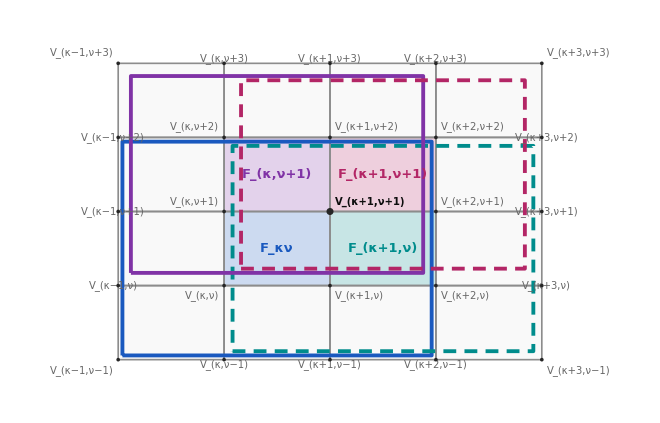
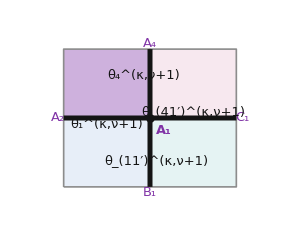
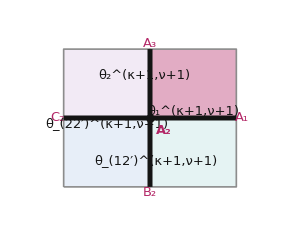
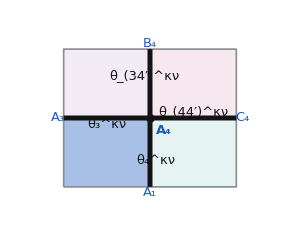
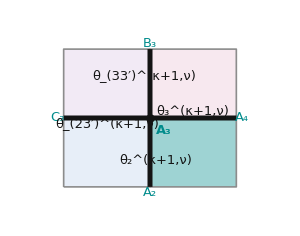
Given hypotheses and definitions:
four 3 × 3 blocks with the central faces F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1), which share the vertex V_(κ+1,ν+1)
vertex labels of the block with the central face F_κ′ν′, before any renumbering:
A_1, A_2, A_3, A_4 |  =  | V_(κ′+1,ν′), V_(κ′,ν′), V_(κ′,ν′+1), V_(κ′+1,ν′+1)
B_1, B_2, B_3, B_4 |  =  | V_(κ′+1,ν′−1), V_(κ′,ν′−1), V_(κ′,ν′+2), V_(κ′+1,ν′+2)
C_1, C_2, C_3, C_4 |  =  | V_(κ′+2,ν′), V_(κ′−1,ν′), V_(κ′−1,ν′+1), V_(κ′+2,ν′+1)
the labels V_ij are pairs of indices, and no net is assumed; two blocks share a vertex, an edge, or a face when they give it the same labels

names of the dihedral angles along the edges:
θ_1 along A_1 A_2,   θ_2 along A_2 A_3,   θ_3 along A_3 A_4,   θ_4 along A_4 A_1
θ_(11′) along A_1 B_1,   θ_(12′) along A_2 B_2,   θ_(22′) along A_2 C_2,   θ_(23′) along A_3 C_3
θ_(33′) along A_3 B_3,   θ_(34′) along A_4 B_4,   θ_(41′) along A_1 C_1,   θ_(44′) along A_4 C_4

the cyclic permutation by j relabels A_(i+j) as A_i, with the indices modulo 4 and values in {1, …, 4}; for odd j, B and C exchange their roles; it keeps the dihedral angle along each edge and only renames it
the superscript κ′ν′ marks a dihedral angle of the realization of the block with the central face F_κ′ν′, named in its labels before any renumbering

numberings of a pair of neighbours:
F_κ′ν′ and F_(κ′,ν′+1):  the first renumbered by the cyclic permutation by 2, the second kept
F_κ′ν′ and F_(κ′+1,ν′):  the first renumbered by the cyclic permutation by 3, the second by the cyclic permutation by 1

two neighbours that agree on their common faces have, in their pair numbering, with the angles of the second starred:
θ_1 = θ_1^*
θ_(11′) = θ_2^*
θ_(12′) = θ_4^*
θ_4 = θ_(12′)^*
θ_2 = θ_(11′)^*
θ_(41′) = θ_(22′)^*
θ_(22′) = θ_(41′)^*

the realizations:
F_(κ,ν+1) is realized from F_κν, and F_(κ+1,ν+1) from F_(κ+1,ν): each realization agrees on the common faces with that of the block it is realized from
F_κν and F_(κ+1,ν) agree on their common faces
in the pair numbering of F_(κ,ν+1) and F_(κ+1,ν+1), the realization of F_(κ+1,ν+1) is a polyhedron of the flexion
the hat marks the angles of the realization of F_(κ+1,ν+1) from F_(κ,ν+1), in this numbering: a polyhedron of the flexion that agrees on the common faces with the realization of F_(κ,ν+1)

in any numbering, for the polyhedron of the flexion with the parameter t and the sign e_0:
cot(θ_1/2) = t
cot(θ_4/2) = (ε_1 (t √(u x_1 y_1 (1+z_1) (1+u z_1))-e_0 e_1 √(u y_1 z_1 D(x_1, t))))/(y_1 u (z_1+x_1 t^2))
u y_1 z_1 D(x_1, t) > 0
the parameter and the sign determine the polyhedron

-Graphics-
Figure 1.  The four blocks, drawn flat, with the labels of all their vertices: the outlines mark the blocks, the tints their central faces.

in the labels of the block F_(κ,ν+1)
-Graphics- | in the labels of the block F_(κ+1,ν+1)
-Graphics-
in the labels of the block F_κν
-Graphics- | in the labels of the block F_(κ+1,ν)
-Graphics-
Figure 2.  The four faces around V_(κ+1,ν+1) and the four edges at it, once in the labels of each block: the end labels and the names of the dihedral angles along the edges are computed from the vertex labels; the darker tint marks the central face of the block.

Each ☑ below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a × would mean that this verification failed. A • marks a given fact, a definition, or an inference stated in words beside it.

We want to test the following claims ★ :

Claim 1.
◼ V_(κ+1,ν+1) is A_4 in the block F_κν, A_3 in F_(κ+1,ν), A_1 in F_(κ,ν+1), and A_2 in F_(κ+1,ν+1)
◼ each of the four blocks contains the four faces F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1) around it
the dihedral angles along the four edges at it are
◼ along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν,   θ_2^(κ+1,ν),   θ_(11′)^(κ,ν+1),   θ_(12′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν,   θ_(23′)^(κ+1,ν),   θ_1^(κ,ν+1),   θ_(22′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν,   θ_(33′)^(κ+1,ν),   θ_4^(κ,ν+1),   θ_2^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν,   θ_3^(κ+1,ν),   θ_(41′)^(κ,ν+1),   θ_1^(κ+1,ν+1)

Claim 2.
The three agreeing pairs give, at V_(κ+1,ν+1),
the blocks F_κν and F_(κ,ν+1):
◼ along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν = θ_(11′)^(κ,ν+1)
◼ along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν = θ_1^(κ,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν = θ_4^(κ,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν = θ_(41′)^(κ,ν+1)
the blocks F_κν and F_(κ+1,ν):
◼ along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν = θ_2^(κ+1,ν)
◼ along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν = θ_(23′)^(κ+1,ν)
◼ along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν = θ_(33′)^(κ+1,ν)
◼ along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν = θ_3^(κ+1,ν)
the blocks F_(κ+1,ν) and F_(κ+1,ν+1):
◼ along V_(κ+1,ν+1)V_(κ+1,ν):   θ_2^(κ+1,ν) = θ_(12′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ,ν+1):   θ_(23′)^(κ+1,ν) = θ_(22′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(33′)^(κ+1,ν) = θ_2^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_3^(κ+1,ν) = θ_1^(κ+1,ν+1)

Claim 3.
Hence, at V_(κ+1,ν+1),
◼ along V_(κ+1,ν+1)V_(κ+1,ν):   θ_(11′)^(κ,ν+1) = θ_(12′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ,ν+1):   θ_1^(κ,ν+1) = θ_(22′)^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_4^(κ,ν+1) = θ_2^(κ+1,ν+1)
◼ along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(41′)^(κ,ν+1) = θ_1^(κ+1,ν+1)

Claim 4.
◼ the realization of F_(κ+1,ν+1) from F_(κ+1,ν) coincides with its realization from F_(κ,ν+1)
◼ the blocks F_(κ,ν+1) and F_(κ+1,ν+1) agree on their common faces

Claim 1: the common vertex and the names of the angles at itVerified
Verification: the vertex labels of the four blocks, and the names of the dihedral angles along the four edges at the common vertex, computed from these labels.
(1) | V_(κ+1,ν+1) = A_4   in the block F_κν | ☑ | from the vertex labels of the block
(2) | V_(κ+1,ν+1) = A_3   in the block F_(κ+1,ν) | ☑ | from the vertex labels of the block
(3) | V_(κ+1,ν+1) = A_1   in the block F_(κ,ν+1) | ☑ | from the vertex labels of the block
(4) | V_(κ+1,ν+1) = A_2   in the block F_(κ+1,ν+1) | ☑ | from the vertex labels of the block
 |  |  | 
(5) | the block F_κν contains F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1) | ☑ | its faces are those with offsets −1, 0, 1 from its central face
(6) | the block F_(κ+1,ν) contains F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1) | ☑ | its faces are those with offsets −1, 0, 1 from its central face
(7) | the block F_(κ,ν+1) contains F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1) | ☑ | its faces are those with offsets −1, 0, 1 from its central face
(8) | the block F_(κ+1,ν+1) contains F_κν, F_(κ+1,ν), F_(κ,ν+1), F_(κ+1,ν+1) | ☑ | its faces are those with offsets −1, 0, 1 from its central face
 |  |  | 
(9) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν | ☑ | the edge A_4A_1 of the block F_κν
(10) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_2^(κ+1,ν) | ☑ | the edge A_3A_2 of the block F_(κ+1,ν)
(11) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_(11′)^(κ,ν+1) | ☑ | the edge A_1B_1 of the block F_(κ,ν+1)
(12) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_(12′)^(κ+1,ν+1) | ☑ | the edge A_2B_2 of the block F_(κ+1,ν+1)
 |  |  | 
(13) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν | ☑ | the edge A_4A_3 of the block F_κν
(14) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_(23′)^(κ+1,ν) | ☑ | the edge A_3C_3 of the block F_(κ+1,ν)
(15) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_1^(κ,ν+1) | ☑ | the edge A_1A_2 of the block F_(κ,ν+1)
(16) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_(22′)^(κ+1,ν+1) | ☑ | the edge A_2C_2 of the block F_(κ+1,ν+1)
 |  |  | 
(17) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν | ☑ | the edge A_4B_4 of the block F_κν
(18) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(33′)^(κ+1,ν) | ☑ | the edge A_3B_3 of the block F_(κ+1,ν)
(19) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_4^(κ,ν+1) | ☑ | the edge A_1A_4 of the block F_(κ,ν+1)
(20) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_2^(κ+1,ν+1) | ☑ | the edge A_2A_3 of the block F_(κ+1,ν+1)
 |  |  | 
(21) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν | ☑ | the edge A_4C_4 of the block F_κν
(22) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_3^(κ+1,ν) | ☑ | the edge A_3A_4 of the block F_(κ+1,ν)
(23) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(41′)^(κ,ν+1) | ☑ | the edge A_1C_1 of the block F_(κ,ν+1)
(24) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_1^(κ+1,ν+1) | ☑ | the edge A_2A_1 of the block F_(κ+1,ν+1)
 |  |  | 
Together, these give Claim 1.

Claim 2: the three agreeing pairs at the common vertexVerified
Verification: for each pair, the equal angles of the agreement, located by their edges in the pair numbering and named again in the labels of each block before any renumbering.
the blocks F_κν and F_(κ,ν+1):  the first renumbered by the cyclic permutation by 2, the second kept |  |  | 
(1) | the four edges at V_(κ+1,ν+1) are among the seven edges of the agreement | ☑ | the edges at a shared vertex of the pair
(2) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν = θ_(11′)^(κ,ν+1) | ☑ | from θ_2 = θ_(11′)^* in the pair numbering, both along this edge
(3) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν = θ_1^(κ,ν+1) | ☑ | from θ_1 = θ_1^* in the pair numbering, both along this edge
(4) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν = θ_4^(κ,ν+1) | ☑ | from θ_(12′) = θ_4^* in the pair numbering, both along this edge
(5) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν = θ_(41′)^(κ,ν+1) | ☑ | from θ_(22′) = θ_(41′)^* in the pair numbering, both along this edge
 |  |  | 
the blocks F_κν and F_(κ+1,ν):  the first renumbered by the cyclic permutation by 3, the second renumbered by the cyclic permutation by 1 |  |  | 
(6) | the four edges at V_(κ+1,ν+1) are among the seven edges of the agreement | ☑ | the edges at a shared vertex of the pair
(7) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_4^κν = θ_2^(κ+1,ν) | ☑ | from θ_1 = θ_1^* in the pair numbering, both along this edge
(8) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_3^κν = θ_(23′)^(κ+1,ν) | ☑ | from θ_4 = θ_(12′)^* in the pair numbering, both along this edge
(9) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(34′)^κν = θ_(33′)^(κ+1,ν) | ☑ | from θ_(41′) = θ_(22′)^* in the pair numbering, both along this edge
(10) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_(44′)^κν = θ_3^(κ+1,ν) | ☑ | from θ_(11′) = θ_2^* in the pair numbering, both along this edge
 |  |  | 
the blocks F_(κ+1,ν) and F_(κ+1,ν+1):  the first renumbered by the cyclic permutation by 2, the second kept |  |  | 
(11) | the four edges at V_(κ+1,ν+1) are among the seven edges of the agreement | ☑ | the edges at a shared vertex of the pair
(12) | along V_(κ+1,ν+1)V_(κ+1,ν):   θ_2^(κ+1,ν) = θ_(12′)^(κ+1,ν+1) | ☑ | from θ_4 = θ_(12′)^* in the pair numbering, both along this edge
(13) | along V_(κ+1,ν+1)V_(κ,ν+1):   θ_(23′)^(κ+1,ν) = θ_(22′)^(κ+1,ν+1) | ☑ | from θ_(41′) = θ_(22′)^* in the pair numbering, both along this edge
(14) | along V_(κ+1,ν+1)V_(κ+1,ν+2):   θ_(33′)^(κ+1,ν) = θ_2^(κ+1,ν+1) | ☑ | from θ_(11′) = θ_2^* in the pair numbering, both along this edge
(15) | along V_(κ+1,ν+1)V_(κ+2,ν+1):   θ_3^(κ+1,ν) = θ_1^(κ+1,ν+1) | ☑ | from θ_1 = θ_1^* in the pair numbering, both along this edge
 |  |  | 
Together, these give Claim 2.

Claim 3: the chains around the common vertexVerified
Verification: along each edge at the common vertex, the equalities of Claim 2 form a chain through the four blocks.
(1) | θ_(11′)^(κ,ν+1) = θ_4^κν = θ_2^(κ+1,ν) = θ_(12′)^(κ+1,ν+1) | ☑ | along V_(κ+1,ν+1)V_(κ+1,ν); each equality is one of Claim 2
(2) | θ_(11′)^(κ,ν+1) = θ_(12′)^(κ+1,ν+1) | ☑ | the two ends of this chain
 |  |  | 
(3) | θ_1^(κ,ν+1) = θ_3^κν = θ_(23′)^(κ+1,ν) = θ_(22′)^(κ+1,ν+1) | ☑ | along V_(κ+1,ν+1)V_(κ,ν+1); each equality is one of Claim 2
(4) | θ_1^(κ,ν+1) = θ_(22′)^(κ+1,ν+1) | ☑ | the two ends of this chain
 |  |  | 
(5) | θ_4^(κ,ν+1) = θ_(34′)^κν = θ_(33′)^(κ+1,ν) = θ_2^(κ+1,ν+1) | ☑ | along V_(κ+1,ν+1)V_(κ+1,ν+2); each equality is one of Claim 2
(6) | θ_4^(κ,ν+1) = θ_2^(κ+1,ν+1) | ☑ | the two ends of this chain
 |  |  | 
(7) | θ_(41′)^(κ,ν+1) = θ_(44′)^κν = θ_3^(κ+1,ν) = θ_1^(κ+1,ν+1) | ☑ | along V_(κ+1,ν+1)V_(κ+2,ν+1); each equality is one of Claim 2
(8) | θ_(41′)^(κ,ν+1) = θ_1^(κ+1,ν+1) | ☑ | the two ends of this chain
 |  |  | 
Together, these give Claim 3.

Claim 4: the realization of the fourth blockVerified
Verification: the angles along the two edges of its central face at the common vertex, in the pair numbering, and the difference of the two values of the angle for the two signs.
in the pair numbering of F_(κ,ν+1) and F_(κ+1,ν+1):  the first renumbered by the cyclic permutation by 3, the second by the cyclic permutation by 1 |  |  | 
(1) | θ_1^* of the realization of F_(κ+1,ν+1) from F_(κ+1,ν)  is  θ_2^(κ+1,ν+1) | ☑ | both along V_(κ+1,ν+1)V_(κ+1,ν+2)
(2) | θ_4^* of the realization of F_(κ+1,ν+1) from F_(κ+1,ν)  is  θ_1^(κ+1,ν+1) | ☑ | both along V_(κ+1,ν+1)V_(κ+2,ν+1)
(3) | θ_1 of the realization of F_(κ,ν+1)  is  θ_4^(κ,ν+1) | ☑ | both along V_(κ+1,ν+1)V_(κ+1,ν+2)
(4) | θ_(12′) of the realization of F_(κ,ν+1)  is  θ_(41′)^(κ,ν+1) | ☑ | both along V_(κ+1,ν+1)V_(κ+2,ν+1)
 |  |  | 
(5) | (θ̂)_1^* = θ_4^(κ,ν+1) | • | the realization of F_(κ+1,ν+1) from F_(κ,ν+1) agrees with the realization of F_(κ,ν+1): (θ̂)_1^* = θ_1, with (3)
(6) | (θ̂)_4^* = θ_(41′)^(κ,ν+1) | • | the same agreement: (θ̂)_4^* = θ_(12′), with (4)
(7) | θ_1^* = (θ̂)_1^* | • | by (1), (5), and Claim 3: θ_2^(κ+1,ν+1) = θ_4^(κ,ν+1)
(8) | θ_4^* = (θ̂)_4^* | • | by (2), (6), and Claim 3: θ_1^(κ+1,ν+1) = θ_(41′)^(κ,ν+1)
 |  |  | 
(9) | the same parameter | • | by (7), because cot(θ_1/2) is the parameter
(10) | cot(θ_4/2) at e_0 = 1  minus  cot(θ_4/2) at e_0 = −1   =   -(2 ε_1 e_1 √(u y_1 z_1 D(x_1, t)))/(y_1 u (z_1+x_1 t^2)) | ☑ | nonzero, because u y_1 z_1 D(x_1, t) > 0 and ε_1e_1 = ±1
(11) | the same sign | • | by (8)–(10): for the same parameter, the two signs give different values of the angle
(12) | the realization of F_(κ+1,ν+1) from F_(κ+1,ν) coincides with its realization from F_(κ,ν+1) | • | by (9) and (11): the parameter and the sign determine the polyhedron
(13) | the blocks F_(κ,ν+1) and F_(κ+1,ν+1) agree on their common faces | • | by (12), because the realization of F_(κ+1,ν+1) from F_(κ,ν+1) agrees with the realization of F_(κ,ν+1)
Together, these give Claim 4.

ALL CLAIMS VERIFIED

```mathematica
(* ============================================================*)(*PART 1:SETUP*)(* ============================================================*)ClearAll[statusChip,smallChip,givenChip,colTest,cols,bullet,ind,vlift,idxB,ptB,pt,edg,evec,nv,wv,tld,gk,thI,bx,cotSqTag,cotTag,mulR,absR,frac,caseDef,note,firstBase,nrow,prow,hrow,vgap,vgrid,iv,trigNames,simpleBoxQ,trigBoxRule,disp,dispRule,ptBS,ptS,edgS,evecS,gkS,thK,thKS,nvK,nvKS,tilD,tilDS,itl,supS,supG,tilO,tupD,quadD,vLab,vLabP,lab,ren,minusT,cotF,t,e0,e1,u,x1,y1,z1,ep1,dd,blocks,bOrder,bSup,bCol,faceB,thB,thS,thHS,cornerDef,edgesNamed,nameOf,vV,dirs,far,edgeAt,dirLab,expNames,expV,pairs7,agreePairs,pairAtV,sortedAtV,labelOf,fig1,frame,fig2,okC1,okC2,okC3,okC4,resultsAll];
statusChip[True]:=Framed[Style["Verified",Bold,White,13],Background->RGBColor[0.13,0.55,0.13],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
statusChip[False]:=Framed[Style["Failed",Bold,White,13],Background->RGBColor[0.82,0.10,0.10],FrameStyle->None,RoundingRadius->7,FrameMargins->{{12,12},{4,4}}];
smallChip[True]:=Style["☑",14,RGBColor[0.13,0.55,0.13]];
smallChip[False]:=Style["×",14,Bold,RGBColor[0.82,0.10,0.10]];
givenChip=Style["•",12,GrayLevel[0.45]];
colTest=RGBColor[0.10,0.35,0.75];
cols={RGBColor[0.10,0.35,0.75],RGBColor[0.50,0.20,0.65],RGBColor[0.00,0.55,0.55],RGBColor[0.20,0.50,0.20],RGBColor[0.75,0.35,0.05],RGBColor[0.70,0.15,0.40],RGBColor[0.30,0.25,0.70],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35]};
bullet=Style["◼ ",12,colTest];ind="    ";vlift=0.16;
idxB[x_]:=If[IntegerQ[x],ToString[x],StyleBox[ToString[x],FontSlant->"Italic"]];
ptB[s_,i_]:=SubscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i]];pt[s_,i_]:=DisplayForm[ptB[s,i]];
edg[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptB[s1,i1],ptB[s2,i2]}]];
evec[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptB[s1,i1],ptB[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
nv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
wv[x_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["w",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],idxB[x]]];
tld[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
gk[g_,i_]:=DisplayForm[SubscriptBox[g,idxB[i]]];
thI[x_]:=DisplayForm[SubscriptBox["θ",idxB[x]]];
bx[DisplayForm[b_]]:=b;bx[x_]:=ToBoxes[x,TraditionalForm];
cotSqTag[t_]:=DisplayForm[RowBox[{SuperscriptBox["cot","2"],"(",bx[t],"/","2",")"}]];
cotTag[t_]:=DisplayForm[RowBox[{"cot","(",bx[t],"/","2",")"}]];
mulR[args___]:=Row[Riffle[{args}," "]];absR[e_]:=Row[{"|",e,"|"}];
frac[num_,den_]:=DisplayForm[FractionBox[bx[num],bx[den]]];
caseDef[lhs_,rows_]:=DisplayForm[RowBox[{bx[lhs]," ∶= ",StyleBox["{",SpanMaxSize->Infinity],GridBox[Map[bx,rows,{2}],ColumnAlignments->Left,ColumnSpacings->1.6,RowSpacings->0.9]}]];
note[s_]:=Style[s,12,GrayLevel[0.5]];
firstBase[e_]:=If[Head[e]===Column,Append[e,BaselinePosition->{1,1}],e];
(*a numbered line,an unnumbered line (for a name),and a heading line of a block*)
nrow[n_,stmt_,mark_,nt_]:={Style["("<>ToString[n]<>")",13],Style[firstBase[stmt],13],mark,note[nt]};
prow[stmt_,mark_,nt_]:={"",Style[firstBase[stmt],13],mark,note[nt]};
hrow[t_]:={Style[t,13],SpanFromLeft,SpanFromLeft,SpanFromLeft};
vgap={"",Spacer[{0,7}],"",""};
vgrid[rows_]:=Grid[rows,Alignment->{Left,Baseline},Spacings->{1.2,0.8}];
(*every symbol that is only displayed is a string,so that no value given to a symbol elsewhere in the notebook can enter the display;the displayed index i is an italic string as well*)
iv=Style["i",Italic];
trigNames={"sin","cos","tan","cot","sec","csc"};
simpleBoxQ[b_String]:=True;simpleBoxQ[StyleBox[b_,___]]:=simpleBoxQ[b];
simpleBoxQ[(SubscriptBox|SuperscriptBox|OverscriptBox|UnderscriptBox)[bs__]]:=AllTrue[{bs},simpleBoxQ];simpleBoxQ[_]:=False;
trigBoxRule={RowBox[{f_String/;MemberQ[trigNames,f],"(",a_,")"}]/;simpleBoxQ[a]:>RowBox[{f," ",a}],RowBox[{f_String/;MemberQ[trigNames,f],RowBox[{"(",a_,")"}]}]/;simpleBoxQ[a]:>RowBox[{f," ",a}]};
disp[e_]:=DisplayForm[ToBoxes[e/. dispRule,TraditionalForm]//.trigBoxRule];
(*a starred label marks the polyhedron with the second central face;indices given as strings are set upright*)
ptBS[s_,i_]:=SubsuperscriptBox[StyleBox[s,FontSlant->"Italic"],idxB[i],"*"];ptS[s_,i_]:=DisplayForm[ptBS[s,i]];
edgS[s1_,i1_,s2_,i2_]:=DisplayForm[RowBox[{ptBS[s1,i1],ptBS[s2,i2]}]];
evecS[s1_,i1_,s2_,i2_]:=DisplayForm[OverscriptBox[RowBox[{ptBS[s1,i1],ptBS[s2,i2]}],AdjustmentBox["⟶",BoxBaselineShift->-vlift]]];
gkS[g_,i_]:=DisplayForm[SubsuperscriptBox[g,idxB[i],"*"]];
thK[k_String]:=DisplayForm[SubscriptBox["θ",k]];thKS[k_String]:=DisplayForm[SubsuperscriptBox["θ",k,"*"]];
nvK[k_String]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],k]];
nvKS[k_String]:=DisplayForm[SubsuperscriptBox[OverscriptBox[StyleBox["n",FontSlant->"Italic"],AdjustmentBox["→",BoxBaselineShift->-vlift]],k,"*"]];
tilD[s_,i_]:=DisplayForm[SubscriptBox[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"],idxB[i]]];
tilDS[s_,i_]:=DisplayForm[SubsuperscriptBox[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"],idxB[i],"*"]];
itl[s_]:=DisplayForm[StyleBox[s,FontSlant->"Italic"]];
supS[s_]:=DisplayForm[SuperscriptBox[StyleBox[s,FontSlant->"Italic"],"*"]];supG[g_]:=DisplayForm[SuperscriptBox[g,"*"]];
tilO[s_]:=DisplayForm[OverscriptBox[StyleBox[s,FontSlant->"Italic"],"~"]];
tupD[l_List]:=Row[{"(",Row[Riffle[disp/@l,", "]],")"}];
quadD[l_List]:=Row[{"(",Row[Riffle[l,", "]],")"}];
(*a vertex label V,given by its offsets {a,b} from (kappa,nu)*)
vLab[{a_,b_}]:=Module[{f},f[s_,k_]:=s<>Which[k==0,"",k>0,"+"<>ToString[k],True,"−"<>ToString[-k]];DisplayForm[SubscriptBox[StyleBox["V",FontSlant->"Italic"],RowBox[{f["κ",a],",",f["ν",b]}]]]];
(*the formulas are displayed through these strings,so that no value of a symbol enters the display*)
dispRule={al[k_]:>Subscript["α",k],be[k_]:>Subscript["β",k],ga[k_]:>Subscript["γ",k],de[k_]:>Subscript["δ",k],t->Style["t",Italic],u->Style["u",Italic],e0->Subscript[Style["e",Italic],0],e1->Subscript[Style["e",Italic],1],e2->Subscript[Style["e",Italic],2],x1->Subscript[Style["x",Italic],1],y1->Subscript[Style["y",Italic],1],z1->Subscript[Style["z",Italic],1],y2->Subscript[Style["y",Italic],2],z2->Subscript[Style["z",Italic],2],yt1->Subscript[OverTilde[Style["y",Italic]],1],zt1->Subscript[OverTilde[Style["z",Italic]],1],yt2->Subscript[OverTilde[Style["y",Italic]],2],zt2->Subscript[OverTilde[Style["z",Italic]],2],ep1->Subscript["ε",1],ep2->Subscript["ε",2],dd->Row[{Style["D",Italic],"(",Subscript[Style["x",Italic],1],", ",Style["t",Italic],")"}]};


(*the vertex labels V,given by their offsets from (kappa',nu')*)
vLabP[{a_,b_}]:=Module[{f},f[s_,k_]:=s<>Which[k==0,"",k>0,"+"<>ToString[k],True,"−"<>ToString[-k]];DisplayForm[SubscriptBox[StyleBox["V",FontSlant->"Italic"],RowBox[{f["κ′",a],",",f["ν′",b]}]]]];
dispRule={t->Style["t",Italic],u->Style["u",Italic],e0->Subscript[Style["e",Italic],0],e1->Subscript[Style["e",Italic],1],x1->Subscript[Style["x",Italic],1],y1->Subscript[Style["y",Italic],1],z1->Subscript[Style["z",Italic],1],ep1->Subscript["ε",1],dd->Row[{Style["D",Italic],"(",Subscript[Style["x",Italic],1],", ",Style["t",Italic],")"}]};
(*the formula of the dihedral angle theta4,held so that its terms keep the written order,and the same formula for the computation*)
minusT[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=HoldForm[a1 (t Sqrt[a6 a2 a3 (1+a4) (1+a6 a4)]-e0 a5 Sqrt[a6 a3 a4 a7])/(a3 a6 (a4+a2 t^2))];
cotF[ep_,yy_,zz_,sg_]:=ep (t Sqrt[u x1 yy (1+zz) (1+u zz)]+sg e0 Sqrt[u yy zz dd])/(yy u (zz+x1 t^2));

(*the four blocks,by the offsets of their central faces from (kappa,nu),with their superscripts and colours*)
blocks=<|"kn"->{0,0},"k1n"->{1,0},"kn1"->{0,1},"k1n1"->{1,1}|>;
bOrder={"kn","k1n","kn1","k1n1"};
bSup=<|"kn"->RowBox[{"κ","ν"}],"k1n"->RowBox[{"κ+1",",","ν"}],"kn1"->RowBox[{"κ",",","ν+1"}],"k1n1"->RowBox[{"κ+1",",","ν+1"}]|>;
bCol=<|"kn"->RGBColor[0.10,0.35,0.75],"k1n"->RGBColor[0.00,0.55,0.55],"kn1"->RGBColor[0.50,0.20,0.65],"k1n1"->RGBColor[0.70,0.15,0.40]|>;
faceB[b_]:=DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],bSup[b]]];
thB[k_String,b_]:=DisplayForm[SubsuperscriptBox["θ",k,bSup[b]]];
thS[k_String]:=DisplayForm[SubsuperscriptBox["θ",k,"*"]];
thHS[k_String]:=DisplayForm[SubsuperscriptBox[OverscriptBox["θ","^"],k,"*"]];
lab[{a0_,b0_}]:=Module[{add=#+{a0,b0}&},<|"A"->add/@{{1,0},{0,0},{0,1},{1,1}},"B"->add/@{{1,-1},{0,-1},{0,2},{1,2}},"C"->add/@{{2,0},{-1,0},{-1,1},{2,1}}|>];
(*the cyclic permutation of the indices by j:A_(i+j) becomes A_i,and,for odd j,B and C exchange their roles,and so do alpha and gamma*)
ren[l_,j_]:=Module[{o=Mod[Range[4]+j,4,1]},<|"A"->l["A"][[o]],"B"->If[OddQ[j],l["C"],l["B"]][[o]],"C"->If[OddQ[j],l["B"],l["C"]][[o]]|>];
(*the names of the dihedral angles by their edges:theta_i along A_i A_(i+1),and the corner ones along the edges listed here*)
cornerDef={{"11′","A",1,"B",1},{"12′","A",2,"B",2},{"22′","A",2,"C",2},{"23′","A",3,"C",3},{"33′","A",3,"B",3},{"34′","A",4,"B",4},{"41′","A",1,"C",1},{"44′","A",4,"C",4}};
edgesNamed[l_]:=Association[Join[Table[ToString[i]->Sort[{l["A"][[i]],l["A"][[Mod[i+1,4,1]]]}],{i,4}],(#[[1]]->Sort[{l[#[[2]]][[#[[3]]]],l[#[[4]]][[#[[5]]]]}])&/@cornerDef]];
nameOf[l_,e_]:=Module[{k=Keys[Select[edgesNamed[l],#===Sort[e]&]]},If[k==={},None,First[k]]];
labelOf[b_,off_]:=Module[{l=lab[blocks[b]],hit},hit=Select[Flatten[Table[{k,i},{k,{"A","B","C"}},{i,4}],1],l[#[[1]]][[#[[2]]]]===off&];If[hit==={},None,First[hit]]];
(*the common vertex V_(kappa+1,nu+1) and the far ends of the four edges at it,as offsets from (kappa,nu)*)
vV={1,1};
dirs={"down","left","up","right"};
far=<|"down"->{1,0},"left"->{0,1},"up"->{1,2},"right"->{2,1}|>;
edgeAt[d_]:=Sort[{vV,far[d]}];
dirLab[d_]:=Row[{vLab[vV],vLab[far[d]]}];
(*the names stated in Claim 1*)
expV=<|"kn"->4,"k1n"->3,"kn1"->1,"k1n1"->2|>;
expNames=<|"down"-><|"kn"->"4","k1n"->"2","kn1"->"11′","k1n1"->"12′"|>,"left"-><|"kn"->"3","k1n"->"23′","kn1"->"1","k1n1"->"22′"|>,"up"-><|"kn"->"34′","k1n"->"33′","kn1"->"4","k1n1"->"2"|>,"right"-><|"kn"->"44′","k1n"->"3","kn1"->"41′","k1n1"->"1"|>|>;
(*two neighbours with the same parameter and sign agree:in their pair numbering,the angle of the first on the left equals the starred angle of the second on the right*)
pairs7={{"1","1"},{"11′","2"},{"12′","4"},{"4","12′"},{"2","11′"},{"41′","22′"},{"22′","41′"}};
(*the three agreeing pairs:first block,second block,and the renumberings of the pair*)
agreePairs={{"kn","kn1",2,0},{"kn","k1n",3,1},{"k1n","k1n1",2,0}};
(*for a pair,the agreements along the edges at V:whether both names give the same edge,the edge,the two names before any renumbering,and the pair of names in the pair numbering*)
pairAtV[{b1_,b2_,j1_,j2_}]:=Module[{l1=ren[lab[blocks[b1]],j1],l2=ren[lab[blocks[b2]],j2]},Select[Table[With[{e1=edgesNamed[l1][p[[1]]],e2=edgesNamed[l2][p[[2]]]},{e1===e2,e1,nameOf[lab[blocks[b1]],e1],nameOf[lab[blocks[b2]],e2],p}],{p,pairs7}],MemberQ[#[[2]],vV]&]];
(*the agreements of a pair along the edges at V,in the order down,left,up,right*)
sortedAtV[pr_]:=SortBy[pairAtV[pr],Function[q,First[Flatten[Position[edgeAt/@dirs,q[[2]]]]]]];
resultsAll={};

(*Figure 1:the four blocks,drawn flat,with the labels of all vertices;the numbers of the drawing enter no verification*)
fig1=Module[{P,fcol,faces,outl,vlabs,dots,flabs,place},P[{a_,b_}]:={150 a,105 b};
fcol[o_]:=Module[{k=Select[bOrder,blocks[#]===o&]},If[k==={},None,bCol[First[k]]]];
faces=Flatten[Table[{If[fcol[{a,b}]===None,FaceForm[GrayLevel[0.975]],FaceForm[Directive[fcol[{a,b}],Opacity[0.22]]]],EdgeForm[{GrayLevel[0.55],Thickness[0.0018]}],Polygon[P/@{{a,b},{a+1,b},{a+1,b+1},{a,b+1}}]},{a,-1,2},{b,-1,2}],1];
outl=MapThread[{#2,Thickness[0.0042],If[#4,Dashing[{0.014,0.009}],Dashing[{}]],Line[{P[#1-{1,1}]+{#3,#3},P[#1+{2,-1}]+{-#3,#3},P[#1+{2,2}]-{#3,#3},P[#1+{-1,2}]+{#3,-#3},P[#1-{1,1}]+{#3,#3}}]}&,{blocks/@bOrder,bCol/@bOrder,{6,12,18,24},{False,True,False,True}}];
dots={GrayLevel[0.15],Table[Disk[P[{a,b}],If[{a,b}==vV,5,2.6]],{a,-1,3},{b,-1,3}]};
(*the place of a vertex label,and the corner of the label at that place:outside the mesh for a vertex on its boundary;for an inner vertex,in the face on the far side from the common vertex,and for the common vertex,in the face to its upper right;no outline of a block runs there near the vertex*)place[{a_,b_}]:=Module[{sx,sy},If[MemberQ[{-1,3},a]||MemberQ[{-1,3},b],sx=Which[a==-1,-1,a==3,1,True,0];sy=Which[b==-1,-1,b==3,1,True,0],sx=If[a==1,1,Sign[a-1]];sy=If[b==1,1,Sign[b-1]]];
{P[{a,b}]+7 {sx,sy},-{sx,sy}}];
vlabs=Flatten[Table[With[{pl=place[{a,b}]},Text[Style[vLab[{a,b}],10,If[{a,b}==vV,Bold,Plain],GrayLevel[If[{a,b}==vV,0.05,0.4]]],pl[[1]],pl[[2]]]],{a,-1,3},{b,-1,3}]];
flabs=Text[Style[faceB[#],13,Bold,bCol[#]],P[blocks[#]]+{75,52}]&/@bOrder;
Graphics[{faces,outl,dots,vlabs,flabs},ImageSize->660,PlotRange->{{-232,532},{-140,350}},Background->None,BaseStyle->{FontFamily->"Times"}]];

(*Figure 2:the four faces around V_(kappa+1,nu+1) and the four edges at it,in the labels of one block;the names are computed from the labels*)
frame[b_]:=Module[{P,faces,thick,ends,names,vlab,at},P[{a_,c_}]:={100 a,80 c};
faces=Table[With[{k=First[Select[bOrder,blocks[#]==={a,c}&]]},{FaceForm[Directive[bCol[k],Opacity[If[k===b,0.38,0.1]]]],EdgeForm[{GrayLevel[0.55],Thickness[0.004]}],Polygon[P/@{{a,c},{a+1,c},{a+1,c+1},{a,c+1}}]}],{a,0,1},{c,0,1}];
thick={GrayLevel[0.08],Thickness[0.012],Line[{P[vV],P[far[#]]}]&/@dirs};
(*the point at the fraction f of the edge from the common vertex to its far end*)at[d_,f_]:=P[vV]+f (P[far[d]]-P[vV]);
(*the end labels outside the four faces;each name in its own face,beside its edge;the label of the common vertex in the lower right face,above the name there*)ends=Text[Style[With[{lb=labelOf[b,far[#[[1]]]]},pt[lb[[1]],lb[[2]]]],13,bCol[b]],P[far[#[[1]]]]+#[[2]],#[[3]]]&/@{{"down",{0,-7},{0,1}},{"left",{-7,0},{1,0}},{"up",{0,7},{0,-1}},{"right",{7,0},{-1,0}}};
names=Text[Style[thB[nameOf[lab[blocks[b]],edgeAt[#[[1]]]],b],13,GrayLevel[0.08]],at[#[[1]],#[[4]]]+#[[2]],#[[3]]]&/@{{"down",{7,0},{-1,0},0.62},{"right",{0,7},{0,-1},0.5},{"up",{-7,0},{1,0},0.62},{"left",{0,-7},{0,1},0.5}};
vlab=Text[Style[With[{lb=labelOf[b,vV]},pt[lb[[1]],lb[[2]]]],13,Bold,bCol[b]],P[vV]+{7,-7},{-1,1}];
Graphics[{faces,thick,{GrayLevel[0.08],Disk[P[vV],5]},ends,names,vlab},ImageSize->300,PlotRange->{{-42,242},{-32,192}},Background->None,BaseStyle->{FontFamily->"Times"}]];
fig2=Grid[{{Column[{Style[Row[{"in the labels of the block ",faceB["kn1"]}],12,bCol["kn1"]],frame["kn1"]},Alignment->Center],Column[{Style[Row[{"in the labels of the block ",faceB["k1n1"]}],12,bCol["k1n1"]],frame["k1n1"]},Alignment->Center]},{Column[{Style[Row[{"in the labels of the block ",faceB["kn"]}],12,bCol["kn"]],frame["kn"]},Alignment->Center],Column[{Style[Row[{"in the labels of the block ",faceB["k1n"]}],12,bCol["k1n"]],frame["k1n"]},Alignment->Center]}},Spacings->{3,2}];

(* ============================================================*)(*PART 2:GIVEN PANEL*)(* ============================================================*)Print[Panel[Column[{Style["Given hypotheses and definitions:",Bold,14],Style[Row[{"four 3 × 3 blocks with the central faces ",faceB["kn"],", ",faceB["k1n"],", ",faceB["kn1"],", ",faceB["k1n1"],", which share the vertex ",vLab[vV]}],13],Style[Row[{"vertex labels of the block with the central face ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′","ν′"}]]],", before any renumbering:"}],13],Style[Grid[{{Row[{pt["A",1],", ",pt["A",2],", ",pt["A",3],", ",pt["A",4]}]," = ",Row[Riffle[vLabP/@{{1,0},{0,0},{0,1},{1,1}},", "]]},{Row[{pt["B",1],", ",pt["B",2],", ",pt["B",3],", ",pt["B",4]}]," = ",Row[Riffle[vLabP/@{{1,-1},{0,-1},{0,2},{1,2}},", "]]},{Row[{pt["C",1],", ",pt["C",2],", ",pt["C",3],", ",pt["C",4]}]," = ",Row[Riffle[vLabP/@{{2,0},{-1,0},{-1,1},{2,1}},", "]]}},Alignment->Left,Spacings->{0.6,0.5}],13],note[Row[{"the labels ",DisplayForm[SubscriptBox[StyleBox["V",FontSlant->"Italic"],RowBox[{StyleBox["i",FontSlant->"Italic"],StyleBox["j",FontSlant->"Italic"]}]]]," are pairs of indices, and no net is assumed; two blocks share a vertex, an edge, or a face when they give it the same labels"}]],Spacer[{0,6}],Style["names of the dihedral angles along the edges:",13],Style[Column[{Row[Riffle[Table[Row[{thK[ToString[i]]," along ",edg["A",i,"A",Mod[i+1,4,1]]}],{i,4}],",   "]],Row[Riffle[Row[{thK[#[[1]]]," along ",edg[#[[2]],#[[3]],#[[4]],#[[5]]]}]&/@cornerDef[[1;;4]],",   "]],Row[Riffle[Row[{thK[#[[1]]]," along ",edg[#[[2]],#[[3]],#[[4]],#[[5]]]}]&/@cornerDef[[5;;8]],",   "]]},Spacings->0.5],13],Spacer[{0,6}],note[Row[{"the cyclic permutation by j relabels ",pt["A","i+j"]," as ",pt["A","i"],", with the indices modulo 4 and values in {1, …, 4}; for odd j, B and C exchange their roles; it keeps the dihedral angle along each edge and only renames it"}]],Style[Row[{"the superscript κ′ν′ marks a dihedral angle of the realization of the block with the central face ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′","ν′"}]]],", named in its labels before any renumbering"}],13],Spacer[{0,6}],Style["numberings of a pair of neighbours:",13],Style[Column[{Row[{DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′","ν′"}]]]," and ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′",",","ν′+1"}]]],":  the first renumbered by the cyclic permutation by 2, the second kept"}],Row[{DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′","ν′"}]]]," and ",DisplayForm[SubscriptBox[StyleBox["F",FontSlant->"Italic"],RowBox[{"κ′+1",",","ν′"}]]],":  the first renumbered by the cyclic permutation by 3, the second by the cyclic permutation by 1"}]},Spacings->0.5],13],Spacer[{0,6}],Style["two neighbours that agree on their common faces have, in their pair numbering, with the angles of the second starred:",13],Style[Column[Row[{thK[#[[1]]]," = ",thS[#[[2]]]}]&/@pairs7,Spacings->0.5],13],Spacer[{0,6}],Style["the realizations:",13],Style[Column[{Row[{faceB["kn1"]," is realized from ",faceB["kn"],", and ",faceB["k1n1"]," from ",faceB["k1n"],": each realization agrees on the common faces with that of the block it is realized from"}],Row[{faceB["kn"]," and ",faceB["k1n"]," agree on their common faces"}],Row[{"in the pair numbering of ",faceB["kn1"]," and ",faceB["k1n1"],", the realization of ",faceB["k1n1"]," is a polyhedron of the flexion"}],Row[{"the hat marks the angles of the realization of ",faceB["k1n1"]," from ",faceB["kn1"],", in this numbering: a polyhedron of the flexion that agrees on the common faces with the realization of ",faceB["kn1"]}]},Spacings->0.6],13],Spacer[{0,6}],Style[Row[{"in any numbering, for the polyhedron of the flexion with the parameter ",itl["t"]," and the sign ",pt["e",0],":"}],13],Style[Column[{Row[{cotTag[thK["1"]]," = ",itl["t"]}],Row[{cotTag[thK["4"]]," = ",disp[minusT[ep1,x1,y1,z1,e1,u,dd]]}],Row[{disp[HoldForm[u y1 z1 dd]]," > 0"}],Row[{"the parameter and the sign determine the polyhedron"}]},Spacings->0.9],13],Spacer[{0,8}],Column[{fig1,Style[Row[{"Figure 1.  The four blocks, drawn flat, with the labels of all their vertices: the outlines mark the blocks, the tints their central faces."}],12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,10}],Column[{fig2,Style[Row[{"Figure 2.  The four faces around ",vLab[vV]," and the four edges at it, once in the labels of each block: the end labels and the names of the dihedral angles along the edges are computed from the vertex labels; the darker tint marks the central face of the block."}],12,GrayLevel[0.5]]},Alignment->Center],Spacer[{0,8}],Style[Row[{"Each ",smallChip[True]," below certifies that the statement displayed beside it has been verified by a symbolic computation at that point; a ",smallChip[False]," would mean that this verification failed. A ",givenChip," marks a given fact, a definition, or an inference stated in words beside it."}],12,GrayLevel[0.35]],"",Style[Row[{Style["We want to test the following claims ",Bold,14],Style["★",14,colTest],Style[" :",Bold,14]}]],Spacer[{0,6}],Style["Claim 1.",Bold,13,colTest],Row[{bullet,Style[Row[{vLab[vV]," is ",pt["A",4]," in the block ",faceB["kn"],", ",pt["A",3]," in ",faceB["k1n"],", ",pt["A",1]," in ",faceB["kn1"],", and ",pt["A",2]," in ",faceB["k1n1"]}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"each of the four blocks contains the four faces ",faceB["kn"],", ",faceB["k1n"],", ",faceB["kn1"],", ",faceB["k1n1"]," around it"}],Bold,13,colTest]}],Style["the dihedral angles along the four edges at it are",Bold,13,colTest],Sequence@@(Row[{bullet,Style[Row[{"along ",dirLab[#],":   ",Row[Riffle[Table[thB[expNames[#][b],b],{b,bOrder}],",   "]]}],Bold,13,colTest]}]&/@dirs),Spacer[{0,10}],Style["Claim 2.",Bold,13,colTest],Style[Row[{"The three agreeing pairs give, at ",vLab[vV],","}],Bold,13,colTest],Sequence@@Flatten[Table[With[{pr=pr0,eqs=sortedAtV[pr0]},Join[{Pane[Style[Row[{"the blocks ",faceB[pr[[1]]]," and ",faceB[pr[[2]]],":"}],Bold,13,colTest],FrameMargins->{{0,0},{0,8}}]},(Function[q,Row[{bullet,Style[Row[{"along ",dirLab[First[Select[dirs,edgeAt[#]===q[[2]]&]]],":   ",thB[q[[3]],pr[[1]]]," = ",thB[q[[4]],pr[[2]]]}],Bold,13,colTest]}]]/@eqs)]],{pr0,agreePairs}]],Spacer[{0,10}],Style["Claim 3.",Bold,13,colTest],Style[Row[{"Hence, at ",vLab[vV],","}],Bold,13,colTest],Sequence@@(Row[{bullet,Style[Row[{"along ",dirLab[#],":   ",thB[expNames[#]["kn1"],"kn1"]," = ",thB[expNames[#]["k1n1"],"k1n1"]}],Bold,13,colTest]}]&/@dirs),Spacer[{0,10}],Style["Claim 4.",Bold,13,colTest],Row[{bullet,Style[Row[{"the realization of ",faceB["k1n1"]," from ",faceB["k1n"]," coincides with its realization from ",faceB["kn1"]}],Bold,13,colTest]}],Row[{bullet,Style[Row[{"the blocks ",faceB["kn1"]," and ",faceB["k1n1"]," agree on their common faces"}],Bold,13,colTest]}]},Spacings->1.1],Background->RGBColor[0.99,0.96,0.88],FrameMargins->14]];

(* ============================================================*)
(*PART 3:CLAIM 1*)
(* ============================================================*)
Module[{col=cols[[1]],oks={},chk,rows,n=0,nx,endLab},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
nx[]:=(n++;n);
endLab[b_,o_]:=With[{lb=labelOf[b,o]},pt[lb[[1]],lb[[2]]]];
rows=Join[Table[nrow[nx[],Row[{vLab[vV]," = ",pt["A",expV[b]],"   in the block ",faceB[b]}],smallChip[chk[labelOf[b,vV]==={"A",expV[b]}]],"from the vertex labels of the block"],{b,bOrder}],{vgap},Table[nrow[nx[],Row[{"the block ",faceB[b]," contains ",faceB["kn"],", ",faceB["k1n"],", ",faceB["kn1"],", ",faceB["k1n1"]}],smallChip[chk[Complement[blocks/@bOrder,Flatten[Table[blocks[b]+{a,c},{a,-1,1},{c,-1,1}],1]]==={}]],"its faces are those with offsets −1, 0, 1 from its central face"],{b,bOrder}],{vgap},Flatten[Table[Join[Table[nrow[nx[],Row[{"along ",dirLab[d],":   ",thB[expNames[d][b],b]}],smallChip[chk[nameOf[lab[blocks[b]],edgeAt[d]]===expNames[d][b]]],Row[{"the edge ",endLab[b,vV],endLab[b,far[d]]," of the block ",faceB[b]}]],{b,bOrder}],{vgap}],{d,dirs}],1]];
okC1=And@@oks;AppendTo[resultsAll,okC1];
Print[Panel[Column[{Row[{Style["Claim 1: the common vertex and the names of the angles at it",Bold,15,col],Spacer[20],statusChip[okC1]}],Style["Verification: the vertex labels of the four blocks, and the names of the dihedral angles along the four edges at the common vertex, computed from these labels.",Bold,13],vgrid[rows],Style["Together, these give Claim 1.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 4:CLAIM 2*)
(* ============================================================*)
Module[{col=cols[[2]],oks={},chk,rows,n=0,nx,dOf,jTxt},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
nx[]:=(n++;n);
dOf[e_]:=First[Select[dirs,edgeAt[#]===e&]];
jTxt[j_]:=If[j==0,"kept","renumbered by the cyclic permutation by "<>ToString[j]];
rows=Flatten[Table[With[{pr=pr0,eqs=sortedAtV[pr0]},Join[{hrow[Row[{"the blocks ",faceB[pr[[1]]]," and ",faceB[pr[[2]]],":  the first ",jTxt[pr[[3]]],", the second ",jTxt[pr[[4]]]}]]},{nrow[nx[],Row[{"the four edges at ",vLab[vV]," are among the seven edges of the agreement"}],smallChip[chk[Length[eqs]==4&&Sort[#[[2]]&/@eqs]===Sort[edgeAt/@dirs]]],"the edges at a shared vertex of the pair"]},(nrow[nx[],Row[{"along ",dirLab[dOf[#[[2]]]],":   ",thB[#[[3]],pr[[1]]]," = ",thB[#[[4]],pr[[2]]]}],smallChip[chk[#[[1]]&&#[[3]]===expNames[dOf[#[[2]]]][pr[[1]]]&&#[[4]]===expNames[dOf[#[[2]]]][pr[[2]]]]],Row[{"from ",thK[#[[5,1]]]," = ",thS[#[[5,2]]]," in the pair numbering, both along this edge"}]]&/@eqs),{vgap}]],{pr0,agreePairs}],1];
okC2=And@@oks;AppendTo[resultsAll,okC2];
Print[Panel[Column[{Row[{Style["Claim 2: the three agreeing pairs at the common vertex",Bold,15,col],Spacer[20],statusChip[okC2]}],Style["Verification: for each pair, the equal angles of the agreement, located by their edges in the pair numbering and named again in the labels of each block before any renumbering.",Bold,13],vgrid[rows],Style["Together, these give Claim 2.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 5:CLAIM 3*)
(* ============================================================*)
Module[{col=cols[[3]],oks={},chk,rows,n=0,nx,links,comps,linked,sameComp},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
nx[]:=(n++;n);
links=Flatten[Table[With[{pr=pr0},UndirectedEdge[{pr[[1]],#[[3]]},{pr[[2]],#[[4]]}]&/@pairAtV[pr0]],{pr0,agreePairs}]];
linked[x_,y_]:=MemberQ[links,UndirectedEdge[x,y]]||MemberQ[links,UndirectedEdge[y,x]];
comps=ConnectedComponents[Graph[links]];
sameComp[x_,y_]:=AnyTrue[comps,MemberQ[#,x]&&MemberQ[#,y]&];
rows=Flatten[Table[With[{nm=expNames[d]},{nrow[nx[],Row[{thB[nm["kn1"],"kn1"]," = ",thB[nm["kn"],"kn"]," = ",thB[nm["k1n"],"k1n"]," = ",thB[nm["k1n1"],"k1n1"]}],smallChip[chk[linked[{"kn1",nm["kn1"]},{"kn",nm["kn"]}]&&linked[{"kn",nm["kn"]},{"k1n",nm["k1n"]}]&&linked[{"k1n",nm["k1n"]},{"k1n1",nm["k1n1"]}]]],Row[{"along ",dirLab[d],"; each equality is one of Claim 2"}]],nrow[nx[],Row[{thB[nm["kn1"],"kn1"]," = ",thB[nm["k1n1"],"k1n1"]}],smallChip[chk[sameComp[{"kn1",nm["kn1"]},{"k1n1",nm["k1n1"]}]]],"the two ends of this chain"],vgap}],{d,dirs}],1];
okC3=And@@oks;AppendTo[resultsAll,okC3];
Print[Panel[Column[{Row[{Style["Claim 3: the chains around the common vertex",Bold,15,col],Spacer[20],statusChip[okC3]}],Style["Verification: along each edge at the common vertex, the equalities of Claim 2 form a chain through the four blocks.",Bold,13],vgrid[rows],Style["Together, these give Claim 3.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)(*PART 6:CLAIM 4*)(* ============================================================*)Module[{col=cols[[4]],oks={},chk,rows,l1=ren[lab[blocks["kn1"]],3],l2=ren[lab[blocks["k1n1"]],1]},chk[c_]:=Module[{r=TrueQ[c]},AppendTo[oks,r];r];
rows={hrow[Row[{"in the pair numbering of ",faceB["kn1"]," and ",faceB["k1n1"],":  the first renumbered by the cyclic permutation by 3, the second by the cyclic permutation by 1"}]],nrow[1,Row[{thS["1"]," of the realization of ",faceB["k1n1"]," from ",faceB["k1n"],"  is  ",thB["2","k1n1"]}],smallChip[chk[edgesNamed[l2]["1"]===edgeAt["up"]&&nameOf[lab[blocks["k1n1"]],edgesNamed[l2]["1"]]==="2"]],Row[{"both along ",dirLab["up"]}]],nrow[2,Row[{thS["4"]," of the realization of ",faceB["k1n1"]," from ",faceB["k1n"],"  is  ",thB["1","k1n1"]}],smallChip[chk[edgesNamed[l2]["4"]===edgeAt["right"]&&nameOf[lab[blocks["k1n1"]],edgesNamed[l2]["4"]]==="1"]],Row[{"both along ",dirLab["right"]}]],nrow[3,Row[{thK["1"]," of the realization of ",faceB["kn1"],"  is  ",thB["4","kn1"]}],smallChip[chk[edgesNamed[l1]["1"]===edgeAt["up"]&&nameOf[lab[blocks["kn1"]],edgesNamed[l1]["1"]]==="4"]],Row[{"both along ",dirLab["up"]}]],nrow[4,Row[{thK["12′"]," of the realization of ",faceB["kn1"],"  is  ",thB["41′","kn1"]}],smallChip[chk[edgesNamed[l1]["12′"]===edgeAt["right"]&&nameOf[lab[blocks["kn1"]],edgesNamed[l1]["12′"]]==="41′"]],Row[{"both along ",dirLab["right"]}]],vgap,nrow[5,Row[{thHS["1"]," = ",thB["4","kn1"]}],givenChip,Row[{"the realization of ",faceB["k1n1"]," from ",faceB["kn1"]," agrees with the realization of ",faceB["kn1"],": ",thHS["1"]," = ",thK["1"],", with (3)"}]],nrow[6,Row[{thHS["4"]," = ",thB["41′","kn1"]}],givenChip,Row[{"the same agreement: ",thHS["4"]," = ",thK["12′"],", with (4)"}]],nrow[7,Row[{thS["1"]," = ",thHS["1"]}],givenChip,Row[{"by (1), (5), and Claim 3: ",thB["2","k1n1"]," = ",thB["4","kn1"]}]],nrow[8,Row[{thS["4"]," = ",thHS["4"]}],givenChip,Row[{"by (2), (6), and Claim 3: ",thB["1","k1n1"]," = ",thB["41′","kn1"]}]],vgap,nrow[9,"the same parameter",givenChip,Row[{"by (7), because ",cotTag[thK["1"]]," is the parameter"}]],nrow[10,Row[{cotTag[thK["4"]]," at ",pt["e",0]," = 1  minus  ",cotTag[thK["4"]]," at ",pt["e",0]," = −1   =   ",disp[HoldForm[-2 ep1 e1 Sqrt[u y1 z1 dd]/(y1 u (z1+x1 t^2))]]}],smallChip[chk[Together[(cotF[ep1,y1,z1,-e1]/. e0->1)-(cotF[ep1,y1,z1,-e1]/. e0->-1)+2 ep1 e1 Sqrt[u y1 z1 dd]/(y1 u (z1+x1 t^2))]===0]],Row[{"nonzero, because ",disp[HoldForm[u y1 z1 dd]]," > 0 and ",gk["ε",1],pt["e",1]," = ±1"}]],nrow[11,"the same sign",givenChip,"by (8)–(10): for the same parameter, the two signs give different values of the angle"],nrow[12,Row[{"the realization of ",faceB["k1n1"]," from ",faceB["k1n"]," coincides with its realization from ",faceB["kn1"]}],givenChip,"by (9) and (11): the parameter and the sign determine the polyhedron"],nrow[13,Row[{"the blocks ",faceB["kn1"]," and ",faceB["k1n1"]," agree on their common faces"}],givenChip,Row[{"by (12), because the realization of ",faceB["k1n1"]," from ",faceB["kn1"]," agrees with the realization of ",faceB["kn1"]}]]};
okC4=And@@oks;AppendTo[resultsAll,okC4];
Print[Panel[Column[{Row[{Style["Claim 4: the realization of the fourth block",Bold,15,col],Spacer[20],statusChip[okC4]}],Style["Verification: the angles along the two edges of its central face at the common vertex, in the pair numbering, and the difference of the two values of the angle for the two signs.",Bold,13],vgrid[rows],Style["Together, these give Claim 4.",13]},Spacings->1],Background->Lighter[col,0.93],FrameMargins->12]];];

(* ============================================================*)
(*PART 7:SUMMARY*)
(* ============================================================*)
Print[Framed[Style[If[And@@resultsAll,"ALL CLAIMS VERIFIED","SOME CLAIMS FAILED"],Bold,White,16],Background->If[And@@resultsAll,RGBColor[0.13,0.55,0.13],RGBColor[0.82,0.10,0.10]],FrameStyle->None,RoundingRadius->10,FrameMargins->{{18,18},{8,8}}]];
```